# Covid-19 Exploration

This notebook contains a basic computational exploration of Covid-19 based on data from multiple sources, including Twitter, Wikipedia, Wikidata and the Wolfram Data Framework. It is intended to offer more breadth of data sources than depth of analysis.

The notebook covers some properties of the disease, it’s spread and precautionary measures put in place around the world.

```mathematica
(* Wolfram Alpha summary of COVID-19 *)
WolframAlpha["Covid-19"]
```

WolframAlphaQueryResults

## Wikipedia

```mathematica
(* search for COVID-19-related articles on Wikipedia *)
Panel/@WikipediaSearch["COVID-19"]
```

{CoViD 19,COVID-19 testing,COVID-19 vaccine,COVID-19 apps,COVID-19 drug development,COVID-19 drug repurposing research,COVID-19 in pregnancy,COVID-19 surveillance,COVID-19 Case-Cluster-Study,COVID-19 Solidarity Response Fund,COVID-19 Congressional Oversight Commission,COVID-19 crisis,COVID-19 in India,COVID-19 in the United States,COVID-19 Hospital,COVID-19 by country,COVID-19 in the UK,COVID-19 outbreak in Italy,COVID-19 in Spain,COVID-19 in Canada,COVID-19 conspiracy,COVID-19 pandemic in mainland China,Covid-19 in Australia,COVID-19 outbreak in Germany,COVID-19 outbreak in Daegu,COVID-19 outbreak in Sweden,COVID-19 in France,COVID-19 in NY,COVID-19 outbreak in South Africa,COVID-19 outbreak in Poland,COVID-19 outbreak in Russia,COVID-19 outbreak in Mexico,Covid-19 virus,COVID-19 in Eire,COVID-19 outbreak in the Philippines,COVID-19 Pandemic Unemployment Payment,COVID-19 in New Zealand,COVID-19 in Europe,COVID-19 in Pakistan,COVID-19 in Bangladesh,COVID-19 outbreak in Brazil,COVID-19 outbreak in Turkey,COVID-19 outbreak in Japan,COVID-19 outbreak in Malaysia,COVID-19 outbreak in the Czech Republic,COVID-19 recession,COVID-19 outbreak in Singapore,COVID-19 outbreak in Indonesia,COVID-19 outbreak in Belgium,COVID-19 outbreak in Greece}

```mathematica
(* summary of Wikipedia article on "CoViD 19" *)
Style[StringReplace[WikipediaData["CoViD 19", "SummaryPlaintext"], ("." ~~ w:LetterCharacter) :> ".\n\n"<>w], "Text", 15]
```

Coronavirus disease 2019 (COVID-19) is an infectious disease caused by severe acute respiratory syndrome coronavirus 2 (SARS-CoV-2). It was first identified in December 2019 in Wuhan, China, and has since spread globally, resulting in an ongoing pandemic. As of 17 May 2020, more than 4.68 million cases have been reported across 188 countries and territories, resulting in more than 313,000 deaths. More than 1.72 million people have recovered.

Common symptoms include fever, cough, fatigue, shortness of breath, and loss of smell and taste. While the majority of cases result in mild symptoms, some progress to an unusual form of acute respiratory distress syndrome (ARDS) likely precipitated by cytokine storm, multi-organ failure, septic shock, and blood clots. The time from exposure to onset of symptoms is typically around five days but may range from two to fourteen days.

The virus is primarily spread between people during close contact, most often via small droplets produced by coughing, sneezing, and talking. The droplets usually fall to the ground or onto surfaces rather than travelling through air over long distances. Less commonly, people may become infected by touching a contaminated surface and then touching their face. It is most contagious during the first three days after the onset of symptoms, although spread is possible before symptoms appear, and from people who do not show symptoms. The standard method of diagnosis is by real-time reverse transcription polymerase chain reaction (rRT-PCR) from a nasopharyngeal swab. Chest CT imaging may also be helpful for diagnosis in individuals where there is a high suspicion of infection based on symptoms and risk factors; however, guidelines do not recommend using CT imaging for routine screening.

Recommended measures to prevent infection include frequent hand washing, maintaining physical distance from others (especially from those with symptoms), quarantine (especially for those with symptoms), covering coughs, and keeping unwashed hands away from the face. In addition, the use of a face covering is recommended for those who suspect they have the virus and their caregivers. Recommendations for face covering use by the general public vary, with some authorities recommending for them, some recommending against them, and others requiring their use. There is limited evidence for or against the use of masks (medical or other) in healthy individuals in the wider community.

According to the World Health Organization, there are no available vaccines nor specific antiviral treatments for COVID-19. On 1 May 2020, the United States gave Emergency Use Authorization to the antiviral remdesivir for people hospitalized with severe COVID‑19. Management involves the treatment of symptoms, supportive care, isolation, and experimental measures. The World Health Organization (WHO) declared the COVID‑19 outbreak a Public Health Emergency of International Concern (PHEIC) on 30 January 2020 and a pandemic on 11 March 2020. Local transmission of the disease has occurred in most countries across all six WHO regions.

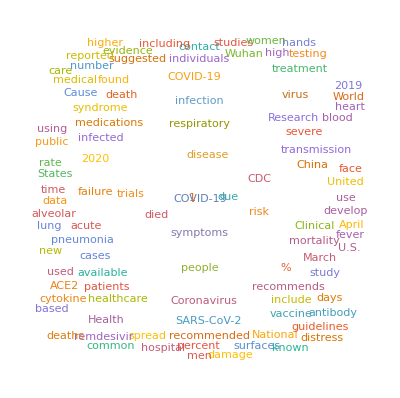

```mathematica
(* wordcloud of the Covid-19 Wikipedia article *)
WordCloud@DeleteStopwords@TextWords@WikipediaData["CoViD 19", "ArticlePlaintext"]
```

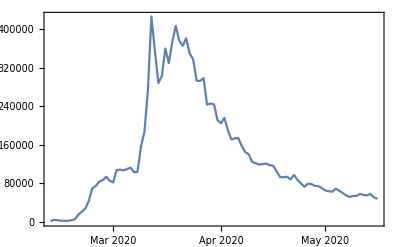

```mathematica
(* daily page hits of the article *)
DateListPlot[WikipediaData["CoViD 19", "DailyPageHits"], PlotTheme->"Detailed"]
```

We can also see a breakdown of how people have been accessing the article. Comparably way fewer people use the Wikipedia mobile app and that’s probably why that line is mostly flat for the entire period. Mobile web and Desktop views were initially the same but mobile grew faster in March. Views from Mobile and Desktop are now similar again in mid-May, though mobile is still slightly above. This could be because people are generally using their phones more frequently than their laptops each day.

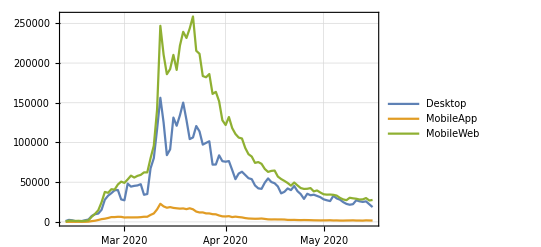

```mathematica
(* breakdown of page views by access types *)
With[{accessData = Association[(# -> WikipediaData["CoViD 19", {"DailyPageHits", "Access" -> #}])&/@{"Desktop", "MobileApp", "MobileWeb"}]},
DateListPlot[accessData, PlotTheme->"Detailed", PlotRange->All]
]
```

But are all of those views even from real people? What portion of them are from bots?

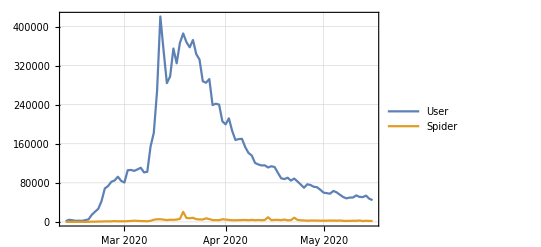

```mathematica
(* "Bot" is currenlty returning an error: "Wikipedia servers are currently under maintenance or experiencing a technical problem. Please try again in a few minutes." *)
With[{agentData = Association[(# -> WikipediaData["CoViD 19", {"DailyPageHits", "Agent" -> #}])&/@{"User", "Spider"(*, "Bot"*)}]},
DateListPlot[agentData, PlotTheme->"Detailed", PlotRange->All]
]
```

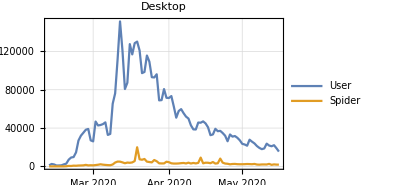
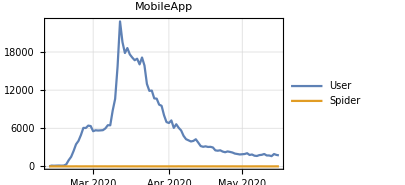
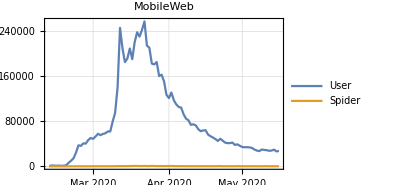
-Graphics- | -Graphics- | -Graphics-

```mathematica
(* Spider views appear to come only from Desktop. Bot data also not available in this case *)
Grid@List@Table[
With[{accessAgentData = Association[#->WikipediaData["CoViD 19", {"DailyPageHits", "Access"->ac, "Agent"->#}]&/@{"User", "Spider"(*, "Bot"*)}]},
DateListPlot[accessAgentData, PlotLabel->ac, PlotTheme->"Detailed", PlotRange->All, ImageSize->300]],
{ac, {"Desktop", "MobileApp", "MobileWeb"}}]
```

## Wikidata

```mathematica
(* search for COVID-19-related data on Wikipedia *)
WikidataSearch["Covid-19"]
```

{ExternalIdentifier[WikidataID,Q84263196,<|Label→COVID-19,Description→zoonotic respiratory syndrome and infectious disease in humans, caused by SARS coronavirus 2|>]WikidataCOVID-19http://www.wikidata.org/entity/Q84263196,ExternalIdentifier[WikidataID,Q87718451,<|Label→2020 COVID-19 pandemic in Nigeria|>]Wikidata2020 COVID-19 pandemic in Nigeriahttp://www.wikidata.org/entity/Q87718451,ExternalIdentifier[WikidataID,Q81068910,<|Label→COVID-19 pandemic,Description→ongoing pandemic of COVID-19|>]WikidataCOVID-19 pandemichttp://www.wikidata.org/entity/Q81068910,ExternalIdentifier[WikidataID,Q93202208,<|Label→COVID-19,Description→scientific article published on 01 April 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q93202208,ExternalIdentifier[WikidataID,Q93219706,<|Label→COVID-19,Description→scientific article published on 23 April 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q93219706,ExternalIdentifier[WikidataID,Q91601520,<|Label→COVID-19,Description→scientific article published on 30 March 2020|>]WikidataCOVID-19http://www.wikidata.org/entity/Q91601520,ExternalIdentifier[WikidataID,Q94502207,<|Label→Covid-19,Description→scientific article published on 30 April 2020|>]WikidataCovid-19http://www.wikidata.org/entity/Q94502207,ExternalIdentifier[WikidataID,Q84055514,<|Label→2020 COVID-19 pandemic in India,Description→details of ongoing viral pandemic in India in 2020|>]Wikidata2020 COVID-19 pandemic in Indiahttp://www.wikidata.org/entity/Q84055514,ExternalIdentifier[WikidataID,Q83741704,<|Label→COVID-19 pandemic by country and territory,Description→details regarding the 2019–20 coronavirus pandemic by country and territory|>]WikidataCOVID-19 pandemic by country and territoryhttp://www.wikidata.org/entity/Q83741704,ExternalIdentifier[WikidataID,Q83873577,<|Label→COVID-19 pandemic in the United States,Description→ongoing coronavirus pandemic in the United States|>]WikidataCOVID-19 pandemic in the United Stateshttp://www.wikidata.org/entity/Q83873577}

```mathematica
(* view the properties of a given Wikidata item *)
WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P17,<|Label→country,Description→sovereign state of this item (not to be used for human beings)|>]Wikidatacountryhttp://www.wikidata.org/entity/P17,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P237,<|Label→coat of arms,Description→subject's coat of arms|>]Wikidatacoat of armshttp://www.wikidata.org/entity/P237,ExternalIdentifier[WikidataID,P276,<|Label→location,Description→location of the item, physical object or event is within. In case of an administrative entity use P131. In case of a distinct terrain feature use P706.|>]Wikidatalocationhttp://www.wikidata.org/entity/P276,ExternalIdentifier[WikidataID,P361,<|Label→part of,Description→object of which the subject is a part (if this subject is already part of object A which is a part of object B, then please only make the subject part of object A). Inverse property of "has part" (P527, see also "has parts of the class" (P2670)).|>]Wikidatapart ofhttp://www.wikidata.org/entity/P361,ExternalIdentifier[WikidataID,P580,<|Label→start time,Description→time an item begins to exist or a statement starts being valid|>]Wikidatastart timehttp://www.wikidata.org/entity/P580,ExternalIdentifier[WikidataID,P625,<|Label→coordinate location,Description→geocoordinates of the subject. For Earth, please note that only WGS84 coordinating system is supported at the moment|>]Wikidatacoordinate locationhttp://www.wikidata.org/entity/P625,ExternalIdentifier[WikidataID,P373,<|Label→Commons category,Description→name of the Wikimedia Commons category containing files related to this item (without the prefix "Category:")|>]WikidataCommons categoryhttp://www.wikidata.org/entity/P373,ExternalIdentifier[WikidataID,P828,<|Label→has cause,Description→underlying cause, thing that ultimately resulted in this effect|>]Wikidatahas causehttp://www.wikidata.org/entity/P828,ExternalIdentifier[WikidataID,P910,<|Label→topic's main category,Description→main Wikimedia category|>]Wikidatatopic's main categoryhttp://www.wikidata.org/entity/P910,ExternalIdentifier[WikidataID,P1120,<|Label→number of deaths,Description→Total (cumulative) number of people who died since start as a direct result of an event or cause|>]Wikidatanumber of deathshttp://www.wikidata.org/entity/P1120,ExternalIdentifier[WikidataID,P1603,<|Label→number of cases,Description→cumulative number of confirmed, probable and suspected occurrences|>]Wikidatanumber of caseshttp://www.wikidata.org/entity/P1603,ExternalIdentifier[WikidataID,P1846,<|Label→distribution map,Description→distribution of item on a mapped area (for  range map of taxa, use (P181).)|>]Wikidatadistribution maphttp://www.wikidata.org/entity/P1846,ExternalIdentifier[WikidataID,P2572,<|Label→hashtag,Description→hashtag associated with this entity. Format: do not include the "#" symbol|>]Wikidatahashtaghttp://www.wikidata.org/entity/P2572,ExternalIdentifier[WikidataID,P3457,<|Label→case fatality rate,Description→proportion of patients who die of a particular medical condition out of all who have this condition within a given time frame|>]Wikidatacase fatality ratehttp://www.wikidata.org/entity/P3457,ExternalIdentifier[WikidataID,P8010,<|Label→number of recoveries,Description→number of cases that recovered from disease|>]Wikidatanumber of recoverieshttp://www.wikidata.org/entity/P8010,ExternalIdentifier[WikidataID,P8045,<|Label→organized response related to outbreak,Description→specific action taken or system used as a reaction to an outbreak|>]Wikidataorganized response related to outbreakhttp://www.wikidata.org/entity/P8045}

```mathematica
(* view data and their respective sources *)
Values@WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, ExternalIdentifier["WikidataID","P1120",<|"Label"->"number of deaths","Description"->"Total (cumulative) number of people who died since start as a direct result of an event or cause"|>]"Wikidata""number of deaths"http://www.wikidata.org/entity/P1120,
Method -> {"StatementFormat" -> {"Association", "IncludeQualifiers"->True, "IncludeReferences"->True}}] // Short[#,5]&
```

{{0.,{Day: Tue 17 Mar 2020},{<|ExternalIdentifier[WikidataID,P585,<|Label→point in time,Description→time and date something took place, existed or a statement was true|>]Wikidatapoint in timehttp://www.wikidata.org/entity/P585→{Day: Mon 16 Mar 2020},ExternalIdentifier[WikidataID,P248,<|Label→stated in,Description→to be used in the references field to refer to the information document or database in which a claim is made; for qualifiers use P805|>]Wikidatastated inhttp://www.wikidata.org/entity/P248→{ExternalIdentifier[WikidataID,Q87779474,<|Label→Novel Coronavirus (2019-nCoV) Situation Report 56,Description→report from the WHO about COVID-19 epidemic at 16 March 2020|>]WikidataNovel Coronavirus (2019-nCoV) Situation Report 56http://www.wikidata.org/entity/Q87779474}|>,<|ExternalIdentifier[WikidataID,P248,<|Label→stated in,Description→to be used in the references field to refer to the information document or database in which a claim is made; for qualifiers use P805|>]Wikidatastated inhttp://www.wikidata.org/entity/P248→{ExternalIdentifier[WikidataID,Q87843252,<|Label→Novel Coronavirus (2019-nCoV) Situation Report 57,Description→report from the WHO about COVID-19 epidemic at 17 March 2020|>]WikidataNovel Coronavirus (2019-nCoV) Situation Report 57http://www.wikidata.org/entity/Q87843252}|>,<|ExternalIdentifier[WikidataID,P143,<|Label→imported from Wikimedia project,Description→source of this claim's value; used in references section by bots importing data from Wikimedia projects; also allowed to be used for manual imports|>]Wikidataimported from Wikimedia projecthttp://www.wikidata.org/entity/P143→{ExternalIdentifier[WikidataID,Q328,<|Label→English Wikipedia,Description→English‑language edition of the free online encyclopedia|>]WikidataEnglish Wikipediahttp://www.wikidata.org/entity/Q328}|>}},{103.,{Day: Wed 6 May 2020},{<|ExternalIdentifier[WikidataID,P813,<|Label→retrieved,Description→date or point in time that information was retrieved from a database or website (for use in online sources)|>]Wikidataretrievedhttp://www.wikidata.org/entity/P813→{Day: Thu 7 May 2020},ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://github.com/datasets/covid-19]}|>}},{143.,{Day: Sun 10 May 2020},{<|ExternalIdentifier[WikidataID,P813,<|Label→retrieved,Description→date or point in time that information was retrieved from a database or website (for use in online sources)|>]Wikidataretrievedhttp://www.wikidata.org/entity/P813→{Day: Tue 12 May 2020},ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://datahub.io/core/covid-19]},ExternalIdentifier[WikidataID,P7793,<|Label→filename in archive,Description→qualifier and referencing property to identify the specific file within a compressed archive that is relevant to a statement|>]Wikidatafilename in archivehttp://www.wikidata.org/entity/P7793→{r/countries-aggregated.csv}|>}},{158.,{Day: Tue 12 May 2020},{<|ExternalIdentifier[WikidataID,P813,<|Label→retrieved,Description→date or point in time that information was retrieved from a database or website (for use in online sources)|>]Wikidataretrievedhttp://www.wikidata.org/entity/P813→{Day: Thu 14 May 2020},ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://datahub.io/core/covid-19]},ExternalIdentifier[WikidataID,P7793,<|Label→filename in archive,Description→qualifier and referencing property to identify the specific file within a compressed archive that is relevant to a statement|>]Wikidatafilename in archivehttp://www.wikidata.org/entity/P7793→{r/countries-aggregated.csv}|>}},{1.,{Day: Sat 28 Mar 2020}},«21»,{68.,{Day: Fri 1 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}},{85.,{Day: Sat 2 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}},{87.,{Day: Sun 3 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}},{93.,{Day: Mon 4 May 2020},{<|ExternalIdentifier[WikidataID,P854,<|Label→reference URL,Description→should be used for Internet URLs as references. Use "Wikimedia import URL" (P4656) for interwiki links|>]Wikidatareference URLhttp://www.wikidata.org/entity/P854→{URL[https://ncdc.gov.ng/diseases/sitreps/?cat=14&name=An%20update%20of%20COVID-19%20outbreak%20in%20Nigeria]}|>}}}

```mathematica
(* get data for no. of cases and deaths *)
casesAndDeathsInNigeria = Association[
# -> WikidataData[ExternalIdentifier["WikidataID","Q87718451",<|"Label"->"2020 COVID-19 pandemic in Nigeria"|>]"Wikidata""2020 COVID-19 pandemic in Nigeria"http://www.wikidata.org/entity/Q87718451, #,
Method -> {"StatementFormat" -> {"Association", "IncludeQualifiers"->True, "IncludeReferences"->False}}]&/@{ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603,  ExternalIdentifier["WikidataID","P1120",<|"Label"->"number of deaths","Description"->"Total (cumulative) number of people who died since start as a direct result of an event or cause"|>]"Wikidata""number of deaths"http://www.wikidata.org/entity/P1120}
]/.(a_Association /; Length[a]<2) -> Nothing;
```

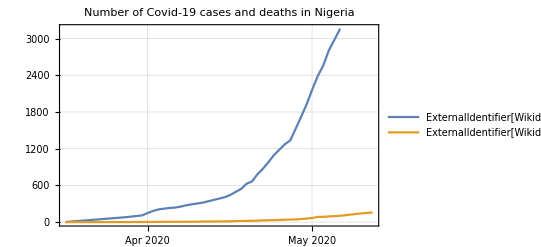

```mathematica
(* plot data *)
DateListPlot[MapAt[Reverse[Flatten@#]&, Values/@casesAndDeathsInNigeria, {;;, ;;}],
PlotTheme->"Detailed", PlotLabel->"Number of Covid-19 cases and deaths in Nigeria"]
```

```mathematica
(* with Wikidata, properties have properties too. this is great for building a custom knowledge graph for a given topic *)
WikidataData[ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P1629,<|Label→subject item of this property,Description→relationship represented by the property|>]Wikidatasubject item of this propertyhttp://www.wikidata.org/entity/P1629,ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P1659,<|Label→see also,Description→used to indicate another property that might provide additional information about the Wikidata-property|>]Wikidatasee alsohttp://www.wikidata.org/entity/P1659,ExternalIdentifier[WikidataID,P1855,<|Label→Wikidata property example,Description→example where this Wikidata property is used; target item is one that would use this property, with qualifier the property being described given the associated value|>]WikidataWikidata property examplehttp://www.wikidata.org/entity/P1855,ExternalIdentifier[WikidataID,P2302,<|Label→property constraint,Description→constraint applicable to this Wikidata property|>]Wikidataproperty constrainthttp://www.wikidata.org/entity/P2302,ExternalIdentifier[WikidataID,P2875,<|Label→property usage tracking category,Description→category tracking a Wikidata property in sister projects|>]Wikidataproperty usage tracking categoryhttp://www.wikidata.org/entity/P2875,ExternalIdentifier[WikidataID,P3254,<|Label→property proposal discussion,Description→URL of the page (or page section) on which the creation of the property was discussed|>]Wikidataproperty proposal discussionhttp://www.wikidata.org/entity/P3254}

```mathematica
(* example property of a property *)
WikidataData[ExternalIdentifier["WikidataID","P1603",<|"Label"->"number of cases","Description"->"cumulative number of confirmed, probable and suspected occurrences"|>]"Wikidata""number of cases"http://www.wikidata.org/entity/P1603, ExternalIdentifier["WikidataID","P1659",<|"Label"->"see also","Description"->"used to indicate another property that might provide additional information about the Wikidata-property"|>]"Wikidata""see also"http://www.wikidata.org/entity/P1659]
```

{ExternalIdentifier[WikidataID,P8049,<|Label→number of hospitalized cases,Description→number of cases that are hospitalized|>]Wikidatanumber of hospitalized caseshttp://www.wikidata.org/entity/P8049,ExternalIdentifier[WikidataID,P8204,<|Label→tabular case data,Description→tabular data on Wikimedia Commons of confirmed cases, recoveries, deaths, etc. due to a medical event; corresponds to P8011, P1603, P8049, P8010, P1120. Do not delete such statements.|>]Wikidatatabular case datahttp://www.wikidata.org/entity/P8204,ExternalIdentifier[WikidataID,P1120,<|Label→number of deaths,Description→Total (cumulative) number of people who died since start as a direct result of an event or cause|>]Wikidatanumber of deathshttp://www.wikidata.org/entity/P1120,ExternalIdentifier[WikidataID,P1193,<|Label→prevalence,Description→portion of a population with a given disease|>]Wikidataprevalencehttp://www.wikidata.org/entity/P1193,ExternalIdentifier[WikidataID,P2844,<|Label→incidence,Description→probability of occurrence of a given condition in a population within a specified period of time|>]Wikidataincidencehttp://www.wikidata.org/entity/P2844,ExternalIdentifier[WikidataID,P8011,<|Label→number of clinical tests,Description→cumulative number of clinical tests|>]Wikidatanumber of clinical testshttp://www.wikidata.org/entity/P8011,ExternalIdentifier[WikidataID,P8010,<|Label→number of recoveries,Description→number of cases that recovered from disease|>]Wikidatanumber of recoverieshttp://www.wikidata.org/entity/P8010}

```mathematica
(* see info on a given data collection. this shows the braoder context of the data - it could be subset of a bigger dataset, and/or have it's own parts. *)
WikidataData[ExternalIdentifier["WikidataID","Q83873577",<|"Label"->"2020 COVID-19 pandemic in the United States","Description"->"viral outbreak in the United States"|>]"Wikidata""2020 COVID-19 pandemic in the United States"http://www.wikidata.org/entity/Q83873577, "Dataset"]
```

```mathematica
(* list of countries for which there is Wikidata coverage on Covid-19 pandemic *)
covidPandemicCountries = WikidataData[ExternalIdentifier["WikidataID","Q83741704",<|"Label"->"COVID-19 pandemic by country and territory","Description"->"details regarding the 2019–20 coronavirus pandemic by country and territory"|>]"Wikidata""COVID-19 pandemic by country and territory"http://www.wikidata.org/entity/Q83741704, ExternalIdentifier["WikidataID","P527",<|"Label"->"has part","Description"->"part of this subject; inverse property of \"part of\" (P361). See also \"has parts of the class\" (P2670)."|>]"Wikidata""has part"http://www.wikidata.org/entity/P527];
{Highlighted@Length@covidPandemicCountries, Short[covidPandemicCountries, .2]}
```

{196,{ExternalIdentifier[WikidataID,Q83872271,<|Label→2019–20 coronavirus pandemic in mainland China,Description→viral outbreak in mainland China|>]Wikidata2019–20 coronavirus pandemic in mainland Chinahttp://www.wikidata.org/entity/Q83872271,ExternalIdentifier[WikidataID,Q83872291,<|Label→COVID-19 pandemic in Japan,Description→viral outbreak in Japan|>]WikidataCOVID-19 pandemic in Japanhttp://www.wikidata.org/entity/Q83872291,ExternalIdentifier[WikidataID,Q83872398,<|Label→2019–20 COVID-19 outbreak in South Korea,Description→viral outbreak in South Korea|>]Wikidata2019–20 COVID-19 outbreak in South Koreahttp://www.wikidata.org/entity/Q83872398,ExternalIdentifier[WikidataID,Q83873057,<|Label→COVID-19 pandemic in Vietnam,Description→viral outbreak in Vietnam|>]WikidataCOVID-19 pandemic in Vietnamhttp://www.wikidata.org/entity/Q83873057,ExternalIdentifier[WikidataID,Q83873387,<|Label→2020 COVID-19 pandemic in Singapore,Description→details of ongoing viral outbreak in Singapore|>]Wikidata2020 COVID-19 pandemic in Singaporehttp://www.wikidata.org/entity/Q83873387,ExternalIdentifier[WikidataID,Q83873548,<|Label→2020 COVID-19 pandemic in Australia,Description→viral outbreak in Australia|>]Wikidata2020 COVID-19 pandemic in Australiahttp://www.wikidata.org/entity/Q83873548,ExternalIdentifier[WikidataID,Q83873556,<|Label→2020 COVID-19 pandemic in Malaysia,Description→viral outbreak in Malaysia|>]Wikidata2020 COVID-19 pandemic in Malaysiahttp://www.wikidata.org/entity/Q83873556,ExternalIdentifier[WikidataID,Q83873566,<|Label→2020 COVID-19 pandemic in Thailand,Description→viral outbreak in Thailand|>]Wikidata2020 COVID-19 pandemic in Thailandhttp://www.wikidata.org/entity/Q83873566,ExternalIdentifier[WikidataID,Q83873573,<|Label→2019–20 coronavirus outbreak in Nepal,Description→viral outbreak in Nepal|>]Wikidata2019–20 coronavirus outbreak in Nepalhttp://www.wikidata.org/entity/Q83873573,«178»,ExternalIdentifier[WikidataID,Q87709900,<|Label→2020 COVID-19 pandemic in Mauritania,Description→details of ongoing viral pandemic in Mauritania|>]Wikidata2020 COVID-19 pandemic in Mauritaniahttp://www.wikidata.org/entity/Q87709900,ExternalIdentifier[WikidataID,Q87709973,<|Label→2020 COVID-19 pandemic in Eswatini,Description→viral pandemic in Eswatini|>]Wikidata2020 COVID-19 pandemic in Eswatinihttp://www.wikidata.org/entity/Q87709973,ExternalIdentifier[WikidataID,Q87714704,<|Label→2020 COVID-19 pandemic in Rwanda,Description→viral pandemic in Rwanda|>]Wikidata2020 COVID-19 pandemic in Rwandahttp://www.wikidata.org/entity/Q87714704,ExternalIdentifier[WikidataID,Q87715166,<|Label→2020 COVID-19 pandemic in Bhutan,Description→viral pandemic in Bhutan|>]Wikidata2020 COVID-19 pandemic in Bhutanhttp://www.wikidata.org/entity/Q87715166,ExternalIdentifier[WikidataID,Q87715843,<|Label→2020 COVID-19 pandemic in Andorra,Description→details of ongoing viral pandemic in Teil der COVID-19-Pandemie|>]Wikidata2020 COVID-19 pandemic in Andorrahttp://www.wikidata.org/entity/Q87715843,ExternalIdentifier[WikidataID,Q87722485,<|Label→2020 COVID-19 pandemic in Azerbaijan,Description→viral pandemic in Azerbaijan|>]Wikidata2020 COVID-19 pandemic in Azerbaijanhttp://www.wikidata.org/entity/Q87722485,ExternalIdentifier[WikidataID,Q87729500,<|Label→2020 COVID-19 pandemic in Seychelles,Description→viral pandemic in Seychelles|>]Wikidata2020 COVID-19 pandemic in Seychelleshttp://www.wikidata.org/entity/Q87729500,ExternalIdentifier[WikidataID,Q87729501,<|Label→2020 COVID-19 pandemic in Namibia,Description→viral pandemic in Namibia|>]Wikidata2020 COVID-19 pandemic in Namibiahttp://www.wikidata.org/entity/Q87729501,ExternalIdentifier[WikidataID,Q87733671,<|Label→2020 COVID-19 pandemic in Qatar,Description→viral pandemic in Qatar|>]Wikidata2020 COVID-19 pandemic in Qatarhttp://www.wikidata.org/entity/Q87733671}}

Responses to the outbreak differ from one country to another. Also, the absence of data for a particular country does not suggest that no precautions were put in place.

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q87186365",<|"Label"->"2020 COVID-19 pandemic in the Republic of Ireland","Description"->"details of ongoing viral outbreak in the Republic of Ireland"|>]"Wikidata""2020 COVID-19 pandemic in the Republic of Ireland"http://www.wikidata.org/entity/Q87186365,  ExternalIdentifier["WikidataID","P8045",<|"Label"->"organized response related to outbreak","Description"->"specific action taken or system used as a reaction to an outbreak"|>]"Wikidata""organized response related to outbreak"http://www.wikidata.org/entity/P8045]
```

{ExternalIdentifier[WikidataID,Q93623431,<|Label→2020 Ireland COVID-19 social distancing,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 social distancinghttp://www.wikidata.org/entity/Q93623431,ExternalIdentifier[WikidataID,Q93623429,<|Label→2020 Ireland COVID-19 closing of educational institutions,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 closing of educational institutionshttp://www.wikidata.org/entity/Q93623429,ExternalIdentifier[WikidataID,Q93623435,<|Label→2020 Ireland COVID-19 closing of non-essential businesses,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 closing of non-essential businesseshttp://www.wikidata.org/entity/Q93623435,ExternalIdentifier[WikidataID,Q93623433,<|Label→2020 Ireland COVID-19 lockdown,Description→COVID-19 countermeasure in Ireland|>]Wikidata2020 Ireland COVID-19 lockdownhttp://www.wikidata.org/entity/Q93623433}

```mathematica
(* see when a particular measure was announced and enacted *)
WikidataData[ExternalIdentifier["WikidataID","Q93623431",<|"Label"->"2020 Ireland COVID-19 social distancing","Description"->"COVID-19 countermeasure in Ireland"|>]"Wikidata""2020 Ireland COVID-19 social distancing"http://www.wikidata.org/entity/Q93623431, "Dataset"]
```

```mathematica
WikidataData[ExternalIdentifier["WikidataID","Q93623431",<|"Label"->"2020 Ireland COVID-19 social distancing","Description"->"COVID-19 countermeasure in Ireland"|>]"Wikidata""2020 Ireland COVID-19 social distancing"http://www.wikidata.org/entity/Q93623431, "NonIdentifierProperties"]
```

{ExternalIdentifier[WikidataID,P31,<|Label→instance of,Description→that class of which this subject is a particular example and member|>]Wikidatainstance ofhttp://www.wikidata.org/entity/P31,ExternalIdentifier[WikidataID,P6949,<|Label→announcement date,Description→time of the first public presentation of a subject by the creator, of information by the media|>]Wikidataannouncement datehttp://www.wikidata.org/entity/P6949,ExternalIdentifier[WikidataID,P580,<|Label→start time,Description→time an item begins to exist or a statement starts being valid|>]Wikidatastart timehttp://www.wikidata.org/entity/P580,ExternalIdentifier[WikidataID,P828,<|Label→has cause,Description→underlying cause, thing that ultimately resulted in this effect|>]Wikidatahas causehttp://www.wikidata.org/entity/P828,ExternalIdentifier[WikidataID,P1001,<|Label→applies to jurisdiction,Description→the item (an institution, law, public office ...) or statement belongs to or has power over or applies to the value (a territorial jurisdiction: a country, state, municipality, ...)|>]Wikidataapplies to jurisdictionhttp://www.wikidata.org/entity/P1001}

```mathematica
(* responses of countries for which this data is available *)
covidPandemicResponses = DeleteCases[
Thread[# -> WikidataData[#, ExternalIdentifier["WikidataID","P8045",<|"Label"->"organized response related to outbreak","Description"->"specific action taken or system used as a reaction to an outbreak"|>]"Wikidata""organized response related to outbreak"http://www.wikidata.org/entity/P8045]]&@covidPandemicCountries // Association,
{}];
```

```mathematica
(* Sweden has so far has the highest number of distinct responses, followed by Jordan and New Zealand. *)
ReverseSortBy[Length]@covidPandemicResponses // Dataset[#, MaxItems->5]&
(* Sweden's responses *)
%[1]
```

```mathematica
(* response type and start date data for all countries *)
covidPandemicResponsesData = MapAt[Flatten, WikidataData[#, {ExternalIdentifier["WikidataID","P31",<|"Label"->"instance of","Description"->"that class of which this subject is a particular example and member"|>]"Wikidata""instance of"http://www.wikidata.org/entity/P31, ExternalIdentifier["WikidataID","P580",<|"Label"->"start time","Description"->"time an item begins to exist or a statement starts being valid"|>]"Wikidata""start time"http://www.wikidata.org/entity/P580}]&/@covidPandemicResponses, {;;, ;;}];
(* view data *)
covidPandemicResponsesData // Dataset[#, MaxItems->5]&
```

```mathematica
(* tally of responses by all countries *)
ReverseSortBy[Last]@Tally@Cases[Flatten@Values@covidPandemicResponsesData,_ExternalIdentifier] // Grid[#, Alignment->Right]&
```

ExternalIdentifier[WikidataID,Q88323877,<|Label→closing of educational institutions,Description→action to reduce virus transmission|>]Wikidataclosing of educational institutionshttp://www.wikidata.org/entity/Q88323877 | 56
ExternalIdentifier[WikidataID,Q30314010,<|Label→social distancing,Description→reduction of human social interaction in an effort to prevent the spread of infectious disease|>]Wikidatasocial distancinghttp://www.wikidata.org/entity/Q30314010 | 54
ExternalIdentifier[WikidataID,Q87745167,<|Label→travel restriction,Description→policy|>]Wikidatatravel restrictionhttp://www.wikidata.org/entity/Q87745167 | 50
ExternalIdentifier[WikidataID,Q7257745,<|Label→declaration of public health emergency,Description→The declaration of a public health emergency in response to a (public) health crisis.|>]Wikidatadeclaration of public health emergencyhttp://www.wikidata.org/entity/Q7257745 | 44
ExternalIdentifier[WikidataID,Q88761394,<|Label→travel ban,Description→restriction of all means of travel|>]Wikidatatravel banhttp://www.wikidata.org/entity/Q88761394 | 38
ExternalIdentifier[WikidataID,Q88761692,<|Label→flight ban,Description→Restriction of air travel, e.g. closure of airports|>]Wikidataflight banhttp://www.wikidata.org/entity/Q88761692 | 32
ExternalIdentifier[WikidataID,Q6665312,<|Label→lockdown,Description→emergency protocol that prevents people or information from leaving an area|>]Wikidatalockdownhttp://www.wikidata.org/entity/Q6665312 | 31
ExternalIdentifier[WikidataID,Q223625,<|Label→curfew,Description→political or police ban on entering public areas such as streets or squares|>]Wikidatacurfewhttp://www.wikidata.org/entity/Q223625 | 28
ExternalIdentifier[WikidataID,Q89681240,<|Label→closing of non-essential businesses|>]Wikidataclosing of non-essential businesseshttp://www.wikidata.org/entity/Q89681240 | 16
ExternalIdentifier[WikidataID,Q89211965,<|Label→decision by the Swedish Government,Description→formal decisions in government meetings|>]Wikidatadecision by the Swedish Governmenthttp://www.wikidata.org/entity/Q89211965 | 5
ExternalIdentifier[WikidataID,Q88307738,<|Label→stay-at-home order,Description→type of quarantine|>]Wikidatastay-at-home orderhttp://www.wikidata.org/entity/Q88307738 | 3
ExternalIdentifier[WikidataID,Q182899,<|Label→quarantine,Description→epidemiological intervention of restriction on the movement of people and goods, which is intended to prevent the spread of infectious disease or pests|>]Wikidataquarantinehttp://www.wikidata.org/entity/Q182899 | 3
ExternalIdentifier[WikidataID,Q5370734,<|Label→emergency procedure,Description→plan of action to deal with an emergency|>]Wikidataemergency procedurehttp://www.wikidata.org/entity/Q5370734 | 2
ExternalIdentifier[WikidataID,Q88707306,<|Label→border closure,Description→action to reduce virus transmission in the community|>]Wikidataborder closurehttp://www.wikidata.org/entity/Q88707306 | 1
ExternalIdentifier[WikidataID,Q88705465,<|Label→travel advice as non-pharmaceutical countermeasure,Description→action to reduce virus transmission in the community|>]Wikidatatravel advice as non-pharmaceutical countermeasurehttp://www.wikidata.org/entity/Q88705465 | 1
ExternalIdentifier[WikidataID,Q88324058,<|Label→avoiding crowding,Description→action to reduce virus transmission|>]Wikidataavoiding crowdinghttp://www.wikidata.org/entity/Q88324058 | 1
ExternalIdentifier[WikidataID,Q820655,<|Label→legislative act,Description→formal written document that creates law, including acts, executive orders, and by-laws|>]Wikidatalegislative acthttp://www.wikidata.org/entity/Q820655 | 1
ExternalIdentifier[WikidataID,Q428148,<|Label→regulation,Description→general term for rules or controls, including delegated legislation and self-regulation|>]Wikidataregulationhttp://www.wikidata.org/entity/Q428148 | 1
ExternalIdentifier[WikidataID,Q2795484,<|Label→implementing regulation,Description→regulation on the details of the implementation of a law|>]Wikidataimplementing regulationhttp://www.wikidata.org/entity/Q2795484 | 1
ExternalIdentifier[WikidataID,Q207184,<|Label→press release,Description→instrument of public relations|>]Wikidatapress releasehttp://www.wikidata.org/entity/Q207184 | 1
ExternalIdentifier[WikidataID,Q1864008,<|Label→legal act,Description→juridical fact in which the subject who made it happen acted under free will|>]Wikidatalegal acthttp://www.wikidata.org/entity/Q1864008 | 1
ExternalIdentifier[WikidataID,Q1032176,<|Label→countermeasure,Description→specific action taken or system used to offset another action|>]Wikidatacountermeasurehttp://www.wikidata.org/entity/Q1032176 | 1

```mathematica
(* compare start dates of Covid-19 responses around the world *)
responseTimelinePlot[response_, plotLabel_] := Block[{pos, data},
pos = Position[covidPandemicResponsesData, {response, _}];
data = KeyMap[Capitalize@StringDelete[#@"Label", __~~"in "]&, Association@Thread[pos⟦;;, 1, 1⟧ -> Extract[covidPandemicResponsesData, pos]⟦;;, 2⟧]];
TimelinePlot[Association@data, PlotLayout->"VerticalGrouped", PlotTheme->"Business", AspectRatio->.4, ImageSize->{Automatic, 500}, PlotLabel->plotLabel]
]
```

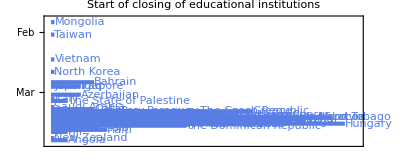

```mathematica
(* educational institutions *)
responseTimelinePlot[ExternalIdentifier["WikidataID","Q88323877",<|"Label"->"closing of educational institutions","Description"->"action to reduce virus transmission"|>]"Wikidata""closing of educational institutions"http://www.wikidata.org/entity/Q88323877, "Start of closing of educational institutions"]
```

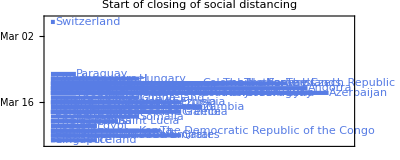

```mathematica
(* social distancing *)
responseTimelinePlot[ExternalIdentifier["WikidataID","Q30314010",<|"Label"->"social distancing","Description"->"reduction of human social interaction in an effort to prevent the spread of infectious disease"|>]"Wikidata""social distancing"http://www.wikidata.org/entity/Q30314010, "Start of closing of social distancing"]
```

Note the not every country is included in the couple of plots above. For example, social distancing was introduced in the UK in March but this does not appear in Wikidata.

### Government measures data from Wolfram Data Repository

On the Wolfram Data Repository, there is a dataset on measures taken by governments around the world. This dataset contains more detailed information than what we can pull from Wikidata.

-Graphics-

```mathematica
(* resource object *)
resObj = ResourceObject["Coronavirus COVID-19 Pandemic Government Measures"]
```

ResourceObject[…]

```mathematica
(* get resource data *)
resObjData = ResourceData@resObj
```

Dataset[<>]

Each enacted measure is categorised and contains 18 a total of properties including its implementation data and the source of the information.

```mathematica
resObjData[GroupBy@"Category", ;;, "Measure"][;;, Tally][;;, ReverseSortBy@Last]
```

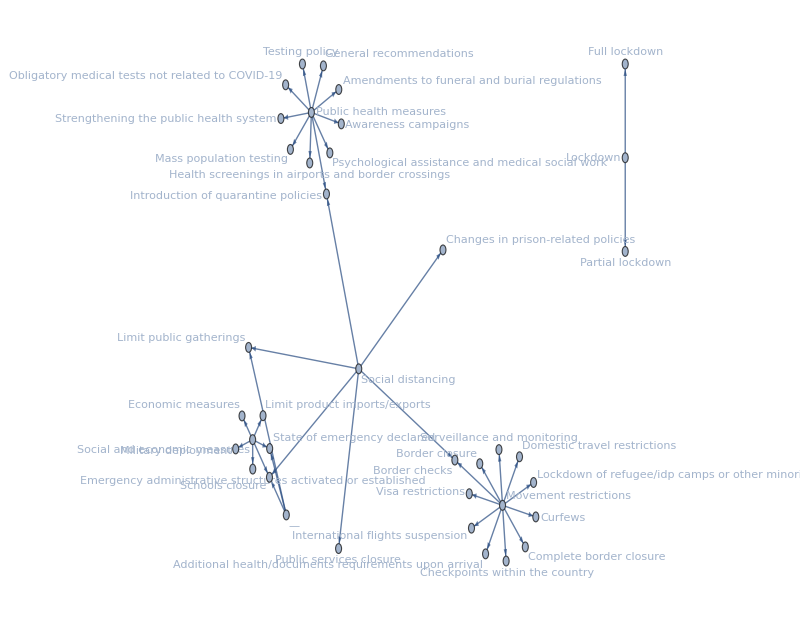

```mathematica
(* groupings of categories and measures *)
GraphPlot[Flatten[Thread/@(Normal@Normal@resObjData[GroupBy@"Category", ;;, "Measure"][;;, DeleteDuplicates])], 
VertexLabels->"Name", GraphLayout->"BalloonEmbedding", ImageSize->800, DirectedEdges->True]
```

```mathematica
(* category-measure tally data *)
cmTallies = Normal@Echo[Tally/@resObjData[GroupBy@"Category", ;;, "Measure"]];
```

```mathematica
(* breakdown of categories and measures *)
Table[
With[{cat = cmTallies⟦i⟧},
PieChart[Association[Rule@@@cat],
ChartLabels->Callout@Automatic, PlotRange->Full, ImageSize->{Automatic, 200}, PlotLabel->Keys[cmTallies]⟦i⟧]
], {i, Range@Length@cmTallies}] // 
Multicolumn[#, 2, ItemSize->Full, Alignment->Center, Frame->All, FrameStyle->LightGray]&
```

-Graphics-

```mathematica
(* proportions of measures - applied as graph edge thickness values below *)
measuresEdgeSizes = Table[
Block[{cat = Take[cmTallies, {i}], vals, sum},
vals = First@Values@cat;
sum = Total@vals⟦;;, 2⟧;
vals/.{meas_String, no_Integer} :> Rule[Keys[cat]⟦1⟧, meas] -> no],
{i, Range@Length@cmTallies}] // Flatten;

measuresEdgeSizes = Thread[measuresEdgeSizes⟦;;, 1⟧ -> (Directive[{Thickness[0.01*#], Opacity@#}] &/@ (.2 + Rescale@measuresEdgeSizes⟦;;, 2⟧))];
```

```mathematica
(* proportions of categories - applied as vertex size values below *)
categoriesVertexSizes = Join[
N[#/1000] &/@ Total/@MapAt[Last, cmTallies, {;;, ;;}] // Normal,
Thread[measuresEdgeSizes⟦;;, 1, 2⟧ -> 0.3]
];
```

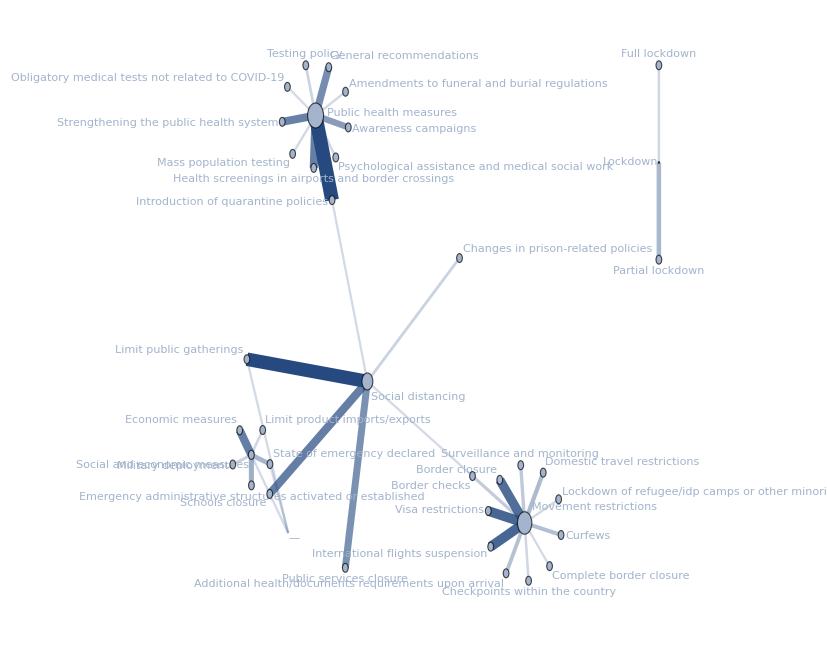

```mathematica
(* graphical form of breakdown *)
Graph[measuresEdgeSizes⟦;;, 1⟧,
EdgeStyle->measuresEdgeSizes, VertexLabels->"Name", DirectedEdges->False, GraphLayout->"BalloonEmbedding", VertexSize->categoriesVertexSizes]
```

## Wolfram Data Framework / Entities

Natural language input “Covid-19” is automatically interpreted as a disease and converted to an explorable real-world entity.

WolframAlphaQueryParseResults

COVID-19

```mathematica
(* Covid-19 as a disease entity *)
covid19 = Entity["Disease","NovelCoronavirusDisease"]; covid19["Properties"]
```

{average patient age,age of onset,associated genes,basic reproduction number,average patient BMI,average temperature,causes,common symptoms,definition,average diastolic blood pressure,duration,entity classes,exposure to disease onset,average patient height,ICD-9 code,ICD-10 code,image,name,prevalence,prevalence rate,prevention,risks,medical specialty,average systolic blood pressure,transmission,treatment,average patient weight}

```mathematica
(* properties of Covid-19 *)
covid19["Dataset"]
```

```mathematica
(* see how Covid-19 compares to other infectious diseases *)
infectDis = EntityList@FilteredEntityClass["Disease", EntityFunction[dis, MemberQ[dis@"Specialty", "infectious disease"]]]
```

{Ebola virus disease,cholera,salmonella infections,shigellosis,botulism,intestinal infection due to Clostridium difficile,infectious colitis, enteritis, and gastroenteritis,infectious diarrhea,tuberculosis,leprosy,diphtheria,whooping cough,streptococcal sore throat and scarlet fever,streptococcal sore throat,tetanus,toxic shock syndrome,Helicobacter pylori infection of an unspecified site,smallpox,chicken pox,herpes simplex,genital herpes,herpes simplex without complications,measles,rubella,yellow fever,Dengue fever,eastern equine encephalitis,viral hepatitis,viral hepatitis B without hepatic coma,unspecified viral hepatitis C,rabies,mumps,hand, foot, and mouth disease,infectious mononucleosis,Condyloma acuminatum,unclassified diseases due to viruses and Chlamydiae,severe acute respiratory syndrome,unspecified type of chlamydial infection co-occurring with other medical conditions,rickettsioses,malaria,lyme disease,syphilis,gonococcal infections,unspecified type of venereal disease,pinta,dermatophytosis of the foot,schistosomiasis,cysticercosis,trichinosis,enterobiasis,lice infestation,scabies,neutropenia,meningitis due to an unspecified cause,acute and subacute endocarditis,common cold,acute pharyngitis,acute bronchitis,chronic tonsillitis,Legionnaires' disease,bronchopneumonia,influenza,urinary tract infection of an unspecified site,orchitis and epididymitis,vascular disorders of the male genital organs,vaginitis and vulvovaginitis,cellulitis and abscess of an unspecified digit,impetigo,pityriasis rosea,necrotizing fasciitis,osteomyelitis, periostitis, and other infections involving bone,neonatal candida infection,sepsis,Middle East respiratory syndrome,COVID-19,Zika virus disease}

```mathematica
(* prevention measures *)
infectDisPrevention = DeleteMissing@ParallelMap[(# -> #[EntityProperty["Disease","Prevention"]])&, infectDis];
Short[%]
```

{Ebola virus disease→{coordinated medical services,careful handling of bushmeat},«50»,Zika virus disease→{decreasing mosquito bites,condoms}}

```mathematica
(* groupings of infectious diseases by prevention measures *)
Keys/@GroupBy[infectDisPrevention, Last] // KeySort // Dataset
```

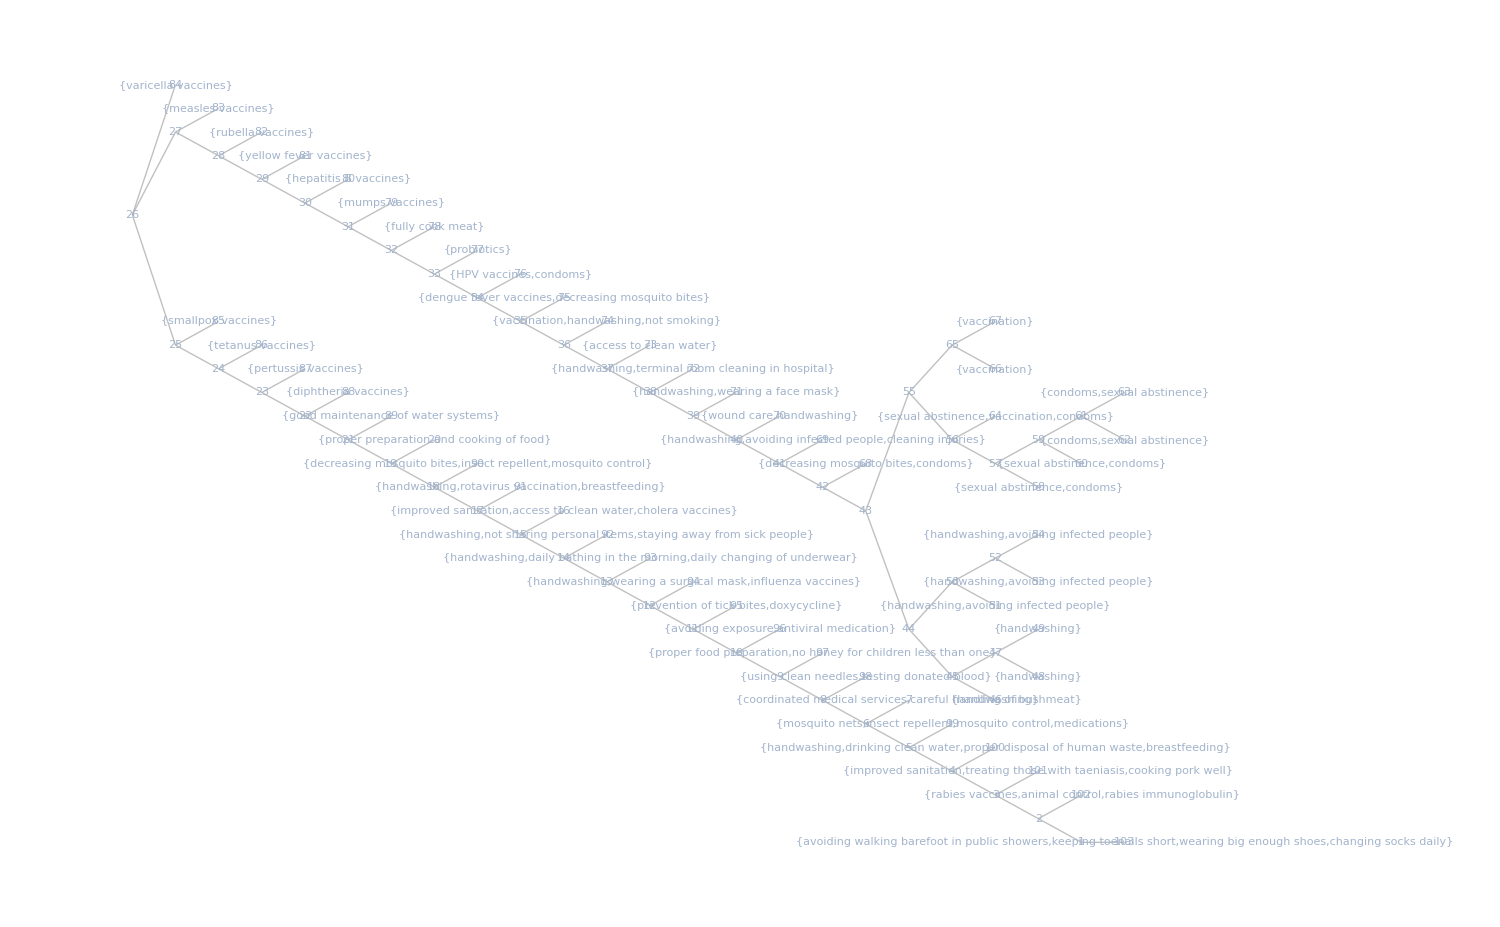

```mathematica
(* similarity between prevention measures *)
Magnify[ClusteringTree[
Values@infectDisPrevention, VertexShapeFunction->"Name", GraphLayout->{"LayeredEmbedding", "Orientation"->Left, "LeafDistance"->1, LayerSizeFunction->(1&)}, 
ImageSize->1500, AspectRatio->1/GoldenRatio], .8]
```

```mathematica
(* exposure to onset. note that data is not available for some entities  *)
infectDisExp = DeleteMissing@ParallelMap[(# -> #[EntityProperty["Disease","ExposureToDiseaseOnset"]])&, infectDis]
```

{Ebola virus disease→(2to21) days,cholera→(1/12 to5) days,salmonella infections→(1/2 to3) days,shigellosis→(1to2) days,botulism→(1/2 to3) days,diphtheria→(2to5) days,streptococcal sore throat→(1to3) days,tetanus→(3to21) days,smallpox→(7to21) days,chicken pox→(10to21) days,genital herpes→(2to12) days,measles→(8to12) days,rubella→14. days,yellow fever→(3to6) days,Dengue fever→(3to14) days,eastern equine encephalitis→(4to10) days,viral hepatitis B without hepatic coma→(72/73 to 432/73) mo,mumps→(14to21) days,hand, foot, and mouth disease→(3to6) days,Condyloma acuminatum→(1to8) mo,unclassified diseases due to viruses and Chlamydiae→(7to21) days,severe acute respiratory syndrome→(2to7) days,unspecified type of chlamydial infection co-occurring with other medical conditions→(14to21) days,rickettsioses→(7to14) days,malaria→(10to15) days,lyme disease→7. days,enterobiasis→(4to8) wk,scabies→(2to6) wk,Legionnaires' disease→(2to10) days,influenza→3. days,Middle East respiratory syndrome→(2to14) days,COVID-19→(2to14) days}

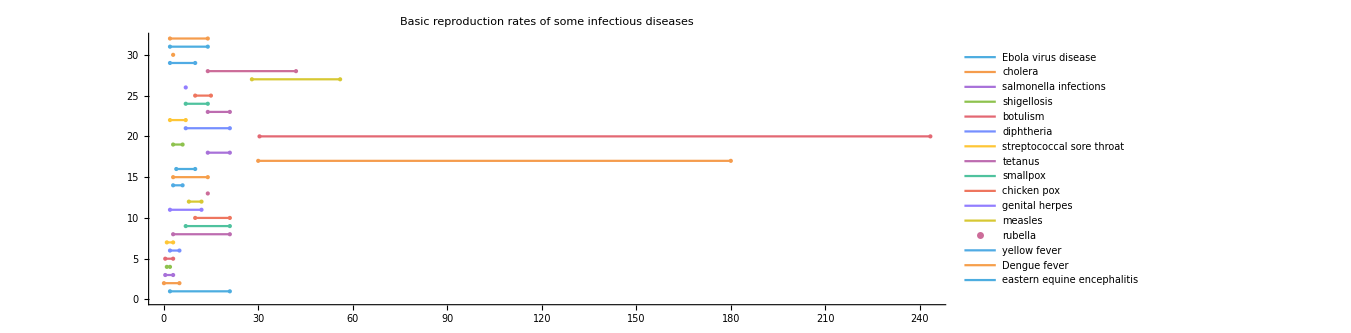

```mathematica
(* plot can be inproved with markers but NumberLinePlot doesn't support this option *)
Quiet@NumberLinePlot[List/@Values[infectDisExp], PlotLegends->Placed[Keys@infectDisExp, Below], PlotTheme->"Detailed", PlotStyle->110, ImageSize->{1000,Automatic}, AspectRatio->1/3, PlotLabel->"Basic reproduction rates of some infectious diseases", AxesLabel->{"Days"}]
```

```mathematica
(* TimelinePlot can't interpret time interval *)
TimelinePlot[Association@infectDisExp, ImageSize->1000, AspectRatio->1/GoldenRatio, PlotLayout->"Stacked", PlotLabel->"Exposure to disease onset time of some infectious diseases", PlotTheme->"Business"]
```

-Graphics-

```mathematica
(* reproduction no. (Subscript[R, 0]) of such diseases. note that data is not available for some entities  *)
infectDisR0 = DeleteMissing@ParallelMap[(# -> #[EntityProperty["Disease","BasicReproductionNumber"]])&, infectDis]
```

{Ebola virus disease→Interval[{1.5,2.5}],diphtheria→Interval[{6.,7.}],whooping cough→5.5,smallpox→Interval[{5.,7.}],measles→Interval[{12.,18.}],rubella→Interval[{5.,7.}],mumps→Interval[{4.,7.}],severe acute respiratory syndrome→Interval[{2.,5.}],influenza→Interval[{2.,3.}],Middle East respiratory syndrome→Interval[{0.6,1.}],COVID-19→Interval[{1.4,2.5}]}

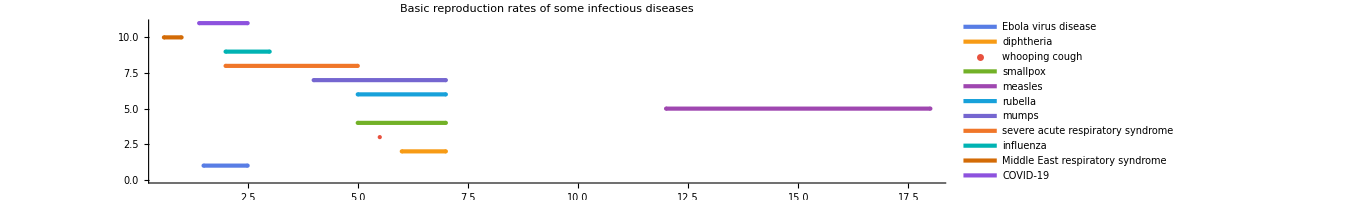

```mathematica
NumberLinePlot[Values@infectDisR0, PlotLegends->Placed[Keys@infectDisR0, Below], PlotTheme->"Business", ImageSize->{1000,Automatic}, AspectRatio->1/5, PlotLabel->"Basic reproduction rates of some infectious diseases"]
```

## Social Media (Twitter)

Social media data on the Covid-19 pandemic can also be explored. For example we can look at discussions and conversations on related to the pandemic on Twitter.

```mathematica
(* connect to Twitter (a Twitter account is required for this) *)
tw = ServiceConnect["Twitter"]
```

ServiceObject[…]

Be mindful of your rate limits when querying the Twitter service. You can see rate limits for queries by running: tw["RateLimit"].

```mathematica
(* possible queries *)
Framed /@ tw /@ {"Requests", "RawRequests"}
```

{{Authentication,FollowerIDs,FollowerMentionNetwork,FollowerNetwork,FollowerReplyToNetwork,Followers,FriendIDs,FriendMentionNetwork,FriendNetwork,FriendReplyToNetwork,Friends,GetTweet,ID,Information,LastTweet,Name,RateLimit,RawRequests,Retweet,SearchMentionNetwork,SearchNetwork,SearchReplyToNetwork,Tweet,TweetEventSeries,TweetList,TweetSearch,TweetTimeline,UserData,UserHashtags,UserIDSearch,UserMentions,UserReplies},{RawAccountStatus,RawAddFavorite,RawBlockIDs,RawBlockList,RawContributees,RawContributors,RawCreateBlock,RawDeleteDirectMessage,RawDeleteTweet,RawDirectMessage,RawDirectMessages,RawDirectMessagesSent,RawFavorites,RawFollowerIDs,RawFollowers,RawFriendIDs,RawFriends,RawFriendship,RawHomeTimeline,RawIncomingFriendships,RawMediaUpload,RawMentionsTimeline,RawMyFriendship,RawNoRetweetUserIDs,RawOutgoingFriendships,RawRemoveBlock,RawRemoveFavorite,RawRetweet,RawRetweeterIDs,RawRetweets,RawRetweetTimeline,RawSendDirectMessage,RawSetUserSettings,RawStartFollowing,RawStatus,RawStatusesLookup,RawStopFollowing,RawSuggestedUserCategories,RawSuggestedUsers,RawSuggestedUserStatuses,RawTrends,RawTrendsAvailable,RawTweetSearch,RawUpdate,RawUpdateBackgroundImage,RawUpdateDevice,RawUpdateFollowing,RawUpdateProfile,RawUpdateProfileColors,RawUpload,RawUser,RawUsers,RawUserSearch,RawUserSettings,RawUserTimeline,RawVerifyCredentials}}

### Trends

```mathematica
(* see available trends around the world; trends are represented by 'woeid' *)
twitterTrends = Dataset[tw["RawTrendsAvailable"], MaxItems->10]
```

```mathematica
(* no. of trends by country *)
twitterTrendsNo = KeyMap[(CountryData@# /. {Entity["Country","NorthKorea"],Entity["Country","SouthKorea"]} -> EntityClass["Country","Korea"])&] @ Rest@twitterTrends[GroupBy@"country", Length];
```

```mathematica
(* plots of no. of trends *)
Echo[GeoRegionValuePlot[#, GeoBackground->GeoStyling["StreetMap", GeoStylingImageFunction->(ColorConvert[#,GrayLevel]&)],
GeoZoomLevel->3, ImageSize->{800, Automatic}], #] &@ twitterTrendsNo;
```

-Graphics-

```mathematica
(* worldwide trends *)
Block[{worldTrends = First@tw["RawTrends", "id"->"1"], data, datestamp},
data = KeyDrop[{"url", "promoted_content"}]@worldTrends@"trends"; 
datestamp = DateObject@worldTrends@"as_of";
Column[{Panel@Row[{"As of:  ", datestamp}], twitterWorldTrends = Dataset[data][SortBy@"tweet_volume"] (* store data in 'twitterWorldTrends' *)
}, Alignment->Center]
]
```

As of:  Fri 22 May 2020 03:12:10GMT+1.

```mathematica
(* group trends by presense of the words "covid" or "corona" *)
twitterWorldTrends[GroupBy[StringContainsQ[#name, "covid"|"corona", IgnoreCase->True]&]]
```

```mathematica
(* extract trend ids for each country, where one is available *)
twitterTrendsIDs = Map[DeleteDuplicates@DeleteCases[#, 1, ∞]&]@
KeyMap[(CountryData@# /. {Entity["Country","NorthKorea"],Entity["Country","SouthKorea"]} -> Entity["Country","SouthKorea"])&] @ Rest@twitterTrends[GroupBy@"country", ;;, "parentid"] //
DeleteCases[#, {}]&
```

```mathematica
(* get top 50 trends in each country, sorted by volume of tweets *)
twitterCountryTrends = twitterTrendsIDs[;;, tw["RawTrends", "id"->ToString@First@#]⟦1, "trends", ;;, {"name", "tweet_volume"}⟧&][;;, SortBy@"tweet_volume"]
```

Dataset[<>]

```mathematica
(* group countries by trends *)
twitterTrendsGrouped = Dataset[Keys/@GroupBy[Flatten[Thread/@Normal@Normal@twitterCountryTrends[;;, ;;, "name"]], Last]][ReverseSortBy@Length];
(* select "covid" and "corona" trends: *)
twitterTrendsGrouped = KeySelect[twitterTrendsGrouped, StringContainsQ[#, "covid"|"corona", IgnoreCase->True]&]
```

### Search

```mathematica
(* search for tweets containing "covid"; Twitter's user API currently only returns up to 100 tweets *)
search=Dataset@tw["RawTweetSearch",{"q"->"*covid*","count"->"100","lang"->"en","result_type"->"mixed","until"->"2020-05-22","include_entities"->"false"}]
```

Dataset[<>]

```mathematica
(* extract tweets from search *)
tweets=search⟦"statuses"⟧;
RandomChoice[tweets,1]
```

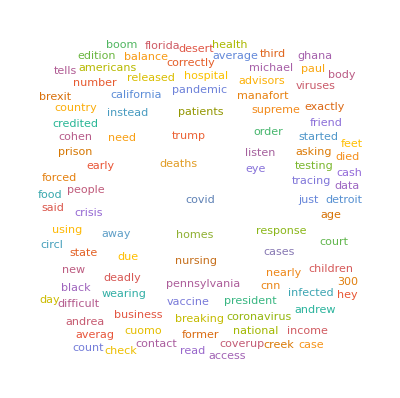

```mathematica
(* wordcloud of tweets *)
DeleteCases[Flatten[ToLowerCase/@DeleteStopwords/@TextWords/@tweets[;;,"text"]],w_/;StringLength[w]<3||StringContainsQ[w,"@"|PunctuationCharacter]]//WordCloud
```

```mathematica
(* user data on informative accounts *)
Dataset@tw["UserData","Username"->{"WHO","CDCgov","NHS","NCDCgov"}]
```

```mathematica
(* get up to 5k WHO tweets *)
whoTweets=tw["TweetList","Username"->"WHO",MaxItems->3000];
```

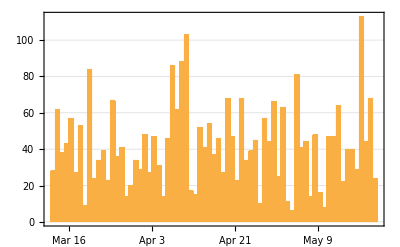

```mathematica
(* date histogram, with day-sized bins *)
DateHistogram[whoTweets[;;,"Date"],"Day",PlotTheme->"Business"]
```

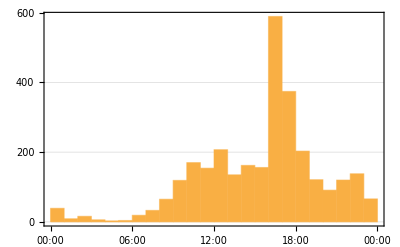

```mathematica
(* date histogram, binned by hour of day *)
DateHistogram[whoTweets[;;,"Date"],DateReduction->"Day",PlotTheme->"Business"]
```

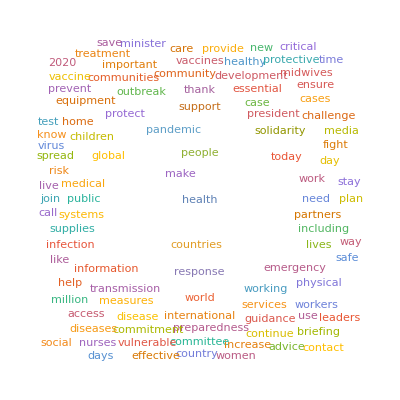

```mathematica
(* wordcloud of WHO tweets *)
DeleteCases[Flatten[ToLowerCase/@DeleteStopwords/@TextWords/@whoTweets[;;,"Text"]],w_/;StringLength[w]<3||StringContainsQ[w,"@"|PunctuationCharacter]]//WordCloud
```

```mathematica
whoTweetsGroupedByDate=KeyMap[StringRiffle]@GroupBy[whoTweets,#["Date"][{"MonthName","Year"}]&]
```

Dataset[<>]

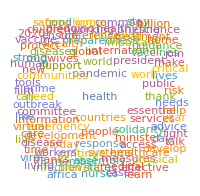
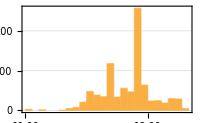
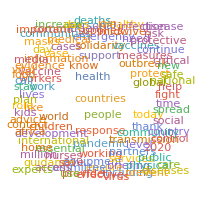
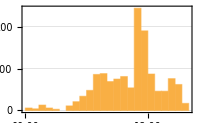
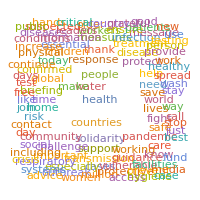
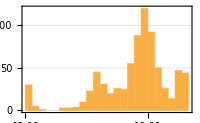
May 2020
-Graphics-
-Graphics-April 2020
-Graphics-
-Graphics-March 2020
-Graphics-
-Graphics-

```mathematica
(* compare WHO tweets over time *)
Table[
Block[{keys = Keys@whoTweetsGroupedByDate, textData, wordcloud, timestamps, dateHistogram},
textData = whoTweetsGroupedByDate[keys⟦i⟧, ;;, "Text"];
wordcloud = WordCloud[DeleteCases[Flatten[ToLowerCase/@DeleteStopwords/@TextWords/@textData], w_ /; StringLength[w]<3 || StringContainsQ[w,"@"|PunctuationCharacter]],ImageSize->200];
timestamps = whoTweetsGroupedByDate[keys⟦i⟧, ;;, "Date"];
dateHistogram = DateHistogram[timestamps, DateReduction->"Day", PlotTheme->"Business", ImageSize->200];
Column[{Style[keys⟦i⟧, "Text"], wordcloud, dateHistogram}, Dividers->Center, FrameStyle->Directive[Thin, LightGray], Spacings->2, Alignment->Center]
], {i, Range@Length@whoTweetsGroupedByDate}] // Row[#, Spacer[10]]&
```

## Data (CSSE COVID-19 Daily Reports)

The importance of going through the Github links and getting latest data is that the entire process can be automated easily. Whereas, getting the latest data from Kaggle and doing some manual file operations can’t.

```mathematica
(* JHU CSSEGIS Github repository, where data is automatically updated daily *)
githubURL="https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports";
```

```mathematica
(* all hyperlinks in repo *)
githubLinks=Import[githubURL,"Hyperlinks"];
Short[githubLinks,5]
```

{https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports,«788»,https://github.com/CSSEGISandData/COVID-19/tree/master/csse_covid_19_data/csse_covid_19_daily_reports}

```mathematica
(* get links to .CSV files *)
githubLinksCSV=Cases[githubLinks,l_/;StringEndsQ[l,".csv"],∞];
{Highlighted@Length@githubLinksCSV,Short@githubLinksCSV}
```

{365,{https://github.com/CSSEGISandDat…_19_daily_reports/01-01-2021.csv,«363»,…}}

```mathematica
(* create a date->URL association for each day's data URL. this is reverse date-sorted (latest to earliest) *)
Off[DateObject::ambig]; (* we're taking care of ambiguity of day-month thing by specifying $DateStringFormat, so we'll turn this off *)

dateURLAssoc=Block[{$DateStringFormat={"Month","-","Day","-","Year"},url,date},
url=#;
date=Last@StringSplit[url,"/"];
<|"Date"->DateObject@date,"Link"->Hyperlink@url|>
]&/@githubLinksCSV//ReverseSort;

Short@dateURLAssoc
```

{<|Date→Wed 20 Jan 2021,Link→https://git…20-2021.csv|>,«363»,«1»}

```mathematica
(* range of data we have *)
dateInterval=MinMax["Date"/.dateURLAssoc]
DateDifference@@dateInterval
```

{Wed 22 Jan 2020,Wed 20 Jan 2021}

364 days

```mathematica
(* "dataset" of datasets we've got so far *)
Column[{
(* range *) Panel@StringForm["Date range:  `1` to `2`  (`3`)",Sequence@@#,DateDifference@@#]&@dateInterval,
(* ds *)(dateURLDataset=Dataset@dateURLAssoc)
},Alignment->Center]
```

Date range:  Wed 22 Jan 2020 to Wed 20 Jan 2021  (364)

```mathematica
(* from the dataset above, we can very conveniently get data for a given day within the data range *)
(* we can see that we have data for yesterday, but not yet for today and tomorrow. Note that times are based on US timezone (presumably same as the CSSE). *)
Between[#,dateInterval]&/@{Yesterday,Today,Tomorrow}
```

{True,False,False}

```mathematica
First@dateURLDataset[Select[#"Date"==Yesterday&],"Link"]
```

https://github.com/CSSEGISandData/COVID-19/blob/master/csse_covid_19_data/csse_covid_19_daily_reports/01-20-2021.csv

```mathematica
(* we can now simply specify a date to get it's data. we can make this work even for natural lang. inputs. *)
First@dateURLDataset[Select[#"Date"==Yesterday&],"Link"]
First@dateURLDataset[Select[#"Date"==SemanticInterpretation["2 days ago"]&],"Link"]
First@dateURLDataset[Select[#"Date"==SemanticInterpretation["last Tuesday"]&],"Link"]
```

https://github.com/CSSEGISandData/COVID-19/blob/master/csse_covid_19_data/csse_covid_19_daily_reports/01-20-2021.csv

## Data prep and preprocessing

### Raw dataset

```mathematica
(* let's explore the latest data we have *)
exploreDataURL=StringReplace[dateURLAssoc⟦1,2,1⟧,{"github"->"raw.githubusercontent","blob/"->""}]//Hyperlink
```

https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_daily_reports/01-20-2021.csv

```mathematica
(* import raw data *)
exploreDataRaw=Import@exploreDataURL;
```

```mathematica
(* table view of raw data *)
TableView[exploreDataRaw,ImageSize->1000]
```

FIPSAdmin2Province_StateCountry_RegionLast_UpdateLatLong_ConfirmedDeathsRecoveredActiveCombined_KeyIncident_RateCase_Fatality_RatioAfghanistan2021-01-21 05:22:0133.9391167.709953542782354467595165Afghanistan139.430550097164434.3369320903496815Albania2021-01-21 05:22:0141.153320.16836923812914196925978Albania2405.93508930432971.8645830324388342Algeria2021-01-21 05:22:0128.03391.659610460628497112730630Algeria238.548487888874122.723553142267174Andorra2021-01-21 05:22:0142.50631.52189308928399817Andorra12046.851743997930.9883970777825526Angola2021-01-21 05:22:01-11.202717.873919093444169211728Angola58.092996746694822.325459592520819Antigua and Barbuda2021-01-21 05:22:0117.0608-61.7964190615727Antigua and Barbuda194.020096397353173.1578947368421053Argentina2021-01-21 05:22:01-38.4161-63.61671831681462161613773171692Argentina4052.77024001600882.523146770644015Armenia2021-01-21 05:22:0140.069145.038216522130161538578348Armenia5575.6987129602321.825433812893034Australian Capital TerritoryAustralia2021-01-21 05:22:01-35.4735149.012411831150Australian Capital Territory, Australia27.5636533520205552.542372881355932New South WalesAustralia2021-01-21 05:22:01-33.8688151.209350845432361794New South Wales, Australia62.6262626262626161.0621557828481512Northern TerritoryAustralia2021-01-21 05:22:01-12.4634130.8456960879Northern Territory, Australia39.087947882736160.QueenslandAustralia2021-01-21 05:22:01-27.4698153.025113006126133Queensland, Australia25.412960609911050.46153846153846156South AustraliaAustralia2021-01-21 05:22:01-34.9285138.600759645875South Australia, Australia33.9311130088243760.6711409395973155TasmaniaAustralia2021-01-21 05:22:01-42.8821147.3272234132210Tasmania, Australia43.697478991596645.555555555555555VictoriaAustralia2021-01-21 05:22:01-37.8136144.9631204338201957934Victoria, Australia308.194693735953764.013116037782019Western AustraliaAustralia2021-01-21 05:22:01-31.9505115.8605888986613Western Australia, Australia33.756557439367451.0135135135135136Austria2021-01-21 05:22:0147.516214.5501398096723737482416035Austria4420.1456741872441.8179032193239821Azerbaijan2021-01-21 05:22:0140.143147.576922802830442176177367Azerbaijan2248.97982330909551.334923781290017Bahamas2021-01-21 05:22:0125.025885-78.035889807517567201180Bahamas2053.4115875986652.1671826625387Bahrain2021-01-21 05:22:0126.027550.5598573366952402967Bahrain5793.0174431690960.37129842857577633Bangladesh2021-01-21 05:22:0123.68590.3563529687795047447247265Bangladesh321.627897531196651.5008863725181099Barbados2021-01-21 05:22:0113.1939-59.543211569493654Barbados402.26745217854270.7785467128027682Belarus2021-01-21 05:22:0153.709827.9534230494161021436614518Belarus2439.26521281264560.6984997440280442AntwerpBelgium2021-01-21 05:22:0151.21954.4024849350084935Antwerp, Belgium4571.34768507405350.BrusselsBelgium2021-01-21 05:22:0150.85034.3517858210085821Brussels, Belgium7101.2012822061620.East FlandersBelgium2021-01-21 05:22:0151.03623.7373701640070164East Flanders, Belgium4631.0914918445690.Flemish BrabantBelgium2021-01-21 05:22:0150.91674.5833520540052054Flemish Brabant, Belgium4541.540340698410.HainautBelgium2021-01-21 05:22:0150.52574.062110614800106148Hainaut, Belgium7896.500701883070.LiegeBelgium2021-01-21 05:22:0150.44965.8492996770099677Liege, Belgium9004.3107809270530.LimburgBelgium2021-01-21 05:22:0150.97395.3420000000000005321200032120Limburg, Belgium3674.8553855165850.LuxembourgBelgium2021-01-21 05:22:0150.05475.4677193540019354Luxembourg, Belgium6799.5137683654330.NamurBelgium2021-01-21 05:22:0150.3314.8221367180036718Namur, Belgium7427.9067415162080.UnknownBelgium2021-01-21 05:22:0111989205720-8583Unknown, Belgium171.5906247393444Walloon BrabantBelgium2021-01-21 05:22:0150.44.35264100026410Walloon Brabant, Belgium6543.6237453512020.West FlandersBelgium2021-01-21 05:22:0151.05363.1458588660058866West Flanders, Belgium4922.74602022418550.Belize2021-01-21 05:22:0117.1899-88.49761164228610911445Belize2927.9137671300062.4566225734409897Benin2021-01-21 05:22:019.30772.31583557463284227Benin29.3404430085196961.29322462749508Bhutan2021-01-21 05:22:0127.514290.43368501631218Bhutan110.15899182490680.11764705882352941Bolivia2021-01-21 05:22:01-16.2902-63.5887193745976414657837403Bolivia1659.76628688235095.0396139255206585Bosnia and Herzegovina2021-01-21 05:22:0143.915917.679111871745218907525121Bosnia and Herzegovina3618.52161734203173.8082161779694568Botswana2021-01-21 05:22:01-22.328524.68491863088146243918Botswana792.21814702599270.4723564143853999AcreBrazil2021-01-21 05:22:01-9.0238-70.81245429840389705619Acre, Brazil5151.0598853657011.8490391600079243AlagoasBrazil2021-01-21 05:22:01-9.5713-36.78211247626471064953334Alagoas, Brazil3370.21181731531852.3533909456239552AmapaBrazil2021-01-21 05:22:010.902-52.0037431010165645516839Amapa, Brazil8786.481753654531.3672453236441933AmazonasBrazil2021-01-21 05:22:01-3.4168-65.8561238980659819805334329Amazonas, Brazil5766.0612117414552.7609004937651687BahiaBrazil2021-01-21 05:22:01-12.5797-41.7007549315972852419415393Bahia, Brazil3693.3546443422821.7709328891437517CearaBrazil2021-01-21 05:22:01-5.4984-39.32063569851024327917067572Ceara, Brazil3909.1321821824122.8693082342395337Distrito FederalBrazil2021-01-21 05:22:01-15.7998-47.864526650644422546277437Distrito Federal, Brazil8838.5510011050431.666754219417199Espirito SantoBrazil2021-01-21 05:22:01-19.1834-40.3089280067558225921315272Espirito Santo, Brazil6969.1811926890871.9930945095280772GoiasBrazil2021-01-21 05:22:01-15.827-49.836233313471853197406209Goias, Brazil4746.61152743221652.1567897602766455MaranhaoBrazil2021-01-21 05:22:01-4.9609-45.274420430046241930286648Maranhao, Brazil2887.55863630909242.2633382280959373Mato GrossoBrazil2021-01-21 05:22:01-12.6819-56.9211202559480518756610188Mato Grosso, Brazil5813.2006453786612.372148361711896Mato Grosso do SulBrazil2021-01-21 05:22:01-20.7722-54.7852153057272313637213962Mato Grosso do Sul, Brazil5507.6563897767031.7790757691578953Minas GeraisBrazil2021-01-21 05:22:01-18.5122-44.5556593851372157697868686Minas Gerais, Brazil3114.89210697011462.0808783942613194ParaBrazil2021-01-21 05:22:01-1.9981-54.9306312632743429175513443Para, Brazil3634.0451698358632.377875585352747ParaibaBrazil2021-01-21 05:22:01-7.24-36.782179353392613389441533Paraiba, Brazil4463.5970938698562.188979275506961ParanaBrazil2021-01-21 05:22:01-25.2521-52.02155123379186371608131543Parana, Brazil4480.8372114745581.792960492800637PernambucoBrazil2021-01-21 05:22:01-8.8137-36.95412448141009820747827238Pernambuco, Brazil2561.60072474087474.124764106627889PiauiBrazil2021-01-21 05:22:01-7.7183-42.72891529972976149555466Piaui, Brazil4674.19460978416651.9451361791407675Rio Grande do NorteBrazil2021-01-21 05:22:01-5.4026-36.954113229431929164537457Rio Grande do Norte, Brazil3772.4421297385442.4128078370901176Rio Grande do SulBrazil2021-01-21 05:22:01-30.0346-51.21775162881012348542720738Rio Grande do Sul, Brazil4537.90238563152251.960727345977439Rio de JaneiroBrazil2021-01-21 05:22:01-22.9068-43.1729490821282154587753831Rio de Janeiro, Brazil2842.876457802385.7485315420489345RondoniaBrazil2021-01-21 05:22:01-11.5057-63.580611246820568987520537Rondonia, Brazil6328.2927035124981.8280755414873564RoraimaBrazil2021-01-21 05:22:01-2.7376-62.075171451816680352600Roraima, Brazil11795.2459798501391.1420413990007139Santa CatarinaBrazil2021-01-21 05:22:01-27.2423-50.2189549579598852234121250Santa Catarina, Brazil7670.5549417512411.089561282363409Sao PauloBrazil2021-01-21 05:22:01-23.5505-46.63331658636506521415873192111Sao Paulo, Brazil3612.0870011920323.0538345966203555SergipeBrazil2021-01-21 05:22:01-10.5741-37.3857130286268511540612195Sergipe, Brazil5667.8221043582972.060850743748369TocantinsBrazil2021-01-21 05:22:01-10.1753-48.29829779013308555210908Tocantins, Brazil6217.3128543690311.3600572655690766Brunei2021-01-21 05:22:014.5353114.727717431692Brunei39.772974035562531.7241379310344827Bulgaria2021-01-21 05:22:0142.733925.4858213409865117509829660Bulgaria3071.320273816664.053718446738422Burkina Faso2021-01-21 05:22:0112.2383-1.5616955310676371810Burkina Faso45.7009661355506151.1095990788234062Burma2021-01-21 05:22:0121.916295.956135721299711931413410Burma249.442223582026462.2082065413605854Burundi2021-01-21 05:22:01-3.373129.918913222773547Burundi11.117856766515170.15128593040847202Cabo Verde2021-01-21 05:22:0116.5388-23.04181322412112400703Cabo Verde2378.46860004172780.9150030248033878Cambodia2021-01-21 05:22:0111.55104.9167453039657Cambodia2.7094968942765680.Cameroon2021-01-21 05:22:013.84811.50212801045526861694Cameroon105.515495747284771.6244198500535523AlbertaCanada2021-01-21 05:22:0153.9333-116.5765118436148410638710565Alberta, Canada2683.7090819111811.2529973994393597British ColumbiaCanada2021-01-21 05:22:0153.7267-127.6476624121104555645744British Columbia, Canada1221.15072500688261.7688905979619305Diamond PrincessCanada2020-12-21 13:27:30010Diamond Princess, CanadaGrand PrincessCanada2020-12-21 13:27:30130130Grand Princess, Canada0.ManitobaCanada2021-01-21 05:22:0153.7609-98.813927893788239683137Manitoba, Canada2024.87519210289252.8250815616821425New BrunswickCanada2021-01-21 05:22:0146.5653-66.4619102513694318New Brunswick, Canada131.41143574365411.2682926829268293Newfoundland and LabradorCanada2021-01-21 05:22:0153.1355-57.660439643848Newfoundland and Labrador, Canada75.954465681432411.0101010101010102Northwest TerritoriesCanada2021-01-21 05:22:0164.8255-124.8457310247Northwest Territories,Canada69.036166043114180.Nova ScotiaCanada2021-01-21 05:22:0144.682-63.7443156465147623Nova Scotia, Canada160.007038672800974.156010230179028NunavutCanada2021-01-21 05:22:0170.2998-83.107626612650Nunavut, Canada685.92057761732850.37593984962406013OntarioCanada2021-01-21 05:22:0151.2538-85.3232249753558721923124935Ontario, Canada1697.63415515965522.2370101660440516Prince Edward IslandCanada2021-01-21 05:22:0146.5107-63.416811001037Prince Edward Island, Canada69.550702462094860.QuebecCanada2021-01-21 05:22:0152.9399-73.5491247236914221959218502Quebec, Canada2895.82385085211673.697681567409277Repatriated TravellersCanada2021-01-21 05:22:01130130Repatriated Travellers, Canada0.SaskatchewanCanada2021-01-21 05:22:0152.9399-106.450921112226171843702Saskatchewan, Canada1786.63006297887891.070481242895036YukonCanada2021-01-21 05:22:0164.2823-135.701690Yukon, Canada170.407517405910681.4285714285714286Central African Republic2021-01-21 05:22:016.611120.9394497463488526Central African Republic102.986398507256241.2665862484921593Chad2021-01-21 05:22:0115.454218.732230121142178720Chad18.336940552089243.7848605577689245AntofagastaChile2021-01-21 05:22:01-23.6509-70.397528282605258751802Antofagasta, Chile4655.2127123749452.1391697899724207AraucaniaChile2021-01-21 05:22:01-38.9489-72.331128440364265421534Araucania, Chile2971.09140598229941.279887482419128Arica y ParinacotaChile2021-01-21 05:22:01-18.594-69.47851198224511169568Arica y Parinacota, Chile5300.1751685333622.044733767317643AtacamaChile2021-01-21 05:22:01-27.5661-70.050393761208932324Atacama, Chile3244.91943075474771.2798634812286689AysenChile2021-01-21 05:22:01-45.9864-73.76692156181920218Aysen, Chile2089.9978673491150.8348794063079777BiobioChile2021-01-21 05:22:01-37.4464-72.141656069956522552858Biobio, Chile3601.542903574951.705042001819187CoquimboChile2021-01-21 05:22:01-29.959-71.33891568332214825536Coquimbo, Chile2070.12801186927942.0531786010329656Los LagosChile2021-01-21 05:22:01-41.9198-72.141635305319316603326Los Lagos, Chile4260.246069785740.9035547372893358Los RiosChile2021-01-21 05:22:01-40.231-72.331112359127109561276Los Rios, Chile3211.4895397272091.02759122906384MagallanesChile2021-01-21 05:22:01-52.368-70.98631887325118128494Magallanes, Chile11332.888976959521.3299422455359509MauleChile2021-01-21 05:22:01-35.5183-71.688531783631290232129Maule, Chile3041.5809368869321.9853380738130446MetropolitanaChile2021-01-21 05:22:01-33.4376-70.6505333879111193179724788Metropolitana, Chile4694.0533190267473.33024838339638NubleChile2021-01-21 05:22:01-36.7226-71.76221252224411604674Nuble, Chile2605.44434249046531.9485705158920301OHigginsChile2021-01-21 05:22:01-34.5755-71.00222410563022565910OHiggins, Chile2635.70807660556242.613565650280025TarapacaChile2021-01-21 05:22:01-19.9232-69.513219418319178451254Tarapaca, Chile5874.3095009045311.6428056442476053UnknownChile2021-01-21 05:22:0152152Unknown, Chile1.9230769230769231ValparaisoChile2021-01-21 05:22:01-33.0472-71.6127404561323377681365Valparaiso, Chile2227.87353062004473.2702194977259245AnhuiChina2021-01-21 05:22:0131.8257117.226499369870Anhui, China1.57020872865275150.6042296072507553BeijingChina2021-01-21 05:22:0140.1824116.41421017996444Beijing, China4.72144846796657450.8849557522123894ChongqingChina2021-01-21 05:22:0130.0572107.87459165841Chongqing, China1.90522243713733071.015228426395939FujianChina2021-01-21 05:22:0126.0789117.9874533151319Fujian, China1.35244861710225850.18761726078799248GansuChina2021-01-21 05:22:0135.7518104.286118221800Gansu, China0.69017823284034881.098901098901099GuangdongChina2021-01-21 05:22:0123.3417113.424420948204739Guangdong, China1.84558434690639880.38204393505253104GuangxiChina2021-01-21 05:22:0123.8298108.788126722623Guangxi, China0.54202192448233870.7490636704119851GuizhouChina2021-01-21 05:22:0126.8154106.874814721450Guizhou, China0.40833333333333331.3605442176870748HainanChina2021-01-21 05:22:0119.1959109.745317161650Hainan, China1.83083511777301953.508771929824561HebeiChina2021-01-21 05:22:0137.8957114.904212317395829Hebei, China1.62916887241926940.5686433793663688HeilongjiangChina2021-01-21 05:22:0147.862127.7615122713955259Heilongjiang, China3.25205406838059831.0594947025264874HenanChina2021-01-21 05:22:0133.882113.61413032212765Henan, China1.35658511192087451.6884113584036837Hong KongChina2021-01-21 05:22:0122.3114.297971668865766Hong Kong, China130.679147412267441.6943962437480862HubeiChina2021-01-21 05:22:0130.9756112.2707681504512636371Hubei, China115.176609768463766.620689655172414HunanChina2021-01-21 05:22:0127.6104111.70881026410175Hunan, China1.48717205392085820.3898635477582846Inner MongoliaChina2021-01-21 05:22:0144.0935113.9448366135114Inner Mongolia, China1.44435674822415150.273224043715847JiangsuChina2021-01-21 05:22:0132.9711119.45568806844Jiangsu, China0.85455222953670350.JiangxiChina2021-01-21 05:22:0127.614115.722193519340Jiangxi, China2.0116179001721170.10695187165775401JilinChina2021-01-21 05:22:0143.6661126.19233192155162Jilin, China1.17973372781065080.6269592476489029LiaoningChina2021-01-21 05:22:0141.2956122.6085396236925Liaoning, China0.90846524432209220.5050505050505051MacauChina2021-01-21 05:22:0122.1667113.55460460Macau, China7.0840943601368790.NingxiaChina2021-01-21 05:22:0137.2692106.1655750750Ningxia, China1.09011627906976740.QinghaiChina2021-01-21 05:22:0135.745295.9956180180Qinghai, China0.298507462686567140.ShaanxiChina2021-01-21 05:22:0135.1917108.8701533350426Shaanxi, China1.3793995859213250.5628517823639775ShandongChina2021-01-21 05:22:0136.3427118.149886678563Shandong, China0.86194884044988550.8083140877598153ShanghaiChina2021-01-21 05:22:0131.202121.449116157151395Shanghai, China6.6625412541254120.43343653250773995ShanxiChina2021-01-21 05:22:0137.5777112.292223002246Shanxi, China0.61861215707369550.SichuanChina2021-01-21 05:22:0130.6171102.7103865385210Sichuan, China1.03704591775566480.3468208092485549TianjinChina2021-01-21 05:22:0139.3054117.323335330824Tianjin, China2.14743589743589740.8955223880597015TibetChina2021-01-21 05:22:0131.692788.09241010Tibet, China0.029069767441860460.XinjiangChina2021-01-21 05:22:0141.112985.240198039770Xinjiang, China3.9404905508644960.30612244897959184YunnanChina2021-01-21 05:22:0124.974101.48723122254Yunnan, China0.47826086956521740.8658008658008658ZhejiangChina2021-01-21 05:22:0129.1832120.093413161129817Zhejiang, China2.29388181976642840.07598784194528875AmazonasColombia2021-01-21 05:22:01-1.4429-71.57243483132329160Amazonas, Colombia4547.6504458864853.789836347975883AntioquiaColombia2021-01-21 05:22:017.1986-75.3412310692550628772617460Antioquia, Colombia4849.1814239885681.7721730845982517AraucaColombia2021-01-21 05:22:017.0762-70.710550861474666273Arauca, Colombia1939.93302158108762.8902870625245773AtlanticoColombia2021-01-21 05:22:0110.6966-74.87411079953678997374580Atlantico, Colombia4259.28913117127653.4057132274642345BolivarColombia2021-01-21 05:22:018.6704-74.03604791207569502322Bolivar, Colombia2921.53557057354371.995734056449346BoyacaColombia2021-01-21 05:22:015.4545-73.36237296767333483181Boyaca, Colombia3063.63851431275132.0565208065208065CaldasColombia2021-01-21 05:22:015.2983-75.247940595775367063114Caldas, Colombia4066.5962103871251.9091021061707107Capital DistrictColombia2021-01-21 05:22:014.711-74.07215719511158051423246139Capital District, Colombia7715.9650247970812.0246489646840375CaquetaColombia2021-01-21 05:22:010.8699-73.84191607057214816682Caqueta, Colombia4002.60032030765523.5594275046670814CasanareColombia2021-01-21 05:22:015.7589-71.5724105962059683708Casanare, Colombia2519.8333428457281.9346923367308417CaucaColombia2021-01-21 05:22:012.705-76.8260000000000223072566207801726Cauca, Colombia1575.43114043952552.4531900138696257CesarColombia2021-01-21 05:22:019.3373-73.6536367771050342091518Cesar, Colombia3063.28472880472242.8550452728607554ChocoColombia2021-01-21 05:22:015.2528-76.8260000000000255361725076288Choco, Colombia1035.1030054634593.106936416184971CordobaColombia2021-01-21 05:22:018.0493-75.57431254169528931628Cordoba, Colombia1751.13725310023695.423305816855443CundinamarcaColombia2021-01-21 05:22:015.026-74.03858092134776915984Cundinamarca, Colombia2939.6106965941092.48691862158981GuainiaColombia2021-01-21 05:22:012.5854-68.5247125220121913Guainia, Colombia2602.15321943717031.597444089456869GuaviareColombia2021-01-21 05:22:011.0654-73.2603210438203135Guaviare, Colombia2542.0759481435841.806083650190114HuilaColombia2021-01-21 05:22:012.5359-75.5277423341311384142609Huila, Colombia3847.19543869151363.096801625171257La GuajiraColombia2021-01-21 05:22:0111.3548-72.52051515358014176397La Guajira, Colombia1720.83674025620053.8276248927605097MagdalenaColombia2021-01-21 05:22:0110.4113-74.4057281201144257981178Magdalena, Colombia2095.7766969307164.068278805120911MetaColombia2021-01-21 05:22:013.272-73.087738578833362401505Meta, Colombia3710.41489936733022.1592617554046347NarinoColombia2021-01-21 05:22:011.2892-77.3579418391193368293817Narino, Colombia2565.8779142789862.851406582375296Norte de SantanderColombia2021-01-21 05:22:017.9463-72.8988465122387419692156Norte de Santander, Colombia3118.07622098171945.132008943928448PutumayoColombia2021-01-21 05:22:010.436-75.527769002686139493Putumayo, Colombia1981.722202756033.8840579710144927QuindioColombia2021-01-21 05:22:014.461-75.667428204786259401478Quindio, Colombia5223.8916548127072.786838746277124RisaraldaColombia2021-01-21 05:22:015.3158-75.992841873945385572371Risaralda, Colombia4438.5155411113622.256824206529267San Andres y ProvidenciaColombia2021-01-21 05:22:0112.5567-81.7185256442247745San Andres y Providencia, Colombia4184.0731070496091.6380655226209049SantanderColombia2021-01-21 05:22:016.6437-73.6536788002729717634308Santander, Colombia3606.67637906168833.463197969543147SucreColombia2021-01-21 05:22:018.814-74.72331846869317300475Sucre, Colombia2040.97194823967863.7524366471734893TolimaColombia2021-01-21 05:22:014.0925-75.1545572251651517793795Tolima, Colombia4302.0267075230782.8851026649191787UnknownColombia2021-01-21 05:22:010000Unknown, ColombiaValle del CaucaColombia2021-01-21 05:22:013.8009-76.641315802149531454107658Valle del Cauca, Colombia3530.4965318598373.134393529973864VaupesColombia2021-01-21 05:22:010.8554-70.81211431311264Vaupes, Colombia2801.6765938671961.1373578302712162VichadaColombia2021-01-21 05:22:014.4234-69.2878119820116117Vichada, Colombia1111.2347877708521.669449081803005Comoros2021-01-21 05:22:01-11.645543.33331933541210669Comoros222.287386657006982.793585100879462Congo (Brazzaville)2021-01-21 05:22:01-0.22815.8277770911458461749Congo (Brazzaville)139.704086122522061.4787910234790504Congo (Kinshasa)2021-01-21 05:22:01-4.038321.758721302640148345828Congo (Kinshasa)23.7847990859991473.0044127311989484Costa Rica2021-01-21 05:22:019.7489-83.7534187712249214487740343Costa Rica3684.8802362883911.327565632458234Cote d'Ivoire2021-01-21 05:22:017.54-5.547125597142238671588Cote d'Ivoire97.038187675274430.5547525100597727Croatia2021-01-21 05:22:0145.115.222655047112183583481Croatia5518.5191320030752.0794526594570737Cuba2021-01-21 05:22:0121.521757-77.7811670000000219122180144914451Cuba168.823592147910720.9413241292751804Cyprus2021-01-21 05:22:0135.126433.429929472176205727239Cyprus2441.0263376073930.5971769815418024Czechia2021-01-21 05:22:0149.817515.47390913114820767750126561Czechia8489.4250452564031.6301281113502895Faroe IslandsDenmark2021-01-21 05:22:0161.8926-6.911865216447Faroe Islands, Denmark1334.28834544152260.15337423312883436GreenlandDenmark2021-01-21 05:22:0171.7069-42.6043300291Greenland, Denmark52.84295075036990.Denmark2021-01-21 05:22:0156.26399.5018191505187217437415259Denmark3306.2549775966070.9775201691861831Diamond Princess2021-01-21 05:22:01712136990Diamond Princess1.8258426966292134Djibouti2021-01-21 05:22:0111.825142.5903591361582824Djibouti598.48056987738881.0316252325384745Dominica2021-01-21 05:22:0115.415-61.37111301049Dominica156.964064952563550.Dominican Republic2021-01-21 05:22:0118.7357-70.1627198123247014568149972Dominican Republic1826.37125107301861.2467002821479587Ecuador2021-01-21 05:22:01-1.8312-78.18342343151443719933220546Ecuador1328.08594427497276.161363975844483Egypt2021-01-21 05:22:0126.82055300000000430.802498158963874712460525611Egypt155.336812782305515.502538326528815El Salvador2021-01-21 05:22:0113.7942-88.8965514371521452234693El Salvador793.02198621350162.9570153780352664Equatorial Guinea2021-01-21 05:22:011.650810.2679536586519188Equatorial Guinea382.39895651058281.602982292637465Eritrea2021-01-21 05:22:0115.179439.7823191061234670Eritrea53.857022857089680.31413612565445026Estonia2021-01-21 05:22:0158.595325.0136385443492810710088Estonia2905.6062430128330.905458696554587Eswatini2021-01-21 05:22:01-26.522531.46591378942786524710Eswatini1188.53886174713263.0966712596997605Ethiopia2021-01-21 05:22:019.14540.4897132034204411735312637Ethiopia114.848542951205691.548086099035097Fiji2021-01-21 05:22:01-17.7134178.065552530Fiji6.1353525708242793.6363636363636362Finland2021-01-21 05:22:0161.9241125.74815141166632310009534Finland742.97230070182241.5352475343730263French GuianaFrance2021-01-21 05:22:014.-53.151877699955116French Guiana, France5084.671992286110.5004279976295516French PolynesiaFrance2021-01-21 05:22:01-17.6797-149.406817697127484212728French Polynesia, France6300.017087688320.717635757473018GuadeloupeFrance2021-01-21 05:22:0116.265-61.551894815622426550Guadeloupe, France2236.28997793200641.743406347787215MartiniqueFrance2021-01-21 05:22:0114.6415-61.0242630244986160Martinique, France1679.34659507281530.6981910504601714MayotteFrance2021-01-21 05:22:01-12.827545.16624469185829643896Mayotte, France2535.80291261780080.838392599017057New CaledoniaFrance2021-01-21 05:22:01-20.904305165.618042440431New Caledonia, France15.4120445127867440.ReunionFrance2021-01-21 05:22:01-21.115155.53649552459053454Reunion, France1066.89541476229440.47110552763819097Saint BarthelemyFrance2021-01-21 05:22:0117.9-62.8333300120495Saint Barthelemy, France3034.9013657056150.3333333333333333Saint Pierre and MiquelonFrance2021-01-21 05:22:0146.8852-56.3159160160Saint Pierre and Miquelon, France276.100086281276960.St MartinFrance2021-01-21 05:22:0118.0708-63.05011146121006128St Martin, France2964.38086862050251.0471204188481675Wallis and FutunaFrance2021-01-21 05:22:01-14.2938-178.11654013Wallis and Futuna, France26.1626005624959070.France2021-01-21 05:22:0146.22762.21372957547712731888902697123France4530.606534546512.4098687189079326Gabon2021-01-21 05:22:01-0.803711.609410120669809245Gabon454.682692584179160.6521739130434783Gambia2021-01-21 05:22:0113.4432-15.310139381283697113Gambia162.95190394692853.250380904012189Georgia2021-01-21 05:22:0142.315443.3569249934298723692210025Georgia6265.3054829632691.1951155104947706Baden-WurttembergGermany2021-01-21 05:22:0148.66169.3501279479641924227230788Baden-Wurttemberg, Germany2524.7587228837932.2967736395221108BayernGermany2021-01-21 05:22:0148.790411.4979383107928232965144174Bayern, Germany2929.68703698733042.4228218226239666BerlinGermany2021-01-21 05:22:0152.5213.40511461619579900113658Berlin, Germany3144.6219929291551.7074404969637746BrandenburgGermany2021-01-21 05:22:0152.412512.53166275419794815212623Brandenburg, Germany2498.2513355337773.1535838352933676BremenGermany2021-01-21 05:22:0153.07938.801715151240138171094Bremen, Germany2218.3470817849851.5840538578311663HamburgGermany2021-01-21 05:22:0153.55119.993743620950359166754Hamburg, Germany2369.1341254706912.177900045850527HessenGermany2021-01-21 05:22:0150.65219.1624162321425713735420710Hessen, Germany2590.5832750407812.622581181732493Mecklenburg-VorpommernGermany2021-01-21 05:22:0153.612712.429617553340138223391Mecklenburg-Vorpommern, Germany1090.46857284855631.9369908277787273NiedersachsenGermany2021-01-21 05:22:0152.63679.8451132095282911539513871Niedersachsen, Germany1654.81817106732142.141640486013854Nordrhein-WestfalenGermany2021-01-21 05:22:0151.43327.6616460709963539895152123Nordrhein-Westfalen, Germany2569.1070439055552.091341823146498Rheinland-PfalzGermany2021-01-21 05:22:0150.11837.3098704021877106313790Rheinland-Pfalz, Germany2130.8035264014982.512637867647059SaarlandGermany2021-01-21 05:22:0149.39647.02323894671214091814Saarland, Germany2412.29509272505362.8082363773332215SachsenGermany2021-01-21 05:22:0151.104513.2017170784543314280022551Sachsen, Germany4187.9999617453633.181211354693648Sachsen-AnhaltGermany2021-01-21 05:22:0151.950311.6923456991316352849099Sachsen-Anhalt, Germany2069.40023665037822.8797129040022758Schleswig-HolsteinGermany2021-01-21 05:22:0154.21949.696132297707258725718Schleswig-Holstein, Germany1114.9537820812012.1890578072266775ThuringenGermany2021-01-21 05:22:0151.01110.84535974418084756010376Thuringen, Germany2787.67885514045973.0262453133369043UnknownGermany2021-01-21 05:22:019755009755Unknown, Germany0.Ghana2021-01-21 05:22:017.9465-1.023258431358558992174Ghana188.044615661631040.6126884701613869Greece2021-01-21 05:22:0139.074221.824314997355459376450664Greece1438.85823888886333.6973321864602293Grenada2021-01-21 05:22:0112.1165-61.67913911299Grenada123.534691918698160.7194244604316546Guatemala2021-01-21 05:22:0115.7835-90.230815132453431362449737Guatemala844.65091169037523.530834500806217Guinea2021-01-21 05:22:019.9456-9.6966142078113422704Guinea108.179585879377370.5701414795523334Guinea-Bissau2021-01-21 05:22:0111.8037-15.1804251045240560Guinea-Bissau127.540780021117911.792828685258964Guyana2021-01-21 05:22:014.860416000000002-58.9301800000000170151706266579Guyana891.8593519367272.4233784746970777Haiti2021-01-21 05:22:0118.9712-72.28521096324089591764Haiti96.145303854853992.189181793304752Holy See2021-01-21 05:22:0141.902912.45342701512Holy See3337.45364647713180.Honduras2021-01-21 05:22:0115.2-86.241913689834066021773275Honduras1382.1647459445142.48798375432804Hungary2021-01-21 05:22:0147.162519.503335425211615233232109405Hungary3667.07210401279463.2787394284294797Iceland2021-01-21 05:22:0164.9631-19.02085975295830116Iceland1750.9157509157510.48535564853556484Andaman and Nicobar IslandsIndia2021-01-21 05:22:0111.22599992.968178499162490029Andaman and Nicobar Islands, India1196.77917493933391.2422360248447204Andhra PradeshIndia2021-01-21 05:22:0115.912979.7488641871428776391637Andhra Pradesh, India1644.45677844435480.8057146853967315Arunachal PradeshIndia2021-01-21 05:22:0127.76845696.38427716815561671346Arunachal Pradesh, India1070.70676197644250.33303597977995836AssamIndia2021-01-21 05:22:0126.35714992.83044121691910772131792663Assam, India609.20257929899760.49649869306054334BiharIndia2021-01-21 05:22:0125.67965885.6048425817614642535693143Bihar, India206.871917536233180.5670550322260783ChandigarhIndia2021-01-21 05:22:0130.73383976.768278000000022062333020122171Chandigarh, India1780.1882305414111.600155166561606ChhattisgarhIndia2021-01-21 05:22:0121.26470582.03536629494935852855665798Chhattisgarh, India1001.99308804174031.2154643684162347Dadra and Nagar Haveli and Daman and DiuIndia2021-01-21 05:22:0120.19474273.08090133932338011Dadra and Nagar Haveli and Daman and Diu, India551.05859118696040.05894488653109343DelhiIndia2021-01-21 05:22:0128.64651977.10898633049107746201282147Delhi, India3383.3126983266781.70192196812569GoaIndia2021-01-21 05:22:0115.35968274.0573965265775651036865Goa, India3319.59022852639871.4357065537345461GujaratIndia2021-01-21 05:22:0122.69488471.59092325734243712472235748Gujarat, India402.900163496285761.6985179255620926HaryanaIndia2021-01-21 05:22:0129.2000476.33282426668629972619551734Haryana, India945.5377140796291.1237935249694397Himachal PradeshIndia2021-01-21 05:22:0131.92721377.2330815708296755540575Himachal Pradesh, India766.00033145664461.6940541676885883Jammu and KashmirIndia2021-01-21 05:22:0133.7594376.61263812364719231206251099Jammu and Kashmir, India908.74681765532471.5552338512054478JharkhandIndia2021-01-21 05:22:0123.65453685.55763111801210571158531102Jharkhand, India305.778512216474950.8956716266142426KarnatakaIndia2021-01-21 05:22:0114.7051876.166436933578121859136777716Karnataka, India1381.79527083929131.3051935671149064KeralaIndia2021-01-21 05:22:0110.45089876.405749864195352479075769914Kerala, India2420.75205487099630.40777833706513LadakhIndia2021-01-21 05:22:0134.152677.57719668129946376Ladakh, India3524.74944310562931.3342987174182872LakshadweepIndia2021-01-21 05:22:0113.699997272.18333259999999300030Lakshadweep, India46.5628831737261140.Madhya PradeshIndia2021-01-21 05:22:0123.54151378.28963325246637702436885008Madhya Pradesh, India295.769753065773441.493270380962189MaharashtraIndia2021-01-21 05:22:0119.44975976.108221199799250582189942847982Maharashtra, India1622.48130795384532.5316417683354087ManipurIndia2021-01-21 05:22:0124.73897593.8825412891936728308244Manipur, India935.42225650928571.2690618624433763MeghalayaIndia2021-01-21 05:22:0125.53693491.2788821371714413440133Meghalaya, India407.43039941070081.0497922286214187MizoramIndia2021-01-21 05:22:0123.30938192.8382243469426869Mizoram, India350.697683426347060.20708697653014266NagalandIndia2021-01-21 05:22:0126.0670294.470302120678811873106Nagaland, India536.38382091794670.7292616226071102OdishaIndia2021-01-21 05:22:0120.50542884.41805933372319023303211500Odisha, India719.90809281855640.5699337474492319PuducherryIndia2021-01-21 05:22:0111.88265878.864983873764337798296Puducherry, India2740.4208718241131.65991171231639PunjabIndia2021-01-21 05:22:0130.84146500000000375.4087917113655201632112405Punjab, India567.77771868587413.225504861630516RajasthanIndia2021-01-21 05:22:0126.58342373.84797331581627543089854077Rajasthan, India389.739010141944050.8720267497530207SikkimIndia2021-01-21 05:22:0127.57167188.47271260571315766160Sikkim, India877.50687793280992.1627868581806173Tamil NaduIndia2021-01-21 05:22:0111.00609178.400624832415122908148115314Tamil Nadu, India1069.37493707547171.476427022578882TelanganaIndia2021-01-21 05:22:0118.112479.019329262115842871173920Telangana, India743.39606305781830.5413145331333021TripuraIndia2021-01-21 05:22:0123.74678391.743565333393913291137Tripura, India799.53590033464481.1728006238939381UnknownIndia2021-01-21 05:22:010000Unknown, IndiaUttar PradeshIndia2021-01-21 05:22:0126.92542580.56098259762885915811647873Uttar Pradesh, India251.22799480290131.4375163144966434UttarakhandIndia2021-01-21 05:22:0130.15644779.197608951921622915652005Uttarakhand, India846.08658290772121.7039246995545845West BengalIndia2021-01-21 05:22:0123.81408287.979803566482100805497276675West Bengal, India568.70390911178241.7794034055804069Indonesia2021-01-21 05:22:01-0.7893113.921393994826857763703149388Indonesia343.644178357817172.857285722188887Iran2021-01-21 05:22:0132.42790853.688045999999991348316570571137812153447Iran1605.27276615694184.2317231272194356Iraq2021-01-21 05:22:0133.22319143.6792916105981296857492022710Iraq1518.05072896631992.123819599802161Ireland2021-01-21 05:22:0153.1424-7.6921179324276823364153192Ireland3631.6607652483011.5435747585376192Israel2021-01-21 05:22:0131.04605134.851612575842418148815883503Israel6652.87126477709350.7260672198276611AbruzzoItaly2021-01-21 05:22:0142.3512219613.398438233981413492747810987Abruzzo, Italy3035.5754128608243.3882553875521175BasilicataItaly2021-01-21 05:22:0140.6394705215.805148341262530253746949Basilicata, Italy2242.9730541209412.392079207920792CalabriaItaly2021-01-21 05:22:0138.9059759816.59440194298335431918510105Calabria, Italy1532.15166313925471.820132068514732CampaniaItaly2021-01-21 05:22:0140.8395655514.25084984209482347113514570866Campania, Italy3610.70529080137341.6569442720615615Emilia-RomagnaItaly2021-01-21 05:22:0144.4943668111.3417208205261893514374752579Emilia-Romagna, Italy4602.8043198787654.352994480198381Friuli Venezia GiuliaItaly2021-01-21 05:22:0145.649435413.768136496204521574755712331Friuli Venezia Giulia, Italy5105.6598805154643.4765089854138127LazioItaly2021-01-21 05:22:0141.8927704412.48366722192896453511517273189Lazio, Italy3281.05646425751552.3510077969475778LiguriaItaly2021-01-21 05:22:0144.411493158.9326992665463169586194758Liguria, Italy4291.51834081411654.762119436179485LombardiaItaly2021-01-21 05:22:0145.466794099.1903474045181612640543805853698Lombardia, Italy5150.4118949873045.095906484664033MarcheItaly2021-01-21 05:22:0143.6167597313.5188753510441825406048615Marche, Italy3346.55284208511153.575346759658334MoliseItaly2021-01-21 05:22:0141.5577475414.65916051765824062831135Molise, Italy2505.75066177601373.1339775398276313P.A. BolzanoItaly2021-01-21 05:22:0146.4993345311.35662422345618242120512532P.A. Bolzano, Italy6492.5476876603832.3841902722722144P.A. TrentoItaly2021-01-21 05:22:0146.0689351111.12123097255501085223792086P.A. Trento, Italy4719.0895020113854.2465753424657535PiemonteItaly2021-01-21 05:22:0145.07327457.680687483214517849619211613905Piemonte, Italy4924.1737340367263.9605252730552825PugliaItaly2021-01-21 05:22:0141.1255957616.8673668911184029175382255101Puglia, Italy2775.8383918007532.6081902718168815SardegnaItaly2021-01-21 05:22:0139.215311929.110616306362359201803917276Sardegna, Italy2210.00237254290872.5389816475783085SiciliaItaly2021-01-21 05:22:0138.1156972513.36235669999999812513431017532646707Sicilia, Italy2502.73455961342.47814343024278ToscanaItaly2021-01-21 05:22:0143.7692307711.2558888512888140381165618282Toscana, Italy3455.58728038435863.1331228032060583UmbriaItaly2021-01-21 05:22:0143.1067584112.3882469832899714275804605Umbria, Italy3729.9819164073172.170278731876349Valle d'AostaItaly2021-01-21 05:22:0145.737502867.32014936676983996921378Valle d'Aosta, Italy6125.7619403816475.183164458300857VenetoItaly2021-01-21 05:22:0145.4349048512.33845213301486825623576157469Veneto, Italy6145.4335983092852.73843561558414Jamaica2021-01-21 05:22:0118.1096-77.297514487331117772379Jamaica489.23378364094362.2848070684061574AichiJapan2021-01-21 05:22:0135.035551137.21162121934338176873909Aichi, Japan290.43042732095741.5409865961520925AkitaJapan2021-01-21 05:22:0139.748679140.408228227116660Akita, Japan23.4870510817494240.44052863436123346AomoriJapan2021-01-21 05:22:0140.781541140.828896660955497Aomori, Japan52.953735284277321.3636363636363635ChibaJapan2021-01-21 05:22:0135.510141140.19891718574189119676418Chiba, Japan296.73855981309341.0175514159577905EhimeJapan2021-01-21 05:22:0133.624835132.85684286616613237Ehime, Japan64.66474763200831.8475750577367205FukuiJapan2021-01-21 05:22:0135.846614136.224654000000024671337678Fukui, Japan60.8122801740246862.78372591006424FukuokaJapan2021-01-21 05:22:0133.526032130.6669491410615495804372Fukuoka, Japan276.38885596057281.0917340138947966FukushimaJapan2021-01-21 05:22:0137.378867140.2232951534351128371Fukushima, Japan83.120249642512492.2816166883963493GifuJapan2021-01-21 05:22:0135.778671137.0559253673582934681Gifu, Japan184.889964547236021.5790906615845357GunmaJapan2021-01-21 05:22:0136.504479138.9856053427612715651Gunma, Japan176.426132689749441.7799824919754887HiroshimaJapan2021-01-21 05:22:0134.605309000000005132.7887194507763787644Hiroshima, Japan160.72451917264851.6862658087419569HokkaidoJapan2021-01-21 05:22:0143.385711142.55231816188551138661771Hokkaido, Japan308.33997930305033.403755868544601HyogoJapan2021-01-21 05:22:0135.039913134.82805714513320117142479Hyogo, Japan265.50485804554912.2049197271411836IbarakiJapan2021-01-21 05:22:0136.303588140.3195914026463050930Ibaraki, Japan140.754121847759681.1425732737208147IshikawaJapan2021-01-21 05:22:0136.769464136.7710271375561133186Ishikawa, Japan120.863289116414654.072727272727272IwateJapan2021-01-21 05:22:0139.593287141.3617774832538672Iwate, Japan39.3702071052219655.175983436853002KagawaJapan2021-01-21 05:22:0134.217292133.9690475556357192Kagawa, Japan58.03332890676711.0810810810810811KagoshimaJapan2021-01-21 05:22:0131.009484000000004130.4306651460171176267Kagoshima, Japan91.120551866005361.1643835616438356KanagawaJapan2021-01-21 05:22:0135.415312139.33898335645379286226644Kanagawa, Japan387.51860676379511.0632627296956094KochiJapan2021-01-21 05:22:0133.422519133.3673078071372173Kochi, Japan115.611242512846871.61090458488228KumamotoJapan2021-01-21 05:22:0132.608154130.745231000000023077462176855Kumamoto, Japan176.073363710804781.4949626259343516KyotoJapan2021-01-21 05:22:0135.253815135.44334172539053271836Kyoto, Japan280.802196861968641.2408658486143664MieJapan2021-01-21 05:22:0134.508018136.3760131847241475348Mie, Japan103.712654740740861.2994044396318354MiyagiJapan2021-01-21 05:22:0138.446859140.9270863131222411698Miyagi, Japan135.754748272714860.7026509102523155MiyazakiJapan2021-01-21 05:22:0132.193203999999994131.2993741647141230403Miyazaki, Japan153.451827586110480.8500303582270795NaganoJapan2021-01-21 05:22:0136.132134138.0455282076221595459Nagano, Japan101.328100976674041.0597302504816957NagasakiJapan2021-01-21 05:22:0133.235712129.608033133418879437Nagasaki, Japan100.563578193835921.3493253373313343NaraJapan2021-01-21 05:22:0134.317451135.8716442672332263376Nara, Japan200.883677674921761.2350299401197604NiigataJapan2021-01-21 05:22:0137.521819138.9186477887633148Niigata, Japan35.4459031643115450.8883248730964467OitaJapan2021-01-21 05:22:0133.200697131.4332399999999895512792151Oita, Japan84.108807733430571.256544502617801OkayamaJapan2021-01-21 05:22:0134.89246133.8262522154171434703Okayama, Japan113.993223912539580.7892293407613742OkinawaJapan2021-01-21 05:22:0125.768923126.6680166706895752865Okinawa, Japan461.47451636699951.3271696987772144OsakaJapan2021-01-21 05:22:0134.620965000000005135.50748139558777319316850Osaka, Japan449.04495364761321.9642044592749885Port QuarantineJapan2021-01-21 05:22:01210811946161Port Quarantine, Japan0.04743833017077799SagaJapan2021-01-21 05:22:0133.286977130.1157388426584252Saga, Japan103.349531306193240.7125890736342043SaitamaJapan2021-01-21 05:22:0135.997101139.34763521973292146647017Saitama, Japan298.96486832851381.3289036544850499ShigaJapan2021-01-21 05:22:0135.21582700000001136.1380641840201402418Shiga, Japan130.132544239760731.0869565217391304ShimaneJapan2021-01-21 05:22:0135.07076132.55406399999998248022325Shimane, Japan36.7763729598752040.ShizuokaJapan2021-01-21 05:22:0134.916975138.407784000000024040643002974Shizuoka, Japan110.881541187552291.5841584158415842TochigiJapan2021-01-21 05:22:0136.689912139.81921333852920921264Tochigi, Japan175.026758152834330.8567208271787297TokushimaJapan2021-01-21 05:22:0133.919178134.24209132810214104Tokushima, Japan45.056368539115943.048780487804878TokyoJapan2021-01-21 05:22:0135.711343139.446921892567516688121624Tokyo, Japan641.17635776399450.8414000179259657TottoriJapan2021-01-21 05:22:0135.359069133.863619187212857Tottori, Japan33.659851896651651.0695187165775402ToyamaJapan2021-01-21 05:22:0136.637464137.2693459999999882727659141Toyama, Japan79.252363675393073.264812575574365UnknownJapan2021-01-21 05:22:018080Unknown, Japan0.WakayamaJapan2021-01-21 05:22:0133.911879135.50544692811755162Wakayama, Japan100.331591585552691.1853448275862069YamagataJapan2021-01-21 05:22:0138.448396140.1021544551340042Yamagata, Japan42.220873628749542.857142857142857YamaguchiJapan2021-01-21 05:22:0134.201190000000004131.5732939876740241Yamaguchi, Japan72.662434036939320.60790273556231YamanashiJapan2021-01-21 05:22:0135.612364138.6114889999999887113703155Yamanashi, Japan107.404100839009761.492537313432836Jordan2021-01-21 05:22:0131.2436.51317405418730310810110Jordan3110.85606979812061.3191348592492242Kazakhstan2021-01-21 05:22:0148.019666.9237219527295019144625131Kazakhstan1169.14536718286131.343798257161989Kenya2021-01-21 05:22:01-0.023637.90629944417368265415054Kenya184.938805645390741.7457061260608986Korea, South2021-01-21 05:22:0135.90775700000001127.7669227391813166084611756Korea, South144.176278369795741.7803511999783543Kosovo2021-01-21 05:22:0142.60263620.902977564121420497155277Kosovo3116.05498556645442.5171949230660142Kuwait2021-01-21 05:22:0129.3116647.4817661592649511524205893Kuwait3729.3443510843890.5971217600964437Kyrgyzstan2021-01-21 05:22:0141.2043874.766098834301392793732665Kyrgyzstan1278.77923868261951.6684645810859402Laos2021-01-21 05:22:0119.85627102.495496410410Laos0.56353081468962650.Latvia2021-01-21 05:22:0156.879624.60325780810324251714259Latvia3064.7830932211931.785220038748962Lebanon2021-01-21 05:22:0133.854735.86232646472084157202105361Lebanon3877.36061635275840.787464055893322Lesotho2021-01-21 05:22:01-29.6128.2336703510217735160Lesotho328.392738109242031.4498933901918976Liberia2021-01-21 05:22:016.4280550000000005-9.4294991901841714103Liberia37.5864255467480464.418726985796949Libya2021-01-21 05:22:0126.335117.22833111112417158893020479Libya1617.22250867996061.543320974766927Liechtenstein2021-01-21 05:22:0147.149.55240550230253Liechtenstein6306.2118152974792.079002079002079Lithuania2021-01-21 05:22:0155.169423.8813172060251411045159095Lithuania6320.4117414339631.4611182145763106Luxembourg2021-01-21 05:22:0149.81536.129649204562462112431Luxembourg7860.3652536199481.1421835623120071MS Zaandam2021-01-21 05:22:019270MS Zaandam22.22222222222222Madagascar2021-01-21 05:22:01-18.76694746.8691071830127317609419Madagascar66.090020016959291.4917217638380416Malawi2021-01-21 05:22:01-13.254334.30151485135362068292Malawi77.632174252370192.3769443135142416Malaysia2021-01-21 05:22:014.210483999999999101.97576616937963012766241087Malaysia523.3238907077730.37194693557052527Maldives2021-01-21 05:22:013.202873.22071471249136391024Maldives2721.71265137584120.33306144643828167Mali2021-01-21 05:22:0117.570692-3.996166000000001789731856581921Mali38.995924809812784.026845637583893Malta2021-01-21 05:22:0135.937514.375416129244130542831Malta3652.90495290336781.5128030256060512Marshall Islands2021-01-21 05:22:017.1315171.18454040Marshall Islands6.84779073151524550.Mauritania2021-01-21 05:22:0121.0079-10.94081621240714829976Mauritania348.670655488788442.5104860597088576Mauritius2021-01-21 05:22:01-20.34840457.5521525561051828Mauritius43.7187000448981561.7985611510791366AguascalientesMexico2021-01-21 05:22:0121.8853-102.2916190011530017471Aguascalientes, Mexico1324.4483788559468.052207778537971Baja CaliforniaMexico2021-01-21 05:22:0130.8406-115.2838395616413033148Baja California, Mexico1088.375148698659816.210409241424635Baja California SurMexico2021-01-21 05:22:0126.0444-111.666121274862020412Baja California Sur, Mexico2643.691873325484.051894331108395CampecheMexico2021-01-21 05:22:0119.8301-90.5349764399306650Campeche, Mexico763.828717681190812.992280518121156ChiapasMexico2021-01-21 05:22:0116.7569-93.12928869127307596Chiapas, Mexico154.7719369457488514.353365655654526ChihuahuaMexico2021-01-21 05:22:0128.633000000000006-106.0691387954739034056Chihuahua, Mexico1020.521706374373912.215491687073076Ciudad de MexicoMexico2021-01-21 05:22:0119.4326-99.1332424666200280404638Ciudad de Mexico, Mexico4708.7561379785984.716176948472446CoahuilaMexico2021-01-21 05:22:0127.0587-101.7068561934828051365Coahuila, Mexico1745.81821345130978.591817486163757ColimaMexico2021-01-21 05:22:0119.1223-104.0072877084907921Colima, Mexico1116.97974789626969.68072976054732DurangoMexico2021-01-21 05:22:0124.5593-104.6588274331777025656Durango, Mexico1467.79340351718276.477599970838042GuanajuatoMexico2021-01-21 05:22:0121.019-101.2574977936446091347Guanajuato, Mexico1570.17103726211946.5914738273700575GuerreroMexico2021-01-21 05:22:0117.4392-99.5451287722903025869Guerrero, Mexico786.754781452143910.08967051299875HidalgoMexico2021-01-21 05:22:0120.0911-98.7624291394118025021Hidalgo, Mexico944.105359812390714.132262603383781JaliscoMexico2021-01-21 05:22:0120.6595-103.3494622797401054878Jalisco, Mexico740.562110887995611.883620482024439MexicoMexico2021-01-21 05:22:0119.4969-99.7233173452220970151355Mexico, Mexico995.261017030845712.739547540529944MichoacanMexico2021-01-21 05:22:0119.5665-101.7068376383182034456Michoacan, Mexico779.99735151544928.454221797119931MorelosMexico2021-01-21 05:22:0118.6813-99.1013148311665013166Morelos, Mexico725.566495666952811.226485065066415NayaritMexico2021-01-21 05:22:0121.7514-104.84559053117907874Nayarit, Mexico702.561209277564113.023307190986413Nuevo LeonMexico2021-01-21 05:22:0125.5922-99.9962964185917090501Nuevo Leon, Mexico1718.6340550783556.1368209255533195OaxacaMexico2021-01-21 05:22:0117.0732-96.7266322102341029869Oaxaca, Mexico777.3446861214417.267929214529649PueblaMexico2021-01-21 05:22:0119.0414-98.2063555856475049110Puebla, Mexico841.629379943919711.648826122155258QueretaroMexico2021-01-21 05:22:0120.5888-100.3899398002448037352Queretaro, Mexico1745.89199947184586.150753768844221Quintana RooMexico2021-01-21 05:22:0119.1817-88.4791174262164015262Quintana Roo, Mexico1011.223501516603312.418225639848503San Luis PotosiMexico2021-01-21 05:22:0122.1565-100.9855462303481042749San Luis Potosi, Mexico1612.9696295577827.529742591390872SinaloaMexico2021-01-21 05:22:0125.1721-107.4795294004473024927Sinaloa, Mexico931.360032743324315.214285714285714SonoraMexico2021-01-21 05:22:0129.2972-110.3309588064810053996Sonora, Mexico1912.54884551401858.179437472366764TabascoMexico2021-01-21 05:22:0117.8409-92.6189497663370046396Tabasco, Mexico1934.69857756929926.771691516296267TamaulipasMexico2021-01-21 05:22:0124.2669-98.8363448093612041197Tamaulipas, Mexico1227.441391858118.060880626659824TlaxcalaMexico2021-01-21 05:22:0119.3139-98.2404135241653011871Tlaxcala, Mexico979.992188468063112.222715173025732UnknownMexico2021-01-21 05:22:01001264780-1264780Unknown, MexicoVeracruzMexico2021-01-21 05:22:0119.1738-96.1342474976797040700Veracruz, Mexico556.179947638498114.31037749752616YucatanMexico2021-01-21 05:22:0120.7099-89.0943287142569026145Yucatan, Mexico1271.0382639442828.94685519258898ZacatecasMexico2021-01-21 05:22:0122.7709-102.5832235971978021619Zacatecas, Mexico1416.0244739340368.382421494257745Moldova2021-01-21 05:22:0147.411628.369915411832991443566463Moldova3820.5109962585182.140567617020724Monaco2021-01-21 05:22:0143.73337.4167126291050203Monaco3215.77820813372730.7131537242472267Mongolia2021-01-21 05:22:0146.8625103.8467158421046536Mongolia48.317843560000150.12626262626262627Montenegro2021-01-21 05:22:0142.70867800000000619.3743956579758472338588Montenegro9008.5055297088531.3397196839816894Morocco2021-01-21 05:22:0131.7917-7.0926462542804343795516544Morocco1253.14279995441961.7388691189124448Mozambique2021-01-21 05:22:01-18.66569535.52956229396271194849641Mozambique94.050842677441540.9218941352564974Namibia2021-01-21 05:22:01-22.957618.490431253301282262726Namibia1229.98949984966040.9631075416759991Nepal2021-01-21 05:22:0128.166784.2526831019752626423693Nepal920.86271083641010.7360888524467967ArubaNetherlands2021-01-21 05:22:0112.5211-69.96836562525987523Aruba, Netherlands6146.1513965119980.7924413288631514Bonaire, Sint Eustatius and SabaNetherlands2021-01-08 23:22:2712.1784-68.2385196318013Bonaire, Sint Eustatius and Saba, Netherlands747.49246786926491.530612244897959CuracaoNetherlands2021-01-21 05:22:0112.1696-68.994535204393122Curacao, Netherlands2763.55880560633750.4410143329658214DrentheNetherlands2021-01-21 05:22:0152.8624856.61843500000000217218219016999Drenthe, Netherlands3487.6702006554831.2719247299337901FlevolandNetherlands2021-01-21 05:22:0152.5503835.51516222755182022573Flevoland, Netherlands5379.16557334032950.7998242144583608FrieslandNetherlands2021-01-21 05:22:0153.0873375.792519348224019124Friesland, Netherlands2976.8123121991151.1577424023154848GelderlandNetherlands2021-01-21 05:22:0152.0617385.93911410584815490104299Gelderland, Netherlands5074.3257754732611.4634192426876276GroningenNetherlands2021-01-21 05:22:0153.2179226.74151420620144020476Groningen, Netherlands3519.57614881218570.6983511154219205LimburgNetherlands2021-01-21 05:22:0151.2092275.93387588551228057627Limburg, Netherlands5268.07620114912152.086483731203806Noord-BrabantNetherlands2021-01-21 05:22:0151.5611745.18494214442825850141843Noord-Brabant, Netherlands5635.2140400436221.7898191486415376Noord-HollandNetherlands2021-01-21 05:22:0152.600906000000014.91868815631619020154414Noord-Holland, Netherlands5428.5304496189831.216766038025538OverijsselNetherlands2021-01-21 05:22:0152.4445586.44172265895888065007Overijssel, Netherlands5668.8454808388811.347598452082859Sint MaartenNetherlands2021-01-21 05:22:0118.0425-63.05481703271542134Sint Maarten, Netherlands3971.36327596660571.5854374633000587UnknownNetherlands2021-01-21 05:22:011549901540Unknown, Netherlands0.5810200129115558UtrechtNetherlands2021-01-21 05:22:0152.0842515.16382475565987074578Utrecht, Netherlands5577.4360548967621.3061602593793422ZeelandNetherlands2021-01-21 05:22:0151.479363.86155913135150012985Zeeland, Netherlands3425.13976969292431.1419870574800153Zuid-HollandNetherlands2021-01-21 05:22:0151.9378354.46211422557831810222397Zuid-Holland, Netherlands6082.4074014154831.4101552456356559New Zealand2021-01-21 05:22:01-40.9006174.886226725216676New Zealand47.011415665729961.1027790030877813Nicaragua2021-01-21 05:22:0112.865416-85.207229620416842251811Nicaragua93.651587714433292.7079303675048356Niger2021-01-21 05:22:0117.6077898.08166642491473324778Niger17.5530379355479273.459637561779242Nigeria2021-01-21 05:22:019.0828.675311469114789233620877Nigeria55.637542341636691.2886800184844496North Macedonia2021-01-21 05:22:0141.608621.74538946327397480011924North Macedonia4294.12781153702053.061600885282184Norway2021-01-21 05:22:0160.4728.4689598875431799841346Norway1104.6730620031350.9067076327082673Oman2021-01-21 05:22:0121.51258355.9232550000000113231715161245796222Oman2591.08663221989041.1457333524792732Azad Jammu and KashmirPakistan2021-01-21 05:22:0134.02740173.94725387062488177281Azad Jammu and Kashmir, Pakistan215.209204803718652.848610153916839BalochistanPakistan2021-01-21 05:22:0128.32849265.8984031867019218161317Balochistan, Pakistan151.242570725141321.0283877878950187Gilgit-BaltistanPakistan2021-01-21 05:22:0135.79214674.9821384894102476527Gilgit-Baltistan, Pakistan482.84108667855832.0841847159787497IslamabadPakistan2021-01-21 05:22:0133.66508773.12121940430460382781692Islamabad, Pakistan2014.87910725356481.1377689834281475Khyber PakhtunkhwaPakistan2021-01-21 05:22:0134.48533272.09169643731811592783284Khyber Pakhtunkhwa, Pakistan210.897413657226822.8132912867195876PunjabPakistan2021-01-21 05:22:0130.81134672.13913199999998151603450113589211210Punjab, Pakistan137.805322056208872.9689386093942733SindhPakistan2021-01-21 05:22:0126.00944668.77680699999999238470384321614518482Sindh, Pakistan497.99470831286551.6115234620707006Panama2021-01-21 05:22:018.538-80.7821303777491224645252413Panama7040.4017087361361.6169756103984172Papua New Guinea2021-01-21 05:22:01-6.314993143.95555835979036Papua New Guinea9.3327090663747881.0778443113772456Paraguay2021-01-21 05:22:01-23.4425-58.4438124447255610008521806Paraguay1744.78060379696972.0538863934044214AmazonasPeru2021-01-21 05:22:01-5.077253-78.05017219012261018751Amazonas, Peru4454.5454545454551.372817168104355AncashPeru2021-01-21 05:22:01-9.407125-77.67179499999997343191591032728Ancash, Peru2906.9117397933254.635915964917393ApurimacPeru2021-01-21 05:22:01-14.027713-72.975378880817908629Apurimac, Peru2045.04295333178542.0322434150772026ArequipaPeru2021-01-21 05:22:01-15.843524-72.475539507091692049017Arequipa, Peru3386.46988112728743.336685795420931AyacuchoPeru2021-01-21 05:22:01-14.091648-74.0834416116393015723Ayacucho, Peru2411.85273870098762.4385703648548027CajamarcaPeru2021-01-21 05:22:01-6.430284-78.7455959999999827050643026407Cajamarca, Peru1860.7690720231132.377079482439926CallaoPeru2021-01-21 05:22:01-11.954609-77.136042458112037043774Callao, Peru4054.4295955394284.446530309314356CuscoPeru2021-01-21 05:22:01-13.191068-72.15360926678571026107Cusco, Peru1965.80944661410332.1403403553489766HuancavelicaPeru2021-01-21 05:22:01-13.023888-75.00277806516007905Huancavelica, Peru2207.77443197372031.9838809671419715HuanucoPeru2021-01-21 05:22:01-9.421676-76.04064222107558021549Huanuco, Peru2907.66802577929732.5240873931333967IcaPeru2021-01-21 05:22:01-14.235097-75.574821337571849031908Ica, Peru3461.5463494667765.477382468821282JuninPeru2021-01-21 05:22:01-11.541783-74.876968312811040030241Junin, Peru2297.53947851634173.3247018957194463La LibertadPeru2021-01-21 05:22:01-7.92139-78.370238388192552036267La Libertad, Peru1924.78183260610886.574100311703032LambayequePeru2021-01-21 05:22:01-6.353049-79.824113345781990032588Lambayeque, Peru2637.93103448275865.755104401642663LimaPeru2021-01-21 05:22:01-11.766533-76.60449799999998477590172470460343Lima, Peru4493.4844992237853.6112565170962543LoretoPeru2021-01-21 05:22:01-4.124847-74.424115267551024025731Loreto, Peru2603.63954846243723.827321995888619Madre de DiosPeru2021-01-21 05:22:01-11.972699-70.53171999999998965416309491Madre de Dios, Peru5554.6605293440731.6884193080588357MoqueguaPeru2021-01-21 05:22:01-16.860271-70.83904617093352016741Moquegua, Peru8870.264660093412.0593225296905167PascoPeru2021-01-21 05:22:01-10.39655-75.307635717616107015Pasco, Peru2639.2055902905482.2435897435897436PiuraPeru2021-01-21 05:22:01-5.133361-80.335861448742268042606Piura, Peru2191.113281255.054151624548736PunoPeru2021-01-21 05:22:01-14.995826999999998-69.92272619915430019485Puno, Peru1608.6429725363492.1591765001255334San MartinPeru2021-01-21 05:22:01-7.039531-76.72912726584812025772San Martin, Peru2955.0911516229443.0544688534456816TacnaPeru2021-01-21 05:22:01-17.644160999999997-70.2775615607304015303Tacna, Peru4206.7385444743921.9478439161914525TumbesPeru2021-01-21 05:22:01-3.857496-80.54525500000003989036309527Tumbes, Peru3932.4055666003983.6703741152679474UcayaliPeru2021-01-21 05:22:01-9.621718-73.44492920966404020562Ucayali, Peru3558.988287217791.9269293141276351UnknownPeru2021-01-21 05:22:0100989367-989367Unknown, PeruPhilippines2021-01-21 05:22:0112.879721121.7740175059391004246699328904Philippines461.702856838842141.984824257469774Poland2021-01-21 05:22:0151.919419.14511450747341411207359209247Poland3833.2288986026622.3533393486252256Portugal2021-01-21 05:22:0139.3999-8.22455816059465428364143776Portugal5703.8512531545711.6273931620257736Qatar2021-01-21 05:22:0125.354851.18391480002481443503402Qatar5136.9981881668560.16756756756756758Romania2021-01-21 05:22:0145.943224.96687008981748563587147542Romania3643.35994326135642.49465685449238Adygea RepublicRussia2021-01-21 05:22:0144.693900640.152042112468109104651894Adygea Republic, Russia2750.0352907961610.8742380494064806Altai KraiRussia2021-01-21 05:22:0152.693224382.69314240000001369291075336832171Altai Krai, Russia1571.39331427015262.9109913618023775Altai RepublicRussia2021-01-21 05:22:0150.711410186.85721861488311613804963Altai Republic, Russia6825.0918312597730.779412752805214Amur OblastRussia2021-01-21 05:22:0152.8032368128.43729518346121164231802Amur Oblast, Russia2297.77661994128450.6595443148370217Arkhangelsk OblastRussia2021-01-21 05:22:0163.558968643.122164648503458401547891Arkhangelsk Oblast, Russia4199.2921383724030.9442714883615446Astrakhan OblastRussia2021-01-21 05:22:0147.187818647.60885122514464142827768Astrakhan Oblast, Russia2212.64768838561442.0609398596428887Bashkortostan RepublicRussia2021-01-21 05:22:0154.857356357.143968222403167169075329Bashkortostan Republic, Russia551.35083785491210.7454358791233316Belgorod OblastRussia2021-01-21 05:22:0150.708011937.583761525494312231112071Belgorod Oblast, Russia1644.9057860112681.223817368792657Bryansk OblastRussia2021-01-21 05:22:0152.887331533.4158530000000127034225253861423Bryansk Oblast, Russia2232.4031240761630.8322852704002367Buryatia RepublicRussia2021-01-21 05:22:0152.7182426109.49214328769641261861942Buryatia Republic, Russia2922.1613572626412.228092738711808Chechen RepublicRussia2021-01-21 05:22:0143.3976147000000145.69850051035410279362316Chechen Republic, Russia720.53840656209090.9851265211512459Chelyabinsk OblastRussia2021-01-21 05:22:0154.422395461.1865846406526752790712070Chelyabinsk Oblast, Russia1163.80134645048041.6604349109514907Chukotka Autonomous OkrugRussia2021-01-21 05:22:0166.0006475169.4900869592452761Chukotka Autonomous Okrug, Russia1199.643349274540.6756756756756757Chuvashia RepublicRussia2021-01-21 05:22:0155.425992247.084942918399747165011151Chuvashia Republic, Russia1494.49646134364144.060003261046796Dagestan RepublicRussia2021-01-21 05:22:0143.0574916000000147.1332224266191202233202097Dagestan Republic, Russia868.79892685267254.51557158420677Ingushetia RepublicRussia2021-01-21 05:22:0143.1154207545.0171355213459153115611745Ingushetia Republic, Russia2757.74880492087821.1367857938925625Irkutsk OblastRussia2021-01-21 05:22:0156.6370122104.719221457801452404593869Irkutsk Oblast, Russia1904.17166660774143.1716906946264745Ivanovo OblastRussia2021-01-21 05:22:0156.916744641.4352137000000124859675202573927Ivanovo Oblast, Russia2450.0170502815762.7153143730640816Jewish Autonomous OkrugRussia2021-01-21 05:22:0148.57527615132.663074600000024014953539380Jewish Autonomous Okrug, Russia2477.56366733739062.3667164922770305Kabardino-Balkarian RepublicRussia2021-01-21 05:22:0143.480604843.597897617785299164831003Kabardino-Balkarian Republic, Russia2054.1031244080811.6811920157436042Kaliningrad OblastRussia2021-01-21 05:22:0154.729304121.148947321916211197271978Kaliningrad Oblast, Russia2203.50110949236840.9627669282715824Kalmykia RepublicRussia2021-01-21 05:22:0146.231301845.327574516581231139332417Kalmykia Republic, Russia6020.4129797794581.393160846752307Kaluga OblastRussia2021-01-21 05:22:0154.438277335.527285424283209221841890Kaluga Oblast, Russia2399.3731572165970.8606844294362311Kamchatka KraiRussia2021-01-21 05:22:0157.1914882160.038381900000051157783101541340Kamchatka Krai, Russia3668.7508120561420.7169387578820074Karachay-Cherkess RepublicRussia2021-01-21 05:22:0143.736832641.72679911677148151141609Karachay-Cherkess Republic, Russia3596.5730584059790.2862083358177807Karelia RepublicRussia2021-01-21 05:22:0162.6194030999999933.492026733123204277015218Karelia Republic, Russia5321.1006226666070.6158862421882076Kemerovo OblastRussia2021-01-21 05:22:0154.5335780999999987.34286128154504255762074Kemerovo Oblast, Russia1044.72300591084511.790154152163103Khabarovsk KraiRussia2021-01-21 05:22:0151.6312684136.12152441292228373303734Khabarovsk Krai, Russia3108.6304168780890.5521650682941005Khakassia RepublicRussia2021-01-21 05:22:0153.7225884591.4429362719616351175801685Khakassia Republic, Russia3649.40010753228261.7893556280587275Khanty-Mansi Autonomous OkrugRussia2021-01-21 05:22:0161.025902569.098262845463629419582876Khanty-Mansi Autonomous Okrug, Russia2967.0881185295021.3835426610650419Kirov OblastRussia2021-01-21 05:22:0157.966558949.407459930230257240585915Kirov Oblast, Russia2355.7594148552330.8501488587495865Komi RepublicRussia2021-01-21 05:22:0163.988142154.33260733473865233253833Komi Republic, Russia4131.1827113012311.8769071333985836Kostroma OblastRussia2021-01-21 05:22:0158.42475644.253327316402266129943142Kostroma Oblast, Russia2549.57066734646921.6217534447018656Krasnodar KraiRussia2021-01-21 05:22:0145.768401439.0261044315621257220838222Krasnodar Krai, Russia563.26315000481853.9826373487104747Krasnoyarsk KraiRussia2021-01-21 05:22:0163.323380797.0979974529202060487002160Krasnoyarsk Krai, Russia1839.7377087478283.892668178382464Kurgan OblastRussia2021-01-21 05:22:0155.765530264.563268114147202123871558Kurgan Oblast, Russia1673.13789934680541.4278645649254258Kursk OblastRussia2021-01-21 05:22:0151.656845336.485269524297336214262535Kursk Oblast, Russia2178.6400558804991.382886776145203Leningrad OblastRussia2021-01-21 05:22:0160.185329632.392532528262343254082511Leningrad Oblast, Russia1558.1514332214511.21364376194183Lipetsk OblastRussia2021-01-21 05:22:0152.693517839.112266419259340148474072Lipetsk Oblast, Russia1674.40299565032571.7654083804974299Magadan OblastRussia2021-01-21 05:22:0162.48858785153.99037647599777149373Magadan Oblast, Russia5273.7506159302111.0132912225292803Mari El RepublicRussia2021-01-21 05:22:0156.576750447.88175121017314288371194Mari El Republic, Russia1490.914260339161.3958517644745896Mordovia RepublicRussia2021-01-21 05:22:0154.441982944.466114415173119126312423Mordovia Republic, Russia1884.71360998489560.7842878797864627MoscowRussia2021-01-21 05:22:0155.750446137.617494390089412690752651135553Moscow, Russia7203.42465994395751.4086007898820505Moscow OblastRussia2021-01-21 05:22:0155.5043157999999938.0353929180899337214052936998Moscow Oblast, Russia2410.89854778876451.8640235711640196Murmansk OblastRussia2021-01-21 05:22:0168.0000417999999933.999915140959758367763425Murmansk Oblast, Russia5435.421607124611.8506311189238018Nenets Autonomous OkrugRussia2021-01-21 05:22:0168.2755718557.16863758560747109Nenets Autonomous Okrug, Russia1945.5871991272130.Nizhny Novgorod OblastRussia2021-01-21 05:22:0155.4718032999999944.0911594791771954714555768Nizhny Novgorod Oblast, Russia2447.6992362938492.467888401934905North Ossetia - Alania RepublicRussia2021-01-21 05:22:0142.7933611000000144.632449313666105121431418North Ossetia - Alania Republic, Russia1947.37554594486780.7683301624469486Novgorod OblastRussia2021-01-21 05:22:0158.284383332.516975722193105170395049Novgorod Oblast, Russia3659.3368904952550.4731221556346596Novosibirsk OblastRussia2021-01-21 05:22:0154.972016979.48139240000002307471129276551963Novosibirsk Oblast, Russia1102.4978405069623.6719029498812894Omsk OblastRussia2021-01-21 05:22:0156.0935262999999973.5099936350701023317492298Omsk Oblast, Russia1789.21177237063152.917023096663815Orel OblastRussia2021-01-21 05:22:0152.9685432999999936.069247724873313219862574Orel Oblast, Russia3328.61824804917251.258392634583685Orenburg OblastRussia2021-01-21 05:22:0152.0269262000000154.727664732212425285113276Orenburg Oblast, Russia1628.74421050502591.3193840804669068Penza OblastRussia2021-01-21 05:22:0153.165541544.7879181000000130225358239985869Penza Oblast, Russia2269.7320251867041.184449958643507Perm KraiRussia2021-01-21 05:22:0158.595160356.3159546365901334300175239Perm Krai, Russia1394.90271516155143.6458048647171357Primorsky KraiRussia2021-01-21 05:22:0145.0819456134.72664533945467253808098Primorsky Krai, Russia1774.40373604901521.3757548976285168Pskov OblastRussia2021-01-21 05:22:0157.535872928.8586826278021151550412183Pskov Oblast, Russia4367.6340751493220.4136393065247104Rostov OblastRussia2021-01-21 05:22:0147.622245140.7957942594882397491967895Rostov Oblast, Russia1409.5172744530684.029384077461001Ryazan OblastRussia2021-01-21 05:22:0154.4226732000000140.5705246000000120699215188351649Ryazan Oblast, Russia1845.69593231764661.0386975216194019Saint PetersburgRussia2021-01-21 05:22:0159.960673930.1586551000000043073929043193417104932Saint Petersburg, Russia5743.5675134320582.941846241932126Sakha (Yakutiya) RepublicRussia2021-01-21 05:22:0166.941626129.64237129177440259522785Sakha (Yakutiya) Republic, Russia3025.62400837887441.5080371525516674Sakhalin OblastRussia2021-01-21 05:22:0149.7219665143.4485331847621154592996Sakhalin Oblast, Russia3769.2199412053920.11366096557696471Samara OblastRussia2021-01-21 05:22:0153.212881350.891463337157754342562147Samara Oblast, Russia1163.51454855059362.0292273326694836Saratov OblastRussia2021-01-21 05:22:0151.652055546.8631952000000140449492348365121Saratov Oblast, Russia1642.29886924216881.2163465104205295Smolensk OblastRussia2021-01-21 05:22:0155.0343496000000133.019206520309403164843422Smolensk Oblast, Russia2139.25768000775271.9843419173765326Stavropol KraiRussia2021-01-21 05:22:0144.8632577000000143.440691339891870357933228Stavropol Krai, Russia1424.3357134746852.1809430698653833Sverdlovsk OblastRussia2021-01-21 05:22:0158.641475561.8021546663591855588165688Sverdlovsk Oblast, Russia1534.22132701509462.795400774574662Tambov OblastRussia2021-01-21 05:22:0152.901957441.357891820834238188281768Tambov Oblast, Russia2015.76698608294491.14236344436978Tatarstan RepublicRussia2021-01-21 05:22:0155.764857252.4310427315104237114803387Tatarstan Republic, Russia387.850500887968171.5691207627118644Tomsk OblastRussia2021-01-21 05:22:0158.612427982.0475314999999827080245240912744Tomsk Oblast, Russia2511.40705568127030.9047267355982275Tula OblastRussia2021-01-21 05:22:0153.957070137.369090926903925239951983Tula Oblast, Russia1803.32539020213083.438278258930231Tver OblastRussia2021-01-21 05:22:0157.113447535.17444279999999426802493222324077Tver Oblast, Russia2087.5896603480251.8394149690321617Tyumen OblastRussia2021-01-21 05:22:0158.820648870.3658837000000126558233249481377Tyumen Oblast, Russia719.26118513703830.8773250997816101Tyva RepublicRussia2021-01-21 05:22:0151.401714993.858259315227185140201022Tyva Republic, Russia4732.96821479413851.2149471333814934Udmurt RepublicRussia2021-01-21 05:22:0157.196116552.6959832000000123648454199643230Udmurt Republic, Russia1562.94198979011841.9198240866035183Ulyanovsk OblastRussia2021-01-21 05:22:0154.146317747.232492141333539378532941Ulyanovsk Oblast, Russia3315.61071635416831.3040427745385044Vladimir OblastRussia2021-01-21 05:22:0156.050333640.656163321823607191282088Vladimir Oblast, Russia1583.28478449029512.78146909224213Volgograd OblastRussia2021-01-21 05:22:0149.604833944.2903582000000140640552387081380Volgograd Oblast, Russia1611.88223740677341.358267716535433Vologda OblastRussia2021-01-21 05:22:0160.039146143.121521329604558249124134Vologda Oblast, Russia2515.8729281908811.8848804215646535Voronezh OblastRussia2021-01-21 05:22:0150.980039340.15065070000001540081396486443968Voronezh Oblast, Russia2314.1974694999682.5848022515182936Yamalo-Nenets Autonomous OkrugRussia2021-01-21 05:22:0167.147163174.341548834740367293595014Yamalo-Nenets Autonomous Okrug, Russia6450.6904689841371.056419113413932Yaroslavl OblastRussia2021-01-21 05:22:0157.7781976000000139.002109526074267244461361Yaroslavl Oblast, Russia2060.0718662794191.024008590933497Zabaykalsky KraiRussia2021-01-21 05:22:0152.248521115.95632531859439295431877Zabaykalsky Krai, Russia2969.68883470077571.3779465771053705Rwanda2021-01-21 05:22:01-1.940329.87391186015378123895Rwanda91.567392095047281.2900505902192243Saint Kitts and Nevis2021-01-21 05:22:0117.357822-62.782998350332Saint Kitts and Nevis65.799368326064070.Saint Lucia2021-01-21 05:22:0113.9094-60.97897138344361Saint Lucia388.28289649238411.1220196353436185Saint Vincent and the Grenadines2021-01-21 05:22:0112.9843-61.28726022119481Saint Vincent and the Grenadines542.60142230073810.33222591362126247Samoa2021-01-21 05:22:01-13.759-172.10462020Samoa1.01973181053382960.San Marino2021-01-21 05:22:0143.942412.45782815652548202San Marino8294.5370970593432.3090586145648313Sao Tome and Principe2021-01-21 05:22:010.18646.6131117017995158Sao Tome and Principe533.85410725448411.452991452991453Saudi Arabia2021-01-21 05:22:0123.88594245.07916236556363383571772048Saudi Arabia1050.04997003062021.7337640844396178Senegal2021-01-21 05:22:0114.4974-14.452423642546197303366Senegal141.19743692191742.3094492851704596Serbia2021-01-21 05:22:0144.016521.005937744538100373635Serbia4319.8925992604181.0094185907880617Seychelles2021-01-21 05:22:01-4.679655.4927622601229Seychelles858.24689851535490.26246719160104987Sierra Leone2021-01-21 05:22:018.460555000000001-11.7798893030772109844Sierra Leone37.984276014057942.541254125412541Singapore2021-01-21 05:22:011.2833103.8333591972958926242Singapore1011.85520233599970.04898896903559302Slovakia2021-01-21 05:22:0148.66919.699228778373717686448177Slovakia4190.3472443161571.6334612593868292Slovenia2021-01-21 05:22:0146.151214.9955152851325712870920885Slovenia7352.3809340565252.130833295169806Solomon Islands2021-01-21 05:22:01-9.6457160.1562170107Solomon Islands2.60393531211994040.Somalia2021-01-21 05:22:015.15214946.19961647441303666948Somalia29.849208017582852.740303541315346South Africa2021-01-21 05:22:01-30.559522.93751369426388541160412170160South Africa2308.9803534692812.8372471385821503South Sudan2021-01-21 05:22:016.87700000000000231.3073773643542167South Sudan33.706372559135571.6962629207527167AndalusiaSpain2021-01-21 05:22:0137.5443-4.7278333442566410671317107Andalusia, Spain3956.63908403595221.698646241325328AragonSpain2021-01-21 05:22:0141.5976-0.9057904062795377283839Aragon, Spain6845.90022914073.091608964006814AsturiasSpain2021-01-21 05:22:0143.3614-5.8593314531424106328966Asturias, Spain3076.97575339584454.5273900740787845BalearesSpain2021-01-21 05:22:0139.7103582.99514846721538153344650Baleares, Spain3932.0159566410261.1515164487061493C. ValencianaSpain2021-01-21 05:22:0139.484-0.753322820538039970214432C. Valenciana, Spain4587.0637585882441.6664840822944282CanariasSpain2021-01-21 05:22:0128.2916-16.629132309490153730282Canarias, Spain1463.99861162779851.5166052802624657CantabriaSpain2021-01-21 05:22:0143.1828-3.987820724417228718020Cantabria, Spain3563.0225517114512.0121598147075854Castilla - La ManchaSpain2021-01-21 05:22:0139.2796-3.097712959142236392118976Castilla - La Mancha, Spain6368.4930342227073.2587139539011196Castilla y LeonSpain2021-01-21 05:22:0141.8357-4.397616159054088716147466Castilla y Leon, Spain6711.2923235259063.3467417538213997CataloniaSpain2021-01-21 05:22:0141.59121.5209450191915926203414829Catalonia, Spain5949.846103136342.0344698139234234CeutaSpain2021-01-21 05:22:0135.8894-5.32133560671633330Ceuta, Spain4196.6780228459611.8820224719101124ExtremaduraSpain2021-01-21 05:22:0139.4937-6.0679567241250265252822Extremadura, Spain5324.0775503461552.2036527748395742GaliciaSpain2021-01-21 05:22:0142.5751-8.1339786761562920467910Galicia, Spain2913.45006241573131.985357669429051La RiojaSpain2021-01-21 05:22:0142.2871-2.539622347614310718626La Rioja, Spain7126.615662800452.7475723810802344MadridSpain2021-01-21 05:22:0140.4168-3.70384699341214940736417049Madrid, Spain7075.5621081451312.5852566530619194MelillaSpain2021-01-21 05:22:0135.2923-2.93815319491255145Melilla, Spain6280.6267638063960.921225794322241MurciaSpain2021-01-21 05:22:0137.9922-1.130782243852218079211Murcia, Spain5528.3353824085151.0359544277324515NavarraSpain2021-01-21 05:22:0142.6954-1.676145909993390541011Navarra, Spain7063.5098915909942.1629745801476834Pais VascoSpain2021-01-21 05:22:0142.9896-2.6189122974318016160103634Pais Vasco, Spain5646.5002663140292.585912469302454UnknownSpain2021-01-21 05:22:010000Unknown, SpainSri Lanka2021-01-21 05:22:017.87305480.7717969999999855189274472157700Sri Lanka257.73294572285850.49647574697856456Sudan2021-01-21 05:22:0112.862830.2176262791603156888988Sudan59.9303035131554866.099927698923095Suriname2021-01-21 05:22:013.9193-56.027877831466968669Suriname1326.72160154372251.8758833354747526BlekingeSweden2021-01-21 05:22:0156.278415.01868957806817Blekinge, Sweden4320.0130320915251.1312545322697607DalarnaSweden2021-01-21 05:22:0161.091714.666412746285012461Dalarna, Sweden4426.2169839494942.2359956064647735GavleborgSweden2021-01-21 05:22:0161.301216.153417576446017130Gavleborg, Sweden6115.9014830434752.5375512061902596GotlandSweden2021-01-21 05:22:0157.468418.486725393902500Gotland, Sweden4253.9288945481351.5360378101614809HallandSweden2021-01-21 05:22:0156.896712.803417256190017066Halland, Sweden5168.8193429345091.1010662957811777Jamtland HarjedalenSweden2021-01-21 05:22:0163.171214.959254849905385Jamtland Harjedalen, Sweden4192.3400351655071.8052516411378556JonkopingSweden2021-01-21 05:22:0157.370814.343920847419020428Jonkoping, Sweden5733.5141185756842.0098815177243727KalmarSweden2021-01-21 05:22:0157.23516.1849897116208809Kalmar, Sweden3654.9790992723451.8058187493033107KronobergSweden2021-01-21 05:22:0156.718314.411511192257010935Kronoberg, Sweden5555.1970774660122.2962830593280916NorrbottenSweden2021-01-21 05:22:0166.830920.3992932515909166Norrbotten, Sweden3728.6129559803751.7050938337801609OrebroSweden2021-01-21 05:22:0159.53515.006615500245015255Orebro, Sweden5085.2184183330331.5806451612903225OstergotlandSweden2021-01-21 05:22:0158.345415.519818190444017746Ostergotland, Sweden3907.66818118347242.4409015942825727SkaneSweden2021-01-21 05:22:0155.990313.5958908541137089717Skane, Sweden6594.0063592889381.251458383780571SormlandSweden2021-01-21 05:22:0159.033616.751911028362010666Sormland, Sweden3706.3924178261753.2825535001813564StockholmSweden2021-01-21 05:22:0159.602518.138413270935690129140Stockholm, Sweden5582.8556115672962.6893428478852224UppsalaSweden2021-01-21 05:22:0160.009217.271520574425020149Uppsala, Sweden5361.8199018537292.0657140079712257VarmlandSweden2021-01-21 05:22:0159.729413.2354727414507129Varmland, Sweden2575.65134872917131.9934011547979105VasterbottenSweden2021-01-21 05:22:0165.333716.5162979111109680Vasterbotten, Sweden3603.1295080519331.1336942089674191VasternorrlandSweden2021-01-21 05:22:0163.427617.729212321308012013Vasternorrland, Sweden5021.8669883878752.499797094391689VastmanlandSweden2021-01-21 05:22:0159.671416.215916076287015789Vastmanland, Sweden5827.9106019684981.7852699676536452Vastra GotalandSweden2021-01-21 05:22:0158.252813.0596908191630089189Vastra Gotaland, Sweden5262.1820392020071.7947786256179874Switzerland2021-01-21 05:22:0146.81828.22755049188924317600178394Switzerland5834.08765124006551.7674156991828376Syria2021-01-21 05:22:0134.80207538.996815000000011331385867735682Syria76.0714297754656.444828363253962Taiwan*2021-01-21 05:22:0123.7121.870776994Taiwan*3.65288751310788350.8045977011494253Tajikistan2021-01-21 05:22:0138.86171.27611330890132180Tajikistan139.53134328170420.6762849413886384Tanzania2021-01-21 05:22:01-6.36902834.88882250921183305Tanzania0.8521079870927574.12573673870334Thailand2021-01-21 05:22:0115.870032100.992541127957198422882Thailand18.3309513364030.5549042594763579Timor-Leste2021-01-21 05:22:01-8.874217125.727539530494Timor-Leste4.0198962108306620.Togo2021-01-21 05:22:018.61950.82484459743865520Togo53.860872739404571.6595649248710473Trinidad and Tobago2021-01-21 05:22:0110.6918-61.222574301336965332Trinidad and Tobago530.90730844285531.7900403768506057Tunisia2021-01-21 05:22:0133.8869179.537499188373592113554346909Tunisia1593.86655867885753.1432317795013085Turkey2021-01-21 05:22:0138.963735.2433240621624487228391997810Turkey2853.02658138250441.01765593778779631001AutaugaAlabamaUS2021-01-21 05:22:0132.53952745-86.6440822752575505202Autauga, Alabama, US9409.5115359143731.04622408217614621003BaldwinAlabamaUS2021-01-21 05:22:0130.72774991-87.7220705816653184016469Baldwin, Alabama, US7459.8851429441751.104906022938811005BarbourAlabamaUS2021-01-21 05:22:0131.868263-85.387128617603601724Barbour, Alabama, US7129.5471117232442.04545454545454541007BibbAlabamaUS2021-01-21 05:22:0132.99642064-87.1251145999999721884702141Bibb, Alabama, US9770.4742341698672.14808043875685551009BlountAlabamaUS2021-01-21 05:22:0133.98210918-86.5679059353768305293Blount, Alabama, US9296.8560854978731.54389880952380951011BullockAlabamaUS2021-01-21 05:22:0132.10030533-85.712655351011280983Bullock, Alabama, US10008.9100089100082.76953511374876361013ButlerAlabamaUS2021-01-21 05:22:0131.75300095-86.6805747817085801650Butler, Alabama, US8782.3940765117243.3957845433255271015CalhounAlabamaUS2021-01-21 05:22:0133.77483727-85.8263038611292201011091Calhoun, Alabama, US9939.7033581268421.78002125398512211017ChambersAlabamaUS2021-01-21 05:22:0132.91360079-85.3907274929317002861Chambers, Alabama, US8813.9772658928252.38826339133401571019CherokeeAlabamaUS2021-01-21 05:22:0134.17805983-85.6063896816193001589Cherokee, Alabama, US6180.3328752481281.85299567634342191021ChiltonAlabamaUS2021-01-21 05:22:0132.85044126-86.717325633896603323Chilton, Alabama, US7628.0723867831091.94747713189731481023ChoctawAlabamaUS2021-01-21 05:22:0132.02227341-88.26564429999998516240492Choctaw, Alabama, US4098.8164270394794.6511627906976751025ClarkeAlabamaUS2021-01-21 05:22:0131.68099859-87.8354859728783302845Clarke, Alabama, US12183.5577004487351.14662960389159131027ClayAlabamaUS2021-01-21 05:22:0133.26984193-85.8583607712764501231Clay, Alabama, US9641.1031356252353.52664576802507851029CleburneAlabamaUS2021-01-21 05:22:0133.67679204-85.5200589911902301167Cleburne, Alabama, US7981.2206572769961.93277310924369751031CoffeeAlabamaUS2021-01-21 05:22:0131.39932826-85.9890103945045604448Coffee, Alabama, US8604.944404111421.24333925399644761033ColbertAlabamaUS2021-01-21 05:22:0134.69847452-87.8016854453987305325Colbert, Alabama, US9771.7275212251751.35235272323082631035ConecuhAlabamaUS2021-01-21 05:22:0131.43401703-86.99320044957200937Conecuh, Alabama, US7930.7201458523242.0898641588296761037CoosaAlabamaUS2021-01-21 05:22:0132.93690146-86.24847739610150595Coosa, Alabama, US5720.71649629562.4590163934426231039CovingtonAlabamaUS2021-01-21 05:22:0131.2477854-86.4505089333266803258Covington, Alabama, US8977.3003319927672.04449789536981361041CrenshawAlabamaUS2021-01-21 05:22:0131.72941803-86.3159310412154401171Crenshaw, Alabama, US8822.2480395004353.62139917695473251043CullmanAlabamaUS2021-01-21 05:22:0134.13020303-86.86888037812510608019Cullman, Alabama, US9699.4078884538251.30461538461538451045DaleAlabamaUS2021-01-21 05:22:0131.43037123-85.6109574240298103948Dale, Alabama, US8193.6874644106412.01042442293373021047DallasAlabamaUS2021-01-21 05:22:0132.32688101-87.1086670999999830889602992Dallas, Alabama, US8301.9679535433923.10880829015544041049DeKalbAlabamaUS2021-01-21 05:22:0134.45946862-85.8078290677659907666DeKalb, Alabama, US10858.1656482038251.27495170637475861051ElmoreAlabamaUS2021-01-21 05:22:0132.59785413-86.14415284799910407895Elmore, Alabama, US9849.8934847122841.30016252031503931053EscambiaAlabamaUS2021-01-21 05:22:0131.1256789-87.1591869432604303217Escambia, Alabama, US8899.0800644227871.31901840490797541055EtowahAlabamaUS2021-01-21 05:22:0134.04567266-86.0405187311861176011685Etowah, Alabama, US11597.9583056283461.48385464969226891057FayetteAlabamaUS2021-01-21 05:22:0133.72076938-87.7388663817292801701Fayette, Alabama, US10606.0606060606061.61943319838056681059FranklinAlabamaUS2021-01-21 05:22:0134.44235334-87.8428950536994803651Franklin, Alabama, US11794.5284101779221.297648012976481061GenevaAlabamaUS2021-01-21 05:22:0131.09389027-85.8357283920544602008Geneva, Alabama, US7818.5070990826392.2395326192794551063GreeneAlabamaUS2021-01-21 05:22:0132.85504247-87.95684022766230743Greene, Alabama, US9443.9649858217243.00261096605744141065HaleAlabamaUS2021-01-21 05:22:0132.76039258-87.6328498817954201753Hale, Alabama, US12251.7234318476572.339832869080781067HenryAlabamaUS2021-01-21 05:22:0131.51148016-85.2426794415652301542Henry, Alabama, US9096.1929671607091.46964856230031951069HoustonAlabamaUS2021-01-21 05:22:0131.15197924-85.29939599874615608590Houston, Alabama, US8260.1386449065941.78367253601646471071JacksonAlabamaUS2021-01-21 05:22:0134.78144169-85.9975048958634105822Jackson, Alabama, US11356.6807422616530.69930069930069931073JeffersonAlabamaUS2021-01-21 05:22:0133.55554728-86.8950630000000263040956062084Jefferson, Alabama, US9572.2114329011371.5164974619289341075LamarAlabamaUS2021-01-21 05:22:0133.77995024-88.0966803211902101169Lamar, Alabama, US8620.0651937703731.76470588235294111077LauderdaleAlabamaUS2021-01-21 05:22:0134.90171875-87.6562472976869807588Lauderdale, Alabama, US8288.6691326338041.27504553734061931079LawrenceAlabamaUS2021-01-21 05:22:0134.52041498-87.3106945324664902417Lawrence, Alabama, US7489.9769165350521.98702351987023531081LeeAlabamaUS2021-01-21 05:22:0132.60154883-85.3513224612749102012647Lee, Alabama, US7748.1737185642570.80006275001960941083LimestoneAlabamaUS2021-01-21 05:22:0134.81185586-86.9831007281327608056Limestone, Alabama, US8221.200020219380.93457943925233641085LowndesAlabamaUS2021-01-21 05:22:0132.1597283-86.6515837111203601084Lowndes, Alabama, US11515.5253958461843.21428571428571441087MaconAlabamaUS2021-01-21 05:22:0132.38759944-85.6926772411863701149Macon, Alabama, US6564.091210980743.11973018549747041089MadisonAlabamaUS2021-01-21 05:22:0134.76327133-86.5506963327486201027285Madison, Alabama, US7370.6990177228240.73128137961143861091MarengoAlabamaUS2021-01-21 05:22:0132.24767634-87.7879618220282901999Marengo, Alabama, US10751.2060647829081.42998027613412231093MarionAlabamaUS2021-01-21 05:22:0134.13697363-87.8870417324895302436Marion, Alabama, US8377.9326130128922.1293692245881881095MarshallAlabamaUS2021-01-21 05:22:0134.36975964-86.3048672710290113010177Marshall, Alabama, US10633.0212660425311.0981535471331391097MobileAlabamaUS2021-01-21 05:22:0130.78472347-88.2084240930794557030237Mobile, Alabama, US7452.384985842551.80879392089368051099MonroeAlabamaUS2021-01-21 05:22:0131.56729412-87.3699500114981801480Monroe, Alabama, US7225.19654656827151.20160213618157541101MontgomeryAlabamaUS2021-01-21 05:22:0132.2206831-86.2096927219352315019037Montgomery, Alabama, US8544.4574940614441.62773873501446881103MorganAlabamaUS2021-01-21 05:22:0134.45500589-86.8547594612389119012270Morgan, Alabama, US10351.8578865130910.960529501977560780001Out of ALAlabamaUS2020-12-21 13:27:300000Out of AL, Alabama, US1105PerryAlabamaUS2021-01-21 05:22:0132.64048341-87.29770589990190971Perry, Alabama, US11094.923232096831.91919191919191911107PickensAlabamaUS2021-01-21 05:22:0133.28094866-88.0881810319753101944Pickens, Alabama, US9909.6838936276961.56962025316455691109PikeAlabamaUS2021-01-21 05:22:0131.80396383-85.940829525523002522Pike, Alabama, US7706.7101528054591.17554858934169281111RandolphAlabamaUS2021-01-21 05:22:0133.29526734-85.4570883114213501386Randolph, Alabama, US6253.8508934072712.46305418719211831113RussellAlabamaUS2021-01-21 05:22:0132.28725256-85.1841532434071103396Russell, Alabama, US5878.0904401235310.322864690343410641117ShelbyAlabamaUS2021-01-21 05:22:0133.26879845-86.6623256118833120018713Shelby, Alabama, US8650.8162534106250.6371794191047631115St. ClairAlabamaUS2021-01-21 05:22:0133.71902176-86.31029372765112107530St. Clair, Alabama, US8547.4573241576551.58149261534439931119SumterAlabamaUS2021-01-21 05:22:0132.59117397-88.19916205896260870Sumter, Alabama, US7210.1070250261542.90178571428571441121TalladegaAlabamaUS2021-01-21 05:22:0133.37823223-86.16886178630910806201Talladega, Alabama, US7888.4193153117091.71184022824536371123TallapoosaAlabamaUS2021-01-21 05:22:0132.86698258-85.79833053264110702534Tallapoosa, Alabama, US6542.4728119503554.0514956455887921125TuscaloosaAlabamaUS2021-01-21 05:22:0133.28726072-87.5255681820996268020728Tuscaloosa, Alabama, US10028.8982828210461.276433606401219490001UnassignedAlabamaUS2020-12-21 13:27:300000Unassigned, Alabama, US1127WalkerAlabamaUS2021-01-21 05:22:0133.80270512-87.30027177595417405780Walker, Alabama, US9373.2781284929392.92240510581121931129WashingtonAlabamaUS2021-01-21 05:22:0131.4092794-88.2068994413912601365Washington, Alabama, US8520.1519049369091.86915887850467291131WilcoxAlabamaUS2021-01-21 05:22:0131.98773215-87.3089111810512101030Wilcox, Alabama, US10132.073652752341.99809705042816371133WinstonAlabamaUS2021-01-21 05:22:0134.15030532-87.3732592222953502260Winston, Alabama, US9712.6412459266161.52505446623093692013Aleutians EastAlaskaUS2021-01-21 05:22:0155.32222414-161.9722021400040Aleutians East, Alaska, US1198.68145040455470.2016Aleutians WestAlaskaUS2021-01-21 05:22:0152.3233-174.159627400274Aleutians West, Alaska, US4863.3297834575790.2020AnchorageAlaskaUS2021-01-21 05:22:0161.14998174-149.1426986000000524800139024661Anchorage, Alaska, US8611.1111111111110.56048387096774192050BethelAlaskaUS2021-01-21 05:22:0160.90980451-159.856183130311403017Bethel, Alaska, US16485.3693027303380.46189376443418012060Bristol BayAlaskaUS2021-01-21 05:22:0158.74513976-156.7010640000Bristol Bay, Alaska, US0.2164Bristol Bay plus Lake and PeninsulaAlaskaUS2021-01-21 05:22:0158.62403337-156.2140589000000316800168Bristol Bay plus Lake and Peninsula, Alaska, US4179.1044776119410.2068DenaliAlaskaUS2021-01-21 05:22:0163.67264044-150.0076108630063Denali, Alaska, US3004.2918454935620.2070DillinghamAlaskaUS2021-01-21 05:22:0159.79603738-158.2381941999999515610155Dillingham, Alaska, US3173.3116354759970.64102564102564112090Fairbanks North StarAlaskaUS2021-01-21 05:22:0164.80726247-146.569266256822505657Fairbanks North Star, Alaska, US5866.8649134219250.43998592045054562100HainesAlaskaUS2021-01-21 05:22:0159.09893571-135.4679843240024Haines, Alaska, US948.61660079051410.2110JuneauAlaskaUS2021-01-21 05:22:0158.45031811-134.2004361107501102Juneau, Alaska, US3462.18802777256450.451671183378500432122Kenai PeninsulaAlaskaUS2021-01-21 05:22:0160.24429722-151.5388884000000538612103840Kenai Peninsula, Alaska, US6576.6164747564220.54390054390054392130Ketchikan GatewayAlaskaUS2021-01-21 05:22:0155.57445008-130.97556126910268Ketchikan Gateway, Alaska, US1935.11258182864530.371747211895910762150Kodiak IslandAlaskaUS2021-01-21 05:22:0157.65529415-153.74935791014501009Kodiak Island, Alaska, US7801.2001846437910.49309664694280082158KusilvakAlaskaUS2021-01-21 05:22:0162.15429159999999-163.396788300000031030301027Kusilvak, Alaska, US12388.7418811643020.29126213592233012170Matanuska-SusitnaAlaskaUS2021-01-21 05:22:0162.31305045-149.574174372382307215Matanuska-Susitna, Alaska, US6682.23824515080650.31776733904393482180NomeAlaskaUS2021-01-21 05:22:0164.90320724-164.035380429900299Nome, Alaska, US2988.80447820871630.2185North SlopeAlaskaUS2021-01-21 05:22:0169.31479216-153.483609397130968North Slope, Alaska, US9875.9153783563890.308959835221421232188Northwest ArcticAlaskaUS2021-01-21 05:22:0167.04919196-159.750394653800538Northwest Arctic, Alaska, US7059.44101823907750.2195PetersburgAlaskaUS2021-01-21 05:22:0157.13978948-132.9540995471046Petersburg, Alaska, US1439.06919779546842.1276595744680852198Prince of Wales-HyderAlaskaUS2021-01-21 05:22:0155.76261984-133.0511621751074Prince of Wales-Hyder, Alaska, US1209.09237465742381.33333333333333332220SitkaAlaskaUS2021-01-21 05:22:0157.24124555-135.320658729600296Sitka, Alaska, US3485.223124926410.2230SkagwayAlaskaUS2021-01-21 05:22:0159.56149996-135.3337748160016Skagway, Alaska, US1352.4936601859680.2240Southeast FairbanksAlaskaUS2021-01-21 05:22:0163.87692095-143.212764341730414Southeast Fairbanks, Alaska, US6049.6155520092830.719424460431654690002UnassignedAlaskaUS2021-01-21 05:22:0123000230Unassigned, Alaska, US0.2261Valdez-CordovaAlaskaUS2021-01-21 05:22:0161.47502768-144.712679940330400Valdez-Cordova, Alaska, US4379.4827211475770.74441687344913152275WrangellAlaskaUS2021-01-21 05:22:0156.3202004-132.05837309999998260026Wrangell, Alaska, US1039.16866506794550.2282YakutatAlaskaUS2021-01-21 05:22:0159.8909808-140.36014509999998621061Yakutat, Alaska, US10708.117443868741.61290322580645152290Yukon-KoyukukAlaskaUS2021-01-21 05:22:0165.50815459-151.390738725640252Yukon-Koyukuk, Alaska, US4894.8374760994271.56254001ApacheArizonaUS2021-01-21 05:22:0135.39465006-109.4892383872728008447Apache, Arizona, US12139.886210302283.2084335968832364003CochiseArizonaUS2021-01-21 05:22:0131.87934684-109.7516088975019609554Cochise, Arizona, US7742.8884547577072.010256410256414005CoconinoArizonaUS2021-01-21 05:22:0135.83883429-111.770717814224250013974Coconino, Arizona, US9913.8531879896271.75759280089988764007GilaArizonaUS2021-01-21 05:22:0133.80190085-110.8132779547417005304Gila, Arizona, US10133.6591506534863.10559006211180134009GrahamArizonaUS2021-01-21 05:22:0132.93166885-109.888217844935804435Graham, Arizona, US11568.8647423848421.29089695081237494011GreenleeArizonaUS2021-01-21 05:22:0133.21498827-109.240527949550490Greenlee, Arizona, US5211.6234996841441.01010101010101024012La PazArizonaUS2021-01-21 05:22:0133.72854224-113.981002920664702019La Paz, Arizona, US9787.7581959446652.27492739593417254013MaricopaArizonaUS2021-01-21 05:22:0133.34835867-112.491815442862465480422076Maricopa, Arizona, US9555.9518028882081.52767927134271524015MohaveArizonaUS2021-01-21 05:22:0135.70471703-113.757790216979454016525Mohave, Arizona, US8002.1302567147872.67389127746039224017NavajoArizonaUS2021-01-21 05:22:0135.3997715-110.321898313624399013225Navajo, Arizona, US12282.2833651869752.928655314151497380004Out of AZArizonaUS2021-01-21 05:22:010000Out of AZ, Arizona, US4019PimaArizonaUS2021-01-21 05:22:0132.0971334-111.7890033925191495091024Pima, Arizona, US8834.226600552481.61588430484549124021PinalArizonaUS2021-01-21 05:22:0132.90525627-111.344948337762509037253Pinal, Arizona, US8159.6580731175541.34791589428526034023Santa CruzArizonaUS2021-01-21 05:22:0131.52508998-110.8479088713413506999Santa Cruz, Arizona, US15342.5953804464721.892346509671993490004UnassignedArizonaUS2021-01-21 05:22:010000Unassigned, Arizona, US4025YavapaiArizonaUS2021-01-21 05:22:0134.59933926-112.553858815106334014772Yavapai, Arizona, US6425.37824490959252.21104197007811454027YumaArizonaUS2021-01-21 05:22:0132.76895712-113.9066674000000233567648032919Yuma, Arizona, US15701.14179066081.93046742336223085001ArkansasArkansasUS2021-01-21 05:22:0134.29145151-91.3727729616173501582Arkansas, Arkansas, US9247.3979183346672.16450216450216455003AshleyArkansasUS2021-01-21 05:22:0133.19153461-91.769847115142601488Ashley, Arkansas, US7702.09085821844751.71730515191545595005BaxterArkansasUS2021-01-21 05:22:0136.28784385-92.3378287224948702407Baxter, Arkansas, US5947.7248879137653.4883720930232565007BentonArkansasUS2021-01-21 05:22:0136.33644656-94.2568081723417316023101Benton, Arkansas, US8388.9503870803641.34944698296109675009BooneArkansasUS2021-01-21 05:22:0136.3084504-93.0937492530637202991Boone, Arkansas, US8182.8382132934382.35063663075416245011BradleyArkansasUS2021-01-21 05:22:0133.46755808-92.1598083711722501147Bradley, Arkansas, US10889.1572981510732.13310580204778165013CalhounArkansasUS2021-01-21 05:22:0133.55598792-92.4997440330120299Calhoun, Arkansas, US5800.7323183657740.66445182724252495015CarrollArkansasUS2021-01-21 05:22:0136.34038560000001-93.5427026124323502397Carroll, Arkansas, US8569.4150810429871.43914473684210535017ChicotArkansasUS2021-01-21 05:22:0133.26458973-91.2953920915123601476Chicot, Arkansas, US14943.6647558806072.3809523809523815019ClarkArkansasUS2021-01-21 05:22:0134.04613432-93.1748471316803101649Clark, Arkansas, US7526.8817204301081.84523809523809535021ClayArkansasUS2021-01-21 05:22:0136.36826212-90.414817215023901463Clay, Arkansas, US10322.3146175520582.5965379494007995023CleburneArkansasUS2021-01-21 05:22:0135.53864922-92.0264001916394601593Cleburne, Arkansas, US6577.3104859745572.8065893837705925025ClevelandArkansasUS2021-01-21 05:22:0133.89723187-92.18537045698230675Cleveland, Arkansas, US8773.252890899953.29512893982808035027ColumbiaArkansasUS2021-01-21 05:22:0133.21230701-93.2264279318134701766Columbia, Arkansas, US7729.0361086242912.5923883066740215029ConwayArkansasUS2021-01-21 05:22:0135.26205537-92.7050656618292201807Conway, Arkansas, US8773.8654897822131.2028430836522695031CraigheadArkansasUS2021-01-21 05:22:0135.83018283-90.6323572911676155011521Craighead, Arkansas, US10582.605227857741.32750942103460085033CrawfordArkansasUS2021-01-21 05:22:0135.58928601-94.244681457087905629Crawford, Arkansas, US9023.5072798267411.38402242466713385035CrittendenArkansasUS2021-01-21 05:22:0135.21247318-90.3083940651377905058Crittenden, Arkansas, US10712.1259514127851.53786256569982485037CrossArkansasUS2021-01-21 05:22:0135.29631396-90.7718581817294101688Cross, Arkansas, US10530.4829770387972.3713128976286875039DallasArkansasUS2021-01-21 05:22:0133.97042763-92.65167437620120608Dallas, Arkansas, US8845.769724639751.9354838709677425041DeshaArkansasUS2021-01-21 05:22:0133.83011025-91.2550094811021601086Desha, Arkansas, US9699.8503652847481.45190562613430135043DrewArkansasUS2021-01-21 05:22:0133.59035001-91.7177792117382801710Drew, Arkansas, US9539.491739392941.61104718066743385045FaulknerArkansasUS2021-01-21 05:22:0135.14719007-92.33717519984112209719Faulkner, Arkansas, US7809.8835778964661.23971141144192655047FranklinArkansasUS2021-01-21 05:22:0135.51202821-93.8929956913753001345Franklin, Arkansas, US7761.7837990403612.18181818181818175049FultonArkansasUS2021-01-21 05:22:0136.38177105-91.817291271006390967Fulton, Arkansas, US8062.8356175362673.87673956262425455051GarlandArkansasUS2021-01-21 05:22:0134.57692074-93.14921604765218807464Garland, Arkansas, US7699.2735395327312.45687401986408775053GrantArkansasUS2021-01-21 05:22:0134.29017991-92.4232056212962701269Grant, Arkansas, US7095.5379140432522.08333333333333355055GreeneArkansasUS2021-01-21 05:22:0136.11735460000001-90.5583266851816105120Greene, Arkansas, US11430.7777164920041.17737888438525375057HempsteadArkansasUS2021-01-21 05:22:0133.73325583-93.6693513314771101466Hempstead, Arkansas, US6859.5578673602080.74475287745429935059Hot SpringArkansasUS2021-01-21 05:22:0134.31709259-92.9539632541586104097Hot Spring, Arkansas, US12312.3389890734651.46705146705146725061HowardArkansasUS2021-01-21 05:22:0134.09007427-93.993487112602001240Howard, Arkansas, US9544.0084835630951.58730158730158725063IndependenceArkansasUS2021-01-21 05:22:0135.74242707-91.57001641330210803194Independence, Arkansas, US8729.6761401189693.27074500302846755065IzardArkansasUS2021-01-21 05:22:0136.09604046-91.9084795414932901464Izard, Arkansas, US10954.5821410228181.9423978566644345067JacksonArkansasUS2021-01-21 05:22:0135.59802983-91.2149460230142902985Jackson, Arkansas, US18027.3939828937150.9621765096217655069JeffersonArkansasUS2021-01-21 05:22:0134.26767081-91.92619839758514307442Jefferson, Arkansas, US11350.7123189273321.8852999340804225071JohnsonArkansasUS2021-01-21 05:22:0135.56759135-93.4603636823052602279Johnson, Arkansas, US8672.5863496124621.12798264642082425073LafayetteArkansasUS2021-01-21 05:22:0133.24116713-93.6067707140170394Lafayette, Arkansas, US6053.7439613526581.7456359102244395075LawrenceArkansasUS2021-01-21 05:22:0136.04188196-91.1086719818344001794Lawrence, Arkansas, US11178.837010849692.18102508178844055077LeeArkansasUS2021-01-21 05:22:0134.78498904-90.7838386615673001537Lee, Arkansas, US17692.220842271651.91448627951499685079LincolnArkansasUS2021-01-21 05:22:0133.95317155-91.7400280629683102937Lincoln, Arkansas, US22788.6977886977871.04447439353099725081Little RiverArkansasUS2021-01-21 05:22:0133.70375665-94.23468591973390934Little River, Arkansas, US7937.02585855294.0082219938335045083LoganArkansasUS2021-01-21 05:22:0135.21413234-93.7195101618321301819Logan, Arkansas, US8534.4265349855580.70960698689956345085LonokeArkansasUS2021-01-21 05:22:0134.75392199-91.8874235753939805295Lonoke, Arkansas, US7356.5319401437751.8171704060819585087MadisonArkansasUS2021-01-21 05:22:0136.01038185-93.7252494312371601221Madison, Arkansas, US7462.5965250965251.29345189975747785089MarionArkansasUS2021-01-21 05:22:0136.26844485-92.68451899803270776Marion, Arkansas, US4810.1114172756683.36239103362391055091MillerArkansasUS2021-01-21 05:22:0133.31403423-93.8928525831692703142Miller, Arkansas, US7325.9819220010630.85200378668349645093MississippiArkansasUS2021-01-21 05:22:0135.76271485-90.05194370000002496810304865Mississippi, Arkansas, US12221.101571917052.0732689210950085095MonroeArkansasUS2021-01-21 05:22:0134.6815935-91.20540287629140615Monroe, Arkansas, US9386.6587076555732.22575516693163735097MontgomeryArkansasUS2021-01-21 05:22:0134.53704874-93.65824478624230601Montgomery, Arkansas, US6944.1353216113973.68589743589743575099NevadaArkansasUS2021-01-21 05:22:0133.66340119-93.30632432659220637Nevada, Arkansas, US7985.9428017450323.3383915022761765101NewtonArkansasUS2021-01-21 05:22:0135.91947491-93.21612969618260592Newton, Arkansas, US7971.1079582097254.2071197411003245103OuachitaArkansasUS2021-01-21 05:22:0133.58839816-92.8779598417804101739Ouachita, Arkansas, US7612.6935249337082.3033707865168545105PerryArkansasUS2021-01-21 05:22:0134.9459153-92.9437256462560619Perry, Arkansas, US5978.0009564801530.965107PhillipsArkansasUS2021-01-21 05:22:0134.43268455-90.8480015415003001470Phillips, Arkansas, US8435.4965695647282.5109PikeArkansasUS2021-01-21 05:22:0134.16250414-93.65789349851150836Pike, Arkansas, US7939.91416309012951.7626321974148065111PoinsettArkansasUS2021-01-21 05:22:0135.57433534-90.6626871327817002711Poinsett, Arkansas, US11819.9591975518522.51708018698309975113PolkArkansasUS2021-01-21 05:22:0134.48254879-94.2272880215645201512Polk, Arkansas, US7834.1013824884793.32480818414322245115PopeArkansasUS2021-01-21 05:22:0135.44871474-93.0321221967427406668Pope, Arkansas, US10522.5371457110761.09759715218036185117PrairieArkansasUS2021-01-21 05:22:0134.83624419-91.55162157690170673Prairie, Arkansas, US8558.6703051352012.4637681159420295119PulaskiArkansasUS2021-01-21 05:22:0134.77054088-92.3135510131010461030549Pulaski, Arkansas, US7912.5107486138431.48661722025153185121RandolphArkansasUS2021-01-21 05:22:0136.3415714-91.0245553117554401711Randolph, Arkansas, US9772.803207484132.5071225071225075125SalineArkansasUS2021-01-21 05:22:0134.64916145-92.67583224962913609493Saline, Arkansas, US7864.4527389596281.41240004154117775127ScottArkansasUS2021-01-21 05:22:0134.85588887-94.0632176796140782Scott, Arkansas, US7742.4375060791741.75879396984924635129SearcyArkansasUS2021-01-21 05:22:0135.9109364-92.69936482583140569Searcy, Arkansas, US7397.5383834538762.40137221269296755131SebastianArkansasUS2021-01-21 05:22:0135.19605503-94.2716271312558193012365Sebastian, Arkansas, US9824.2155413175621.5368689281732765133SevierArkansasUS2021-01-21 05:22:0133.99780401-94.242486922832402259Sevier, Arkansas, US13423.8842829423171.05124835742444165135SharpArkansasUS2021-01-21 05:22:0136.16258158-91.4781934213943901355Sharp, Arkansas, US7992.2027290448342.79770444763271185123St. FrancisArkansasUS2021-01-21 05:22:0135.02201976-90.7482813831912903162St. Francis, Arkansas, US12767.0640953828930.90880601692259485137StoneArkansasUS2021-01-21 05:22:0135.86251946-92.15684085879270852Stone, Arkansas, US7028.626259395493.071672354948805490005UnassignedArkansasUS2021-01-21 05:22:012853002853Unassigned, Arkansas, US0.5139UnionArkansasUS2021-01-21 05:22:0133.16887091-92.5974695230468502961Union, Arkansas, US7874.4635747893082.79054497701904145141Van BurenArkansasUS2021-01-21 05:22:0135.58095779-92.512950361007110996Van Buren, Arkansas, US6086.4309459051071.09235352532274085143WashingtonArkansasUS2021-01-21 05:22:0135.976844-94.2180074626133258025875Washington, Arkansas, US10925.7610154398030.9872574905292165145WhiteArkansasUS2021-01-21 05:22:0135.25688493-91.7490829660457805967White, Arkansas, US7675.8980610262481.29032258064516135147WoodruffArkansasUS2021-01-21 05:22:0135.18902527-91.243948950550500Woodruff, Arkansas, US7990.5063291139250.99009900990099015149YellArkansasUS2021-01-21 05:22:0135.00292371-93.4117133829015602845Yell, Arkansas, US13593.5523171360311.93036883833160986001AlamedaCaliforniaUS2021-01-21 05:22:0137.64629437-121.892927168649788067861Alameda, California, US4107.4498198738851.14786814083235016003AlpineCaliforniaUS2021-01-21 05:22:0138.59678594-119.8223594730073Alpine, California, US6465.8990256864480.6005AmadorCaliforniaUS2021-01-21 05:22:0138.44583082-120.6569630243102993Amador, California, US7607.1644194002821.02513227513227516007ButteCaliforniaUS2021-01-21 05:22:0139.66727762-121.6005252952812809400Butte, California, US4346.9929648791441.3434089000839636009CalaverasCaliforniaUS2021-01-21 05:22:0138.20537103-120.55291316212301598Calaveras, California, US3531.20575100751561.4188772362739056011ColusaCaliforniaUS2021-01-21 05:22:0139.17881957-122.23317261796901787Colusa, California, US8335.2670905462470.50111358574610246013Contra CostaCaliforniaUS2021-01-21 05:22:0137.91923498-121.928952753349460052889Contra Costa, California, US4624.86324538848750.86224671502746066015Del NorteCaliforniaUS2021-01-21 05:22:0141.74228275-123.897406386720865Del Norte, California, US3117.3594132029340.23068050749711656017El DoradoCaliforniaUS2021-01-21 05:22:0138.77965956-120.523316678864907837El Dorado, California, US4089.33692174463160.62135429875729146019FresnoCaliforniaUS2021-01-21 05:22:0136.75733899-119.646695383200968082232Fresno, California, US8327.4864102828451.16346153846153856021GlennCaliforniaUS2021-01-21 05:22:0139.59875897-122.393845219482001928Glenn, California, US6860.8459831648641.02669404517453796023HumboldtCaliforniaUS2021-01-21 05:22:0140.69923009-123.87604424272502402Humboldt, California, US1790.37755056876021.03007828594973226025ImperialCaliforniaUS2021-01-21 05:22:0133.0393082-115.366904225333474024859Imperial, California, US13979.527081091521.87107725101646086027InyoCaliforniaUS2021-01-21 05:22:0136.51112084-117.41119779999998983290954Inyo, California, US5449.3042851599312.9501525940996956029KernCaliforniaUS2021-01-21 05:22:0135.34329425-118.727779687240572086668Kern, California, US9691.1582067136040.65566254011921136031KingsCaliforniaUS2021-01-21 05:22:0136.07409056-119.815997319588148019440Kings, California, US12807.6369818229380.75556463140698386033LakeCaliforniaUS2021-01-21 05:22:0139.10124298-122.753624426253102594Lake, California, US4076.97325505544681.1809523809523816035LassenCaliforniaUS2021-01-21 05:22:0140.67311306-120.5935099000000251991605183Lassen, California, US17005.200667255420.307751490671282936037Los AngelesCaliforniaUS2021-01-21 05:22:0134.30828379-118.228241110387381441601024322Los Angeles, California, US10346.9163143693951.38783793410850486039MaderaCaliforniaUS2021-01-21 05:22:0137.21513971-119.7665589000000213528151013377Madera, California, US8598.6512168922051.11620342992312256041MarinCaliforniaUS2021-01-21 05:22:0138.07122463-122.721063111732159011573Marin, California, US4532.7749144212711.35526764405046036043MariposaCaliforniaUS2021-01-21 05:22:0137.57978556-119.907333434640342Mariposa, California, US2011.27710283090161.15606936416184986045MendocinoCaliforniaUS2021-01-21 05:22:0139.4381191-123.391131331923203160Mendocino, California, US3679.5813208221421.00250626566416036047MercedCaliforniaUS2021-01-21 05:22:0137.18922369-120.720903524570316024254Merced, California, US8848.3146067415731.2861212861212866049ModocCaliforniaUS2021-01-21 05:22:0141.58965602-120.724481738530382Modoc, California, US4354.7110055423590.77922077922077936051MonoCaliforniaUS2021-01-21 05:22:0137.93899289-118.88724091124401120Mono, California, US7781.7779008584880.355871886120996466053MontereyCaliforniaUS2021-01-21 05:22:0136.21862405-121.241339736464255036209Monterey, California, US8400.6625796835010.6993198771390966055NapaCaliforniaUS2021-01-21 05:22:0138.50735751-122.33283976724407628Napa, California, US5569.7525845045880.57351407716371226057NevadaCaliforniaUS2021-01-21 05:22:0139.30394768-120.762728132347403160Nevada, California, US3241.94275976141532.28818800247371676059OrangeCaliforniaUS2021-01-21 05:22:0133.70147516-117.7645997999999821650925080214001Orange, California, US6817.6951669116521.15838140677754736061PlacerCaliforniaUS2021-01-21 05:22:0139.06167234-120.724056917490184017306Placer, California, US4390.8427455696171.05202973127501426063PlumasCaliforniaUS2021-01-21 05:22:0140.00355989-120.839523658950584Plumas, California, US3131.81262295953640.84889643463497466065RiversideCaliforniaUS2021-01-21 05:22:0133.74314981-115.993357825100026760248324Riverside, California, US10159.697491971411.06613545816733066067SacramentoCaliforniaUS2021-01-21 05:22:0138.45106826-121.3425374811831128080055Sacramento, California, US5230.6679260697731.38945345700454546069San BenitoCaliforniaUS2021-01-21 05:22:0136.60308176-121.06997550034604957San Benito, California, US7965.5457903451790.91944833100139916071San BernardinoCaliforniaUS2021-01-21 05:22:0134.84060306-116.177468525691415600255354San Bernardino, California, US11784.5863808062530.60720708096872896073San DiegoCaliforniaUS2021-01-21 05:22:0133.03484597-116.736532621855521740216381San Diego, California, US6546.8362923976960.99471528905767436075San FranciscoCaliforniaUS2021-01-21 05:22:0137.75215114-122.438567229502266029236San Francisco, California, US3346.6092072023220.90163378753982786077San JoaquinCaliforniaUS2021-01-21 05:22:0137.93433732-121.273006158843788058055San Joaquin, California, US7720.6789232537511.33915673911935156079San Luis ObispoCaliforniaUS2021-01-21 05:22:0135.38822029-120.403902816056140015916San Luis Obispo, California, US5671.2738113319510.87194818136522176081San MateoCaliforniaUS2021-01-21 05:22:0137.4228808-122.3275545999999832887309032578San Mateo, California, US4290.1328379684650.93958098944871846083Santa BarbaraCaliforniaUS2021-01-21 05:22:0134.65329488-120.018849225405243025162Santa Barbara, California, US5689.8223736223370.95650462507380446085Santa ClaraCaliforniaUS2021-01-21 05:22:0137.23104908-121.6970462949051129093776Santa Clara, California, US4922.8364003045881.18961066329487376087Santa CruzCaliforniaUS2021-01-21 05:22:0137.05580291-122.006652412461113012348Santa Cruz, California, US4560.9103519964270.90682930743921036089ShastaCaliforniaUS2021-01-21 05:22:0140.76391419-122.0396884975012309627Shasta, California, US5414.2603287427811.26153846153846156091SierraCaliforniaUS2021-01-21 05:22:0139.57713498-120.52007009999998820082Sierra, California, US2728.78535773710470.6093SiskiyouCaliforniaUS2021-01-21 05:22:0141.59198861-122.540743414571301444Siskiyou, California, US3346.42504421323430.89224433768016486095SolanoCaliforniaUS2021-01-21 05:22:0138.26827353-121.935711325983107025876Solano, California, US5804.40216869246250.411807720432590566097SonomaCaliforniaUS2021-01-21 05:22:0138.52746429-122.886250624184242023942Sonoma, California, US4892.2190574831691.00066159444260676099StanislausCaliforniaUS2021-01-21 05:22:0137.55862499-120.997072243121766042355Stanislaus, California, US7830.7848763302221.77639665128359746101SutterCaliforniaUS2021-01-21 05:22:0139.03417539-121.694589978287907749Sutter, California, US8072.5165255591871.00919775166070516103TehamaCaliforniaUS2021-01-21 05:22:0140.12570935-122.237017143324404288Tehama, California, US6656.01376682441151.01569713758079426105TrinityCaliforniaUS2021-01-21 05:22:0140.64917670000001-123.11471330440300Trinity, California, US2474.56247456247461.31578947368421066107TulareCaliforniaUS2021-01-21 05:22:0136.22026558-118.802020342186515041671Tulare, California, US9049.0030995613421.22078414639927956109TuolumneCaliforniaUS2021-01-21 05:22:0138.02644018-119.952509334034003363Tuolumne, California, US6246.55824369470251.175433441081398790006UnassignedCaliforniaUS2021-01-21 05:22:010000Unassigned, California, US6111VenturaCaliforniaUS2021-01-21 05:22:0134.44465746-119.091061362774462062312Ventura, California, US7420.04193823684450.73597349221015076113YoloCaliforniaUS2021-01-21 05:22:0138.68278902-121.901828810789138010651Yolo, California, US4892.970521541951.27908054499953666115YubaCaliforniaUS2021-01-21 05:22:0139.26255932-121.353564449962704969Yuba, California, US6350.7398179691870.54043234587670148001AdamsColoradoUS2021-01-21 05:22:0139.87432092-104.336257844256561043695Adams, Colorado, US8553.1897623018781.26762472885032538003AlamosaColoradoUS2021-01-21 05:22:0137.57250606-105.788545110882701061Alamosa, Colorado, US6702.3963531078672.48161764705882348005ArapahoeColoradoUS2021-01-21 05:22:0139.64977461-104.335361743085603042482Arapahoe, Colorado, US6561.93362676860851.3995590112568188007ArchuletaColoradoUS2021-01-21 05:22:0137.19474156-107.047686757010569Archuleta, Colorado, US4063.0123315988310.175438596491228068009BacaColoradoUS2021-01-21 05:22:0137.31940883-102.560322324820246Baca, Colorado, US6925.4398212789720.80645161290322588011BentColoradoUS2021-01-21 05:22:0137.95474293-103.072019512691801251Bent, Colorado, US22754.1689080150571.41843971631205688013BoulderColoradoUS2021-01-21 05:22:0140.09313619-105.354676716444200016244Boulder, Colorado, US5041.1409091466481.21624908781318428014BroomfieldColoradoUS2021-01-21 05:22:0139.95998787-105.056632432196803151Broomfield, Colorado, US4568.22536010785552.1124572848710788015ChaffeeColoradoUS2021-01-21 05:22:0138.74745778-106.1926572999999812352301212Chaffee, Colorado, US6067.0072705836121.86234817813765198017CheyenneColoradoUS2021-01-21 05:22:0138.82777431-102.603255811250107Cheyenne, Colorado, US6116.8760240305854.4642857142857148019Clear CreekColoradoUS2021-01-21 05:22:0139.68864463-105.646311833720335Clear Creek, Colorado, US3474.22680412371070.59347181008902078021ConejosColoradoUS2021-01-21 05:22:0137.201606-106.1917487999999837530372Conejos, Colorado, US4570.3839122486290.88023CostillaColoradoUS2021-01-21 05:22:0137.27732493-105.427654817520173Costilla, Colorado, US4502.1867764342681.14285714285714288025CrowleyColoradoUS2021-01-21 05:22:0138.32608609-103.784496517431401729Crowley, Colorado, US28757.6307540009880.80321285140562258027CusterColoradoUS2021-01-21 05:22:0138.10883162-105.368347815610155Custer, Colorado, US3078.1373322809780.64102564102564118029DeltaColoradoUS2021-01-21 05:22:0138.86246243-107.863134221464102105Delta, Colorado, US6886.5926448880051.91053122087604858031DenverColoradoUS2021-01-21 05:22:0139.76018276-104.872569553758716053042Denver, Colorado, US7392.352425912151.33189478775252058033DoloresColoradoUS2021-01-21 05:22:0137.75208676-108.5211585560056Dolores, Colorado, US2725.06082725060830.8035DouglasColoradoUS2021-01-21 05:22:0139.33133796-104.93000117999214017785Douglas, Colorado, US5125.6713578657791.18895494194121898037EagleColoradoUS2021-01-21 05:22:0139.62754308-106.693363740631704046Eagle, Colorado, US7370.254140439350.418410041841004178041El PasoColoradoUS2021-01-21 05:22:0138.83240149-104.525141146144675045469El Paso, Colorado, US6405.3036980689981.46281206657420268039ElbertColoradoUS2021-01-21 05:22:0139.28656773-104.135872110991201087Elbert, Colorado, US4111.6390437352681.0919017288444048043FremontColoradoUS2021-01-21 05:22:0138.47362326-105.439966750163304983Fremont, Colorado, US10485.1690043688210.65789473684210538045GarfieldColoradoUS2021-01-21 05:22:0139.59921777-107.90270845583704521Garfield, Colorado, US7588.9512329132060.81175954365949988047GilpinColoradoUS2021-01-21 05:22:0139.85646523-105.525259714020138Gilpin, Colorado, US2242.5116130065671.42857142857142868049GrandColoradoUS2021-01-21 05:22:0140.10603347-106.117804281940815Grand, Colorado, US5205.2879115291730.48840048840048848051GunnisonColoradoUS2021-01-21 05:22:0138.66611652-107.032072994060934Gunnison, Colorado, US5383.1176268468670.63829787234042568053HinsdaleColoradoUS2021-01-21 05:22:0137.82247444-107.3004345150015Hinsdale, Colorado, US1829.26829268292660.8055HuerfanoColoradoUS2021-01-21 05:22:0137.68473101-104.9612585287180269Huerfano, Colorado, US4161.2295200811956.27177700348432058057JacksonColoradoUS2021-01-21 05:22:0140.66593870000001-106.3408905440044Jackson, Colorado, US3160.9195402298850.8059JeffersonColoradoUS2021-01-21 05:22:0139.58635604-105.251769233216671032545Jefferson, Colorado, US5698.5902782900792.02011078998073228061KiowaColoradoUS2021-01-21 05:22:0138.43260896-102.7392145832081Kiowa, Colorado, US5903.2716927453782.40963855421686778063Kit CarsonColoradoUS2021-01-21 05:22:0139.30497777-102.6022199479100469Kit Carson, Colorado, US6749.3307031139922.08768267223382068067La PlataColoradoUS2021-01-21 05:22:0137.28632032-107.842901426163002586La Plata, Colorado, US4653.0655804770461.1467889908256888065LakeColoradoUS2021-01-21 05:22:0139.20278823-106.355569747900479Lake, Colorado, US5893.9338009105440.8069LarimerColoradoUS2021-01-21 05:22:0140.66671597-105.462578417130177016953Larimer, Colorado, US4799.6772196055461.03327495621716288071Las AnimasColoradoUS2021-01-21 05:22:0137.3153406-104.0376458882100872Las Animas, Colorado, US6080.2426582103951.13378684807256248073LincolnColoradoUS2021-01-21 05:22:0138.98749519-103.513664983530832Lincoln, Colorado, US14646.5532362743380.35928143712574858075LoganColoradoUS2021-01-21 05:22:0140.7249637-103.11081735055603449Logan, Colorado, US15641.037083314741.59771754636233948077MesaColoradoUS2021-01-21 05:22:0139.01787888-108.46979911137155010982Mesa, Colorado, US7221.9700408533831.39175720571069428079MineralColoradoUS2021-01-21 05:22:0137.66954283-106.9281698551054Mineral, Colorado, US7152.1456436931081.81818181818181818081MoffatColoradoUS2021-01-21 05:22:0140.61810999-108.2070876601230578Moffat, Colorado, US4524.5802905970043.8269550748752088083MontezumaColoradoUS2021-01-21 05:22:0137.33859579-108.595885715412001521Montezuma, Colorado, US5885.4982240384991.29785853341985718085MontroseColoradoUS2021-01-21 05:22:0138.40214114-108.2639022000000227764102735Montrose, Colorado, US6492.352308339961.47694524495677248087MorganColoradoUS2021-01-21 05:22:0140.26279810000001-103.809330223138602227Morgan, Colorado, US7957.2037979909183.7181150021616958089OteroColoradoUS2021-01-21 05:22:0137.9014485-103.717338517585601702Otero, Colorado, US9618.1201444359343.1854379977246878091OurayColoradoUS2021-01-21 05:22:0138.14717457-107.767513618030177Ouray, Colorado, US3634.8949919224561.666666666666666780008Out of COColoradoUS2021-01-21 05:22:010000Out of CO, Colorado, US8093ParkColoradoUS2021-01-21 05:22:0139.120926-105.718206546150456Park, Colorado, US2446.2722207482091.08459869848156198095PhillipsColoradoUS2021-01-21 05:22:0140.59414277-102.3577703315100305Phillips, Colorado, US7385.69753810082153.17460317460317448097PitkinColoradoUS2021-01-21 05:22:0139.21720112-106.93100271720401716Pitkin, Colorado, US9680.8690268475260.232558139534883728099ProwersColoradoUS2021-01-21 05:22:0137.95544985-102.392605210882001068Prowers, Colorado, US8938.547486033521.8382352941176478101PuebloColoradoUS2021-01-21 05:22:0138.17359144-104.512743714086352013734Pueblo, Colorado, US8363.4161402175472.4989351128780358103Rio BlancoColoradoUS2021-01-21 05:22:0139.97913541-108.217900934030337Rio Blanco, Colorado, US5376.3440860215050.88235294117647068105Rio GrandeColoradoUS2021-01-21 05:22:0137.5836865-106.3847838560100550Rio Grande, Colorado, US4970.26715185941251.78571428571428588107RouttColoradoUS2021-01-21 05:22:0140.48596505-106.990554813811901362Routt, Colorado, US5386.5356112021221.37581462708182488109SaguacheColoradoUS2021-01-21 05:22:0138.08054629-106.28246628640282Saguache, Colorado, US4191.0902696365771.39860139860139858111San JuanColoradoUS2021-01-21 05:22:0137.76248981-107.67632890000002340034San Juan, Colorado, US4670.329670329670.8113San MiguelColoradoUS2021-01-21 05:22:0138.00450883-108.402072548400484San Miguel, Colorado, US5917.5938378774920.8115SedgwickColoradoUS2021-01-21 05:22:0140.87595412-102.351922718020178Sedgwick, Colorado, US8007.1174377224211.11111111111111128117SummitColoradoUS2021-01-21 05:22:0139.63803232-106.11507622441602435Summit, Colorado, US7871.4004708006830.24580090126997138119TellerColoradoUS2021-01-21 05:22:0138.88133511-105.161489311261201114Teller, Colorado, US4435.1662202615411.065719360568383790008UnassignedColoradoUS2021-01-21 05:22:01340034Unassigned, Colorado, US0.8121WashingtonColoradoUS2021-01-21 05:22:0139.97015535-103.202587363110352Washington, Colorado, US7396.0880195599023.03030303030303038123WeldColoradoUS2021-01-21 05:22:0140.55499405-104.392962122723301022422Weld, Colorado, US7002.6379695031011.32464903401839548125YumaColoradoUS2021-01-21 05:22:0140.00346839-102.4258673623140609Yuma, Colorado, US6218.1854476494662.2471910112359559001FairfieldConnecticutUS2021-01-21 05:22:0141.26809896-73.3881171680791868066211Fairfield, Connecticut, US7216.8653241912712.74387109093846879003HartfordConnecticutUS2021-01-21 05:22:0141.80283011-72.73103891591472025057122Hartford, Connecticut, US6632.911676310953.42367322095795239005LitchfieldConnecticutUS2021-01-21 05:22:0141.7937534-73.2451475926624509021Litchfield, Connecticut, US5138.2719746247222.64407511331750479007MiddlesexConnecticutUS2021-01-21 05:22:0141.45949668-72.53714864856330308260Middlesex, Connecticut, US5271.61466669953.53847950484643249009New HavenConnecticutUS2021-01-21 05:22:0141.4080325-72.93620426591681713057455New Haven, Connecticut, US6922.2012805978782.89514602487831279011New LondonConnecticutUS2021-01-21 05:22:0141.48896435-72.1043097615298328014970New London, Connecticut, US5768.3461158495662.14407112040789649013TollandConnecticutUS2021-01-21 05:22:0141.85853803-72.3308481630012506175Tolland, Connecticut, US4179.908572793441.984126984126984290009UnassignedConnecticutUS2021-01-21 05:22:0183350828Unassigned, Connecticut, US0.60024009603841539015WindhamConnecticutUS2021-01-21 05:22:0141.82972709-71.98182316748011407366Windham, Connecticut, US6405.09667585758051.524064171122994710001KentDelawareUS2021-01-21 05:22:0139.08646628-75.5688491411620187011433Kent, Delaware, US6427.4888542254381.609294320137693710003New CastleDelawareUS2021-01-21 05:22:0139.57992638-75.6405497441012518040494New Castle, Delaware, US7339.9158483265411.263044962450014610005SussexDelawareUS2021-01-21 05:22:0138.66143781-75.3903134918977321018656Sussex, Delaware, US8102.0386380616931.691521315276387390010UnassignedDelawareUS2021-01-21 05:22:0116600166Unassigned, Delaware, US0.88888Diamond PrincessUS2020-08-04 02:27:56490049Diamond Princess, US0.11001District of ColumbiaDistrict of ColumbiaUS2021-01-21 05:22:0138.90417773-77.0165599234403863033540District of Columbia, District of Columbia ,US4874.6792414867042.508502165508821812001AlachuaFloridaUS2021-01-21 05:22:0129.67866525-82.3592815819136156018980Alachua, Florida, US7112.6176856487640.815217391304347812003BakerFloridaUS2021-01-21 05:22:0130.33060121-82.2846747628694102828Baker, Florida, US9821.9787743923321.429069362147089612005BayFloridaUS2021-01-21 05:22:0130.26548745-85.6212258414381257014124Bay, Florida, US8231.5903952376871.787080175231207812007BradfordFloridaUS2021-01-21 05:22:0129.95079741-82.1661161325342902505Bradford, Florida, US8985.4969681926181.144435674822415112009BrevardFloridaUS2021-01-21 05:22:0128.29409504-80.7309102226735594026141Brevard, Florida, US4441.45781487252952.221806620534879412011BrowardFloridaUS2021-01-21 05:22:0126.15184651-80.4872555616162419980159626Broward, Florida, US8276.6192572837261.236202544176607412013CalhounFloridaUS2021-01-21 05:22:0130.40666734-85.1939415314553301422Calhoun, Florida, US10315.490960652252.26804123711340212015CharlotteFloridaUS2021-01-21 05:22:0126.90131002-81.92949121913827108867Charlotte, Florida, US4837.2240749563282.96563799518494212017CitrusFloridaUS2021-01-21 05:22:0128.84804315-82.47614748803631907717Citrus, Florida, US5369.6118457539583.969636635141861712019ClayFloridaUS2021-01-21 05:22:0129.98319144-81.8560998614286221014065Clay, Florida, US6515.7900498057031.546969060618787612021CollierFloridaUS2021-01-21 05:22:0126.11091986-81.3468706526164382025782Collier, Florida, US6797.5744475217061.46002140345512912023ColumbiaFloridaUS2021-01-21 05:22:0130.22509788-82.62160164692113406787Columbia, Florida, US9654.6048042853561.93613639647449812027DeSotoFloridaUS2021-01-21 05:22:0127.18677893-81.8094137332416703174DeSoto, Florida, US8528.722928343992.067263190373341612029DixieFloridaUS2021-01-21 05:22:0129.60631086-83.1572467313281201316Dixie, Florida, US7892.5472483061930.903614457831325312031DuvalFloridaUS2021-01-21 05:22:0130.33225875-81.6697646876171857075314Duval, Florida, US7953.0777704110131.125100103714011812033EscambiaFloridaUS2021-01-21 05:22:0130.67652764-87.3728457128035469027566Escambia, Florida, US8807.2858417421681.672908863920112035FlaglerFloridaUS2021-01-21 05:22:0129.45933576-81.3150859548046004744Flagler, Florida, US4174.45103883351751.248959200666111712037FranklinFloridaUS2021-01-21 05:22:0129.83791238-84.827316621132501127Franklin, Florida, US9336.0824742268050.441696113074204912039GadsdenFloridaUS2021-01-21 05:22:0130.57796289-84.6191582548306504765Gadsden, Florida, US10578.1865965834421.345755693581780512041GilchristFloridaUS2021-01-21 05:22:0129.72856978-82.7988065711422801114Gilchrist, Florida, US6145.7324292325912.451838879159369712043GladesFloridaUS2021-01-21 05:22:0126.95635849-81.18996211846120834Glades, Florida, US6125.5520961552381.418439716312056812045GulfFloridaUS2021-01-21 05:22:0129.93543004-85.2427099000000215703101539Gulf, Florida, US11511.1078524818531.974522292993630612047HamiltonFloridaUS2021-01-21 05:22:0130.49673973-82.9499891814411501426Hamilton, Florida, US9987.5242583864731.04094378903539212049HardeeFloridaUS2021-01-21 05:22:0127.49293939-81.8095657424422202420Hardee, Florida, US9065.597505290120.900900900900900912051HendryFloridaUS2021-01-21 05:22:0126.55386945-81.1646900638595403805Hendry, Florida, US9183.2849459806771.39932625032391812053HernandoFloridaUS2021-01-21 05:22:0128.55364461-82.42700204912732608801Hernando, Florida, US4706.5800330033013.57181987509586912055HighlandsFloridaUS2021-01-21 05:22:0127.34254618-81.34071957597023605734Highlands, Florida, US5620.3575564153983.95309882747068712057HillsboroughFloridaUS2021-01-21 05:22:0127.9276559-82.32013172940121198092814Hillsborough, Florida, US6386.8236266005771.274305407820278212059HolmesFloridaUS2021-01-21 05:22:0130.86747479-85.8131922219873301954Holmes, Florida, US10128.9697711168881.660795168595873312061Indian RiverFloridaUS2021-01-21 05:22:0127.69308961-80.60556721898819608792Indian River, Florida, US5620.2047235231962.180685358255451512063JacksonFloridaUS2021-01-21 05:22:0130.7954597-85.21500423538312805255Jackson, Florida, US11597.7937691213882.37785621400705912065JeffersonFloridaUS2021-01-21 05:22:0130.43669112-83.8944230812101801192Jefferson, Florida, US8493.6122420328521.48760330578512412067LafayetteFloridaUS2021-01-21 05:22:0129.98484137-83.1816663615022301479Lafayette, Florida, US17834.243647589651.531291611185086512069LakeFloridaUS2021-01-21 05:22:0128.76202069-81.712512319897378019519Lake, Florida, US5419.78328493835851.899783887018143412071LeeFloridaUS2021-01-21 05:22:0126.58410348-81.8839931349116742048374Lee, Florida, US6373.9249938682321.510709341151559512073LeonFloridaUS2021-01-21 05:22:0130.45955727-84.2749111424178204023974Leon, Florida, US8235.518526340170.843742245016130412075LevyFloridaUS2021-01-21 05:22:0129.31829741-82.7400714723592202337Levy, Florida, US5683.9264631472420.932598558711318412077LibertyFloridaUS2021-01-21 05:22:0130.23766008-84.8829258945140931Liberty, Florida, US11311.9463729949731.481481481481481412079MadisonFloridaUS2021-01-21 05:22:0130.44396917-83.4739859417293601693Madison, Florida, US9349.4835883847942.082128397917871512081ManateeFloridaUS2021-01-21 05:22:0127.47196942-82.3183104426602464026138Manatee, Florida, US6596.8511083612521.744229757161115612083MarionFloridaUS2021-01-21 05:22:0129.21227113-82.0580362722644556022088Marion, Florida, US6194.0100498113952.45539657304363212085MartinFloridaUS2021-01-21 05:22:0127.0772071-80.43109784912922808901Martin, Florida, US5670.1863354037272.49753532697995412086Miami-DadeFloridaUS2021-01-21 05:22:0125.6112362-80.5517058735025246300345622Miami-Dade, Florida, US12891.4146061377891.321905370990030112087MonroeFloridaUS2021-01-21 05:22:0125.20904673-81.0781241650243704987Monroe, Florida, US6768.3353990407930.736464968152866212089NassauFloridaUS2021-01-21 05:22:0130.61037141-81.8029752263997506324Nassau, Florida, US7220.3102961918181.172058134083450612091OkaloosaFloridaUS2021-01-21 05:22:0130.69143028-86.5926710515451264015187Okaloosa, Florida, US7331.8528219874921.70862727331564312093OkeechobeeFloridaUS2021-01-21 05:22:0127.386336199999995-80.8894434730395602983Okeechobee, Florida, US7206.8867387592491.842711418229680912095OrangeFloridaUS2021-01-21 05:22:0128.51367621-81.3179949895406850094556Orange, Florida, US6846.7374548961860.890929291658805512097OsceolaFloridaUS2021-01-21 05:22:0128.06312234-81.1488292631205331030874Osceola, Florida, US8304.7017838941211.060727447524435312099Palm BeachFloridaUS2021-01-21 05:22:0126.64676272-80.46536002993792061097318Palm Beach, Florida, US6639.56386084702352.0738787872689412101PascoFloridaUS2021-01-21 05:22:0128.30810945-82.4022752927367470026897Pasco, Florida, US4940.3643308836411.717396864837212712103PinellasFloridaUS2021-01-21 05:22:0127.93130349-82.72239666552411206054035Pinellas, Florida, US5665.7668339152162.18316105790988612105PolkFloridaUS2021-01-21 05:22:0127.95027105-81.6973294746486909045577Polk, Florida, US6413.834876106721.955427440519726312107PutnamFloridaUS2021-01-21 05:22:0129.60779729-81.7423028550879204995Putnam, Florida, US6826.2637377383541.808531551012384512113Santa RosaFloridaUS2021-01-21 05:22:0130.693414500000006-87.0245812814093189013904Santa Rosa, Florida, US7646.2322245310961.341091321932874412115SarasotaFloridaUS2021-01-21 05:22:0127.18546175-82.3317424823037563022474Sarasota, Florida, US5311.2218784438672.443894604332161412117SeminoleFloridaUS2021-01-21 05:22:0128.7158582-81.2406034822373341022032Seminole, Florida, US4741.7904057851841.524158584007509112109St. JohnsFloridaUS2021-01-21 05:22:0129.90096506-81.4358996716887143016744St. Johns, Florida, US6380.3500181356560.846805234795996912111St. LucieFloridaUS2021-01-21 05:22:0127.37763908-80.4710664918048461017587St. Lucie, Florida, US5497.4611403698482.55429964539007112119SumterFloridaUS2021-01-21 05:22:0128.70181754-82.0794267655316306390Sumter, Florida, US4948.6482404470632.48741034640622612121SuwanneeFloridaUS2021-01-21 05:22:0130.19746066-82.99099670000003464310104542Suwannee, Florida, US10453.2048539973442.17531768253284512123TaylorFloridaUS2021-01-21 05:22:0130.04848048-83.6044540623093002279Taylor, Florida, US10705.1787287310491.299263750541359890012UnassignedFloridaUS2021-01-21 05:22:013279003279Unassigned, Florida, US0.12125UnionFloridaUS2021-01-21 05:22:0130.04412971-82.3749744316167001546Union, Florida, US10605.7622891645334.331683168316831512127VolusiaFloridaUS2021-01-21 05:22:0129.05858895-81.1826325228015478027537Volusia, Florida, US5063.4032431807171.706228805996787412129WakullaFloridaUS2021-01-21 05:22:0130.16548905-84.3989521127143402680Wakulla, Florida, US8044.10326328581051.252763448784082612131WaltonFloridaUS2021-01-21 05:22:0130.64204028-86.1693566459156005855Walton, Florida, US7985.58140162816651.014370245139475812133WashingtonFloridaUS2021-01-21 05:22:0130.61359259-85.6600246122953002265Washington, Florida, US9009.539512424921.307189542483660113001ApplingGeorgiaUS2021-01-21 05:22:0131.74847232-82.2890911419004601854Appling, Georgia, US10333.9497443707172.421052631578947313003AtkinsonGeorgiaUS2021-01-21 05:22:0131.29633502-82.87545866898120886Atkinson, Georgia, US10998.162890385791.336302895322939913005BaconGeorgiaUS2021-01-21 05:22:0131.55456473-82.4593652812382801210Bacon, Georgia, US11089.2153350053742.26171243941841713007BakerGeorgiaUS2021-01-21 05:22:0131.32669878-84.4421880619960193Baker, Georgia, US6550.3620803159973.015075376884422313009BaldwinGeorgiaUS2021-01-21 05:22:0133.06882326-83.2470174837298103648Baldwin, Georgia, US8306.9725996881262.172164119066773813011BanksGeorgiaUS2021-01-21 05:22:0134.35607081-83.4964438814832401459Banks, Georgia, US7710.3046688156381.618341200269723513013BarrowGeorgiaUS2021-01-21 05:22:0133.99148694-83.7143629271538407069Barrow, Georgia, US8593.2244113407011.17433244792394813015BartowGeorgiaUS2021-01-21 05:22:0134.23732119-84.8388752310208150010058Bartow, Georgia, US9474.837104828381.46943573667711613017Ben HillGeorgiaUS2021-01-21 05:22:0131.76095874-83.2214535918645601808Ben Hill, Georgia, US11161.6766467065863.00429184549356213019BerrienGeorgiaUS2021-01-21 05:22:0131.27590016-83.2252992000000214073501372Berrien, Georgia, US7253.699025622522.48756218905472613021BibbGeorgiaUS2021-01-21 05:22:0132.80904227-83.7048916512434299012135Bibb, Georgia, US8118.3606578784152.40469679909924413023BleckleyGeorgiaUS2021-01-21 05:22:0132.43829035-83.3303516612444001204Bleckley, Georgia, US9663.6370698360933.21543408360128613025BrantleyGeorgiaUS2021-01-21 05:22:0131.19576557-81.9774399912352501210Brantley, Georgia, US6462.9232298916732.024291497975708513027BrooksGeorgiaUS2021-01-21 05:22:0130.83922642-83.5830342311183501083Brooks, Georgia, US7232.9688814129513.130590339892665313029BryanGeorgiaUS2021-01-21 05:22:0132.00979311-81.4400294824542302431Bryan, Georgia, US6192.74736921795650.937245313773431113031BullochGeorgiaUS2021-01-21 05:22:0132.39577406-81.7481142152406705173Bulloch, Georgia, US6582.2530398954891.278625954198473213033BurkeGeorgiaUS2021-01-21 05:22:0133.05917989-81.9992872119943101963Burke, Georgia, US8908.5466648795951.554663991975927813035ButtsGeorgiaUS2021-01-21 05:22:0133.283094500000004-83.9543504000000221745402120Butts, Georgia, US8718.318896374722.48390064397424113037CalhounGeorgiaUS2021-01-21 05:22:0131.53169785-84.62725131492120480Calhoun, Georgia, US7949.5879786718372.439024390243902413039CamdenGeorgiaUS2021-01-21 05:22:0130.92951916-81.6660181830372403013Camden, Georgia, US5555.5555555555560.790253539677313213043CandlerGeorgiaUS2021-01-21 05:22:0132.40209349-82.07702563838370801Candler, Georgia, US7757.1045080070354.4152744630071613045CarrollGeorgiaUS2021-01-21 05:22:0133.58138199-85.07976677890515208753Carroll, Georgia, US7421.3280885392361.706906232453677713047CatoosaGeorgiaUS2021-01-21 05:22:0134.89872298-85.1375701444024804354Catoosa, Georgia, US6513.7614678899081.090413448432530713049CharltonGeorgiaUS2021-01-21 05:22:0130.78371028-82.1395159611832201161Charlton, Georgia, US8833.632019115891.859678782755705813051ChathamGeorgiaUS2021-01-21 05:22:0132.00043026-81.1248952616590279016311Chatham, Georgia, US5731.9559133469231.68173598553345413053ChattahoocheeGeorgiaUS2021-01-21 05:22:0132.34341231-84.788092392326302323Chattahoochee, Georgia, US21325.754102869720.128976784178847813055ChattoogaGeorgiaUS2021-01-21 05:22:0134.47197698-85.3453566222295202177Chattooga, Georgia, US8991.891564806972.33288470165993713057CherokeeGeorgiaUS2021-01-21 05:22:0134.24393976-84.4743186122034173021861Cherokee, Georgia, US8514.7986845613720.78515022238358913059ClarkeGeorgiaUS2021-01-21 05:22:0133.95436462-83.371240071212081012039Clarke, Georgia, US9444.3275592023750.668316831683168413061ClayGeorgiaUS2021-01-21 05:22:0131.62221166-84.9771386520930206Clay, Georgia, US7374.7353563867341.435406698564593213063ClaytonGeorgiaUS2021-01-21 05:22:0133.54187245-84.3559418817878275017603Clayton, Georgia, US6117.2396802803011.538203378453965713065ClinchGeorgiaUS2021-01-21 05:22:0130.91395822-82.70432472792160776Clinch, Georgia, US11967.3617407071632.020202020202020313067CobbGeorgiaUS2021-01-21 05:22:0133.94243204-84.576125557204671056533Cobb, Georgia, US7525.4459370037931.172994895461855913069CoffeeGeorgiaUS2021-01-21 05:22:0131.54892966-82.85492059999999471611704599Coffee, Georgia, US10898.2506412774732.48091603053435113071ColquittGeorgiaUS2021-01-21 05:22:0131.18810588-83.767794637256403661Colquitt, Georgia, US8168.8596491228061.718120805369127513073ColumbiaGeorgiaUS2021-01-21 05:22:0133.54534185-82.26352412989129012860Columbia, Georgia, US8288.3469249716040.993148048348602713075CookGeorgiaUS2021-01-21 05:22:0131.16068491-83.4294722915063301473Cook, Georgia, US8720.3242617255362.19123505976095613077CowetaGeorgiaUS2021-01-21 05:22:0133.35334302-84.7612997610332104010228Coweta, Georgia, US6957.1541118720081.006581494386372513079CrawfordGeorgiaUS2021-01-21 05:22:0132.71391813-83.98061238518100508Crawford, Georgia, US4176.072234762981.930501930501930413081CrispGeorgiaUS2021-01-21 05:22:0131.92289565-83.7681184316344901585Crisp, Georgia, US7303.772572858932.99877600979192213083DadeGeorgiaUS2021-01-21 05:22:0134.854916700000004-85.504904241010901001Dade, Georgia, US6267.0637875403340.891089108910891113085DawsonGeorgiaUS2021-01-21 05:22:0134.44244079-84.1696407123312102310Dawson, Georgia, US8928.2978397426070.900900900900900913089DeKalbGeorgiaUS2021-01-21 05:22:0133.76944049-84.2239601747256591046665DeKalb, Georgia, US6223.6516145855971.250634840020314913087DecaturGeorgiaUS2021-01-21 05:22:0130.87967778-84.5761953623675502312Decatur, Georgia, US8964.550825632482.323616392057456613091DodgeGeorgiaUS2021-01-21 05:22:0132.17265114-83.1694892618498101768Dodge, Georgia, US8973.5501091967964.38074634937804213093DoolyGeorgiaUS2021-01-21 05:22:0132.15630737-83.79746561816300786Dooly, Georgia, US6094.10007468259853.67647058823529413095DoughertyGeorgiaUS2021-01-21 05:22:0131.53328528-84.21722377601423705777Dougherty, Georgia, US6837.5096639228713.940804788826072413097DouglasGeorgiaUS2021-01-21 05:22:0133.70291126-84.7702615610597134010463Douglas, Georgia, US7241.2073006566761.264508823251863813099EarlyGeorgiaUS2021-01-21 05:22:0131.32155345-84.90255207964430921Early, Georgia, US9460.2551521099124.46058091286307113101EcholsGeorgiaUS2021-01-21 05:22:0130.71101099-82.8968728740860402Echols, Georgia, US10184.7229156265581.470588235294117813103EffinghamGeorgiaUS2021-01-21 05:22:0132.36616021-81.3428094232474003207Effingham, Georgia, US5050.0808759487371.231906375115491313105ElbertGeorgiaUS2021-01-21 05:22:0134.11302332-82.8393614819673701930Elbert, Georgia, US10247.994164843181.881037112353838313107EmanuelGeorgiaUS2021-01-21 05:22:0132.59221302-82.3023991521986302135Emanuel, Georgia, US9705.9083281815772.866242038216560313109EvansGeorgiaUS2021-01-21 05:22:0132.15328841-81.8870105787160771Evans, Georgia, US7386.89694011638952.033036848792884513111FanninGeorgiaUS2021-01-21 05:22:0134.86430205-84.31696417714601725Fannin, Georgia, US6762.6393768138092.597402597402597413113FayetteGeorgiaUS2021-01-21 05:22:0133.41357794-84.4908943461149806016Fayette, Georgia, US5343.4247209865331.60287863918874713115FloydGeorgiaUS2021-01-21 05:22:0134.26268279-85.21577392919715109046Floyd, Georgia, US9337.2454263030721.641839730346852213117ForsythGeorgiaUS2021-01-21 05:22:0134.22604035-84.123151299999981489597014798Forsyth, Georgia, US6098.21004536298550.651225243370258413119FranklinGeorgiaUS2021-01-21 05:22:0134.37525597-83.2315992721883002158Franklin, Georgia, US9370.8510000428291.371115173674588613121FultonGeorgiaUS2021-01-21 05:22:0133.79216944-84.4631941371285883070402Fulton, Georgia, US6700.1147624342421.238689766430525413123GilmerGeorgiaUS2021-01-21 05:22:0134.69316688-84.4580250622774202235Gilmer, Georgia, US7258.758647071951.84453227931488813125GlascockGeorgiaUS2021-01-21 05:22:0133.22879932-82.6129763621380205Glascock, Georgia, US7169.3032648939743.75586854460093913127GlynnGeorgiaUS2021-01-21 05:22:0131.23279254-81.53811412622214206080Glynn, Georgia, US7294.9397364348362.28222436515589813129GordonGeorgiaUS2021-01-21 05:22:0134.50487351-84.8729625358327805754Gordon, Georgia, US10061.591014957821.33744855967078213131GradyGeorgiaUS2021-01-21 05:22:0130.87454847-84.2341836417474201705Grady, Georgia, US7092.1122072017222.40412135088723513133GreeneGeorgiaUS2021-01-21 05:22:0133.5769205-83.1713910414143101383Greene, Georgia, US7716.6557520192092.192362093352192313135GwinnettGeorgiaUS2021-01-21 05:22:0133.96044201-84.0213780274787676074111Gwinnett, Georgia, US7987.93057409879750.903900410499150913137HabershamGeorgiaUS2021-01-21 05:22:0134.63331566-83.53094677432210904213Habersham, Georgia, US9534.9452876809052.521980564553447713139HallGeorgiaUS2021-01-21 05:22:0134.32207823-83.8189693622311286022025Hall, Georgia, US10913.1729936754361.281878893819192313141HancockGeorgiaUS2021-01-21 05:22:0133.2721566-82.99766919795500745Hancock, Georgia, US9400.4966300106446.28930817610062913143HaralsonGeorgiaUS2021-01-21 05:22:0133.79602175-85.2100566721575202105Haralson, Georgia, US7240.1987110633732.41075567918405213145HarrisGeorgiaUS2021-01-21 05:22:0132.73709786-84.9053857219143501879Harris, Georgia, US5431.9446021114771.828631138975966613147HartGeorgiaUS2021-01-21 05:22:0134.34626973-82.9656768219373701900Hart, Georgia, US7391.7191375691661.910170366546205513149HeardGeorgiaUS2021-01-21 05:22:0133.29686567-85.12886832682130669Heard, Georgia, US5720.03690346389251.90615835777126113151HenryGeorgiaUS2021-01-21 05:22:0133.4533428-84.1481465999999817257184017073Henry, Georgia, US7357.1480339868951.06623399200324513153HoustonGeorgiaUS2021-01-21 05:22:0132.45802497-83.6687908710975163010812Houston, Georgia, US6952.2307317104071.485193621867881613155IrwinGeorgiaUS2021-01-21 05:22:0131.60213036-83.27501387803220781Irwin, Georgia, US8528.037383177572.7397260273972613157JacksonGeorgiaUS2021-01-21 05:22:0134.13794553-83.5681478873998907310Jackson, Georgia, US10138.8108582156021.202865252061089413159JasperGeorgiaUS2021-01-21 05:22:0133.31535543-83.6884496410862001066Jasper, Georgia, US7637.6679091356641.841620626151012913161Jeff DavisGeorgiaUS2021-01-21 05:22:0131.80405727-82.6372487000000114813801443Jeff Davis, Georgia, US9798.2136950049642.565833896016205313163JeffersonGeorgiaUS2021-01-21 05:22:0133.05867328-82.4160905716004701553Jefferson, Georgia, US10415.3105064444742.937513165JenkinsGeorgiaUS2021-01-21 05:22:0132.79248718-81.96040187712340678Jenkins, Georgia, US8206.5467957584134.77528089887640513167JohnsonGeorgiaUS2021-01-21 05:22:0132.70211082-82.66166794945340911Johnson, Georgia, US9799.8548169656773.597883597883597713169JonesGeorgiaUS2021-01-21 05:22:0133.02512137-83.5601916315102501485Jones, Georgia, US5254.9156081433791.655629139072847713171LamarGeorgiaUS2021-01-21 05:22:0133.07841647-84.1426387715613901522Lamar, Georgia, US8182.6282958536462.49839846252402313173LanierGeorgiaUS2021-01-21 05:22:0131.038285700000007-83.06472457633100623Lanier, Georgia, US6073.1075506092281.579778830963665113175LaurensGeorgiaUS2021-01-21 05:22:0132.46325233-82.92221316466912904540Laurens, Georgia, US9819.9638245067932.76290426215463713177LeeGeorgiaUS2021-01-21 05:22:0131.779330600000005-84.1432425321173802079Lee, Georgia, US7058.5489463857031.794992914501653213179LibertyGeorgiaUS2021-01-21 05:22:0131.82588896-81.4925113523813502346Liberty, Georgia, US3875.6409212989341.469970600587988213181LincolnGeorgiaUS2021-01-21 05:22:0133.79201475-82.45024131589160573Lincoln, Georgia, US7435.929806842572.716468590831918413183LongGeorgiaUS2021-01-21 05:22:0131.75218791-81.7495237561880610Long, Georgia, US3159.67073981287381.294498381877022613185LowndesGeorgiaUS2021-01-21 05:22:0130.83568832-83.270567161006015209908Lowndes, Georgia, US8568.5569732381651.51093439363817113187LumpkinGeorgiaUS2021-01-21 05:22:0134.57286511-84.0042568124523602416Lumpkin, Georgia, US7295.4477833977981.46818923327895613193MaconGeorgiaUS2021-01-21 05:22:0132.35207048-84.04234127618160602Macon, Georgia, US4773.3065575036692.58899676375404513195MadisonGeorgiaUS2021-01-21 05:22:0134.12920917-83.2121873224922902463Madison, Georgia, US8340.0267737617141.163723916532905213197MarionGeorgiaUS2021-01-21 05:22:0132.3483402-84.52733571411100401Marion, Georgia, US4916.8560832635492.433090024330900413189McDuffieGeorgiaUS2021-01-21 05:22:0133.47851918-82.4825277418572901828McDuffie, Georgia, US8713.40090090091.5616585891222413191McIntoshGeorgiaUS2021-01-21 05:22:0131.49683595-81.40163426602100592McIntosh, Georgia, US4186.9522882181111.661129568106312313199MeriwetherGeorgiaUS2021-01-21 05:22:0133.04163534-84.6885973214602401436Meriwether, Georgia, US6897.5291727689331.64383561643835613201MillerGeorgiaUS2021-01-21 05:22:0131.16568912-84.7315111766860662Miller, Georgia, US11682.4064358167220.898203592814371213205MitchellGeorgiaUS2021-01-21 05:22:0131.22483255-84.1938182116936401629Mitchell, Georgia, US7743.6765311256463.78027170702894313207MonroeGeorgiaUS2021-01-21 05:22:0133.014289-83.9209716619807801902Monroe, Georgia, US7179.63594169265253.939393939393939413209MontgomeryGeorgiaUS2021-01-21 05:22:0132.17201038-82.53527476767150752Montgomery, Georgia, US8362.4073266463151.95567144719687113211MorganGeorgiaUS2021-01-21 05:22:0133.59232073-83.4912949114491101438Morgan, Georgia, US7517.1197343847260.75914423740510713213MurrayGeorgiaUS2021-01-21 05:22:0134.78897608-84.7499317737474703700Murray, Georgia, US9345.0718276137291.254336802775553713215MuscogeeGeorgiaUS2021-01-21 05:22:0132.50931999-84.8714226212128231011897Muscogee, Georgia, US6195.0564185340891.90468337730870713217NewtonGeorgiaUS2021-01-21 05:22:0133.55514538-83.84547140000002752914907380Newton, Georgia, US6737.7219358533781.979014477354230413219OconeeGeorgiaUS2021-01-21 05:22:0133.83749973-83.4367956830494603003Oconee, Georgia, US7569.5134061569011.508691374221056113221OglethorpeGeorgiaUS2021-01-21 05:22:0133.878629600000004-83.0827812311761601160Oglethorpe, Georgia, US7706.9270594403311.360544217687074880013Out of GAGeorgiaUS2021-01-21 05:22:0128027405027622Out of GA, Georgia, US1.445035144681913913223PauldingGeorgiaUS2021-01-21 05:22:0133.91969522-84.8684879211391137011254Paulding, Georgia, US6753.5439653281321.202703889035203313225PeachGeorgiaUS2021-01-21 05:22:0132.56934316-83.8293719863601950Peach, Georgia, US7209.7582226094551.812688821752265913227PickensGeorgiaUS2021-01-21 05:22:0134.46589159-84.4640661124852802457Pickens, Georgia, US7624.8043938510641.126760563380281713229PierceGeorgiaUS2021-01-21 05:22:0131.35928155-82.2159844220423802004Pierce, Georgia, US10490.6241972771641.86092066601371213231PikeGeorgiaUS2021-01-21 05:22:0133.09310242-84.3879038916642601638Pike, Georgia, US8775.4456280983011.562513233PolkGeorgiaUS2021-01-21 05:22:0134.00267074-85.1867778144285804370Polk, Georgia, US10391.1951751812851.309846431797651313235PulaskiGeorgiaUS2021-01-21 05:22:0132.23334561-83.47549959999998742330709Pulaski, Georgia, US6662.4764299182914.4474393530997313237PutnamGeorgiaUS2021-01-21 05:22:0133.32056115-83.3755289116583601622Putnam, Georgia, US7495.8180749581822.171290711700844413239QuitmanGeorgiaUS2021-01-21 05:22:0131.86728114-85.0177317713110130Quitman, Georgia, US5698.1296215745990.763358778625954213241RabunGeorgiaUS2021-01-21 05:22:0134.88389445-83.4030463713943001364Rabun, Georgia, US8134.44593569469452.15208034433285513243RandolphGeorgiaUS2021-01-21 05:22:0131.76622818-84.75732369498310467Randolph, Georgia, US7347.3000885216886.22489959839357413245RichmondGeorgiaUS2021-01-21 05:22:0133.35777107-82.0702643218818308018510Richmond, Georgia, US9292.0135494128921.636730789669465413247RockdaleGeorgiaUS2021-01-21 05:22:0133.65145002-84.0220216751989505103Rockdale, Georgia, US5718.62348178137651.827626010003847713249SchleyGeorgiaUS2021-01-21 05:22:0132.2654021-84.3125891226520263Schley, Georgia, US5040.89785048506750.754716981132075513251ScrevenGeorgiaUS2021-01-21 05:22:0132.74976524-81.60779441731160715Screven, Georgia, US5234.1400544178712.18878248974008213253SeminoleGeorgiaUS2021-01-21 05:22:0130.93464824-84.86823924813140799Seminole, Georgia, US10049.4437577255891.722017220172201713255SpaldingGeorgiaUS2021-01-21 05:22:0133.26310031-84.28013991459111704474Spalding, Georgia, US6882.7489018484922.54846438684382513257StephensGeorgiaUS2021-01-21 05:22:0134.55151201-83.2940531525936502528Stephens, Georgia, US10001.9286403085842.50674893945237213259StewartGeorgiaUS2021-01-21 05:22:0132.07996777-84.83208037736170719Stewart, Georgia, US11116.1455973417892.309782608695652313261SumterGeorgiaUS2021-01-21 05:22:0132.03650571-84.1982149220877702010Sumter, Georgia, US7068.8253624170173.68950646861523713263TalbotGeorgiaUS2021-01-21 05:22:0132.69642758-84.53351366381110370Talbot, Georgia, US6150.1210653753012.887139107611548513265TaliaferroGeorgiaUS2021-01-21 05:22:0133.56543317-82.88136816970097Taliaferro, Georgia, US6310.99544567338850.13267TattnallGeorgiaUS2021-01-21 05:22:0132.04785085-82.0553918818284201786Tattnall, Georgia, US7229.2968441034552.29759299781181613269TaylorGeorgiaUS2021-01-21 05:22:0132.55792548-84.25077141653180635Taylor, Georgia, US8142.144638403992.75650842266462513271TelfairGeorgiaUS2021-01-21 05:22:0131.92829517-82.934911551040410999Telfair, Georgia, US6557.3770491803283.942307692307692513273TerrellGeorgiaUS2021-01-21 05:22:0131.77527543-84.44069698659370622Terrell, Georgia, US7724.7684913843635.61456752655538713275ThomasGeorgiaUS2021-01-21 05:22:0130.86392347-83.9184728936349203542Thomas, Georgia, US8175.2941441137442.531645569620253313277TiftGeorgiaUS2021-01-21 05:22:0131.45743864-83.523611942489404154Tift, Georgia, US10451.7271922054922.21280602636534813279ToombsGeorgiaUS2021-01-21 05:22:0132.12059861-82.3295724728537802775Toombs, Georgia, US10633.6190831159152.733964248159831613281TownsGeorgiaUS2021-01-21 05:22:0134.91369188-83.74107459999998948380910Towns, Georgia, US7875.7165406662794.00843881856540113283TreutlenGeorgiaUS2021-01-21 05:22:0132.40422134-82.56904553699180681Treutlen, Georgia, US10128.9668164034212.57510729613733913285TroupGeorgiaUS2021-01-21 05:22:0133.03349196-85.02812115612114805973Troup, Georgia, US8754.0402162409552.41790557098513313287TurnerGeorgiaUS2021-01-21 05:22:0131.71612656-83.62069378842270815Turner, Georgia, US10544.7714464621153.206650831353919313289TwiggsGeorgiaUS2021-01-21 05:22:0132.67435595-83.43078662550240526Twiggs, Georgia, US6773.3990147783254.36363636363636390013UnassignedGeorgiaUS2021-01-21 05:22:0142841504269Unassigned, Georgia, US0.3501400560224089413291UnionGeorgiaUS2021-01-21 05:22:0134.82995757-83.9896706917704801722Union, Georgia, US7221.2476031169682.71186440677966113293UpsonGeorgiaUS2021-01-21 05:22:0132.87920671-84.3002482628249002734Upson, Georgia, US10729.4832826747723.18696883852691213295WalkerGeorgiaUS2021-01-21 05:22:0134.73376362-85.3016517451926405128Walker, Georgia, US7442.5538624733021.232665639445300413297WaltonGeorgiaUS2021-01-21 05:22:0133.78017694-83.73552314758012007460Walton, Georgia, US8013.2779381138131.583113456464379813299WareGeorgiaUS2021-01-21 05:22:0131.05449097-82.42224148404210503937Ware, Georgia, US11311.356131415462.597723899059871213301WarrenGeorgiaUS2021-01-21 05:22:0133.41146451-82.6779584841390404Warren, Georgia, US7860.6775789874372.17917675544794213303WashingtonGeorgiaUS2021-01-21 05:22:0132.96711864-82.7935703916984801650Washington, Georgia, US8334.1513693923632.826855123674911813305WayneGeorgiaUS2021-01-21 05:22:0131.5521809-81.9189487827335802675Wayne, Georgia, US9132.2217395662762.122210025612879713307WebsterGeorgiaUS2021-01-21 05:22:0132.04066113-84.5474285211230109Webster, Georgia, US4296.1258151131572.678571428571428413309WheelerGeorgiaUS2021-01-21 05:22:0132.12009104-82.72574721552210531Wheeler, Georgia, US7027.3711012094223.804347826086956513311WhiteGeorgiaUS2021-01-21 05:22:0134.64624278-83.7490552526345502579White, Georgia, US8552.5034093122922.08807896735003813313WhitfieldGeorgiaUS2021-01-21 05:22:0134.80987459-84.9609347614198163014035Whitfield, Georgia, US13569.9812669648641.148049020988871613315WilcoxGeorgiaUS2021-01-21 05:22:0131.97496928-83.43438555692400652Wilcox, Georgia, US8013.8969310943845.78034682080924913317WilkesGeorgiaUS2021-01-21 05:22:0133.78290391-82.74286107850150835Wilkes, Georgia, US8693.8733762912961.764705882352941113319WilkinsonGeorgiaUS2021-01-21 05:22:0132.80291082-83.17140684783200763Wilkinson, Georgia, US8744.6951083314732.55427841634738213321WorthGeorgiaUS2021-01-21 05:22:0131.55162306-83.8509051314854701438Worth, Georgia, US7334.4199140613433.16498316498316599999Grand PrincessUS2020-08-04 02:27:5610330100Grand Princess, US2.91262135922330166GuamUS2021-01-21 05:22:0113.4443144.7937752112807393Guam, US4579.5809509891681.701901342906528415001HawaiiHawaiiUS2021-01-21 05:22:0119.60121157-155.521016721174502072Hawaii, Hawaii, US1050.5525698093922.125649504015115515003HonoluluHawaiiUS2021-01-21 05:22:0121.45803166-157.9712181999999520231255019976Honolulu, Hawaii, US2075.90479014696851.260441896100044515007KauaiHawaiiUS2021-01-21 05:22:0122.03935037-159.596678617710176Kauai, Hawaii, US244.8369828337460.564971751412429415009MauiHawaiiUS2021-01-21 05:22:0120.86399628-156.5689096999999520262102005Maui, Hawaii, US1210.1518961634721.036525172754195580015Out of HIHawaiiUS2020-12-21 13:27:3028620284Out of HI, Hawaii, US0.699300699300699390015UnassignedHawaiiUS2020-12-21 13:27:300000Unassigned, Hawaii, US16001AdaIdahoUS2021-01-21 05:22:0143.4526575-116.2415515999999843032391042641Ada, Idaho, US8935.4571448149560.908626138687488416003AdamsIdahoUS2021-01-21 05:22:0144.89333571-116.454524730430301Adams, Idaho, US7079.6460176991150.986842105263157916005BannockIdahoUS2021-01-21 05:22:0142.67002716-112.223331171597907080Bannock, Idaho, US8153.0156705539361.103506076267635216007Bear LakeIdahoUS2021-01-21 05:22:0142.28269683-111.3289237999999831420312Bear Lake, Idaho, US5126.5306122448980.636942675159235616009BenewahIdahoUS2021-01-21 05:22:0147.21754179-116.658685151860512Benewah, Idaho, US5571.0905571090561.158301158301158216011BinghamIdahoUS2021-01-21 05:22:0143.21672879999999-112.397843739615503906Bingham, Idaho, US8461.6863557710791.388538247917192616013BlaineIdahoUS2021-01-21 05:22:0143.4085812-113.975265817841401770Blaine, Idaho, US7749.446157855870.784753363228699616015BoiseIdahoUS2021-01-21 05:22:0143.98829931-115.730928427920277Boise, Idaho, US3562.7633763248630.716845878136200716017BonnerIdahoUS2021-01-21 05:22:0148.29996017-116.601793224772302454Bonner, Idaho, US5415.5097400467880.928542591844973816019BonnevilleIdahoUS2021-01-21 05:22:0143.38713372-111.616153711225125011100Bonneville, Idaho, US9427.8611143773831.113585746102449916021BoundaryIdahoUS2021-01-21 05:22:0148.76684761-116.4630179695100685Boundary, Idaho, US5675.78603511637451.438848920863309316023ButteIdahoUS2021-01-21 05:22:0143.72592209-113.173546318210181Butte, Idaho, US7008.08625336927250.549450549450549516025CamasIdahoUS2021-01-21 05:22:0143.46665742-114.8065892580058Camas, Idaho, US5244.1229656419530.16027CanyonIdahoUS2021-01-21 05:22:0143.61970148-116.709549923051245022806Canyon, Idaho, US10028.7580106939751.062860613422411216029CaribouIdahoUS2021-01-21 05:22:0142.77149116-111.5597683601110590Caribou, Idaho, US8399.7204751921731.830282861896838516031CassiaIdahoUS2021-01-21 05:22:0142.28347888-113.601240927172202695Cassia, Idaho, US11306.6999583853520.809716599190283416033ClarkIdahoUS2021-01-21 05:22:0144.28496071-112.3505704530053Clark, Idaho, US6272.1893491124260.16035ClearwaterIdahoUS2021-01-21 05:22:0146.67459924-115.6622393936100926Clearwater, Idaho, US10689.812699862951.068376068376068416037CusterIdahoUS2021-01-21 05:22:0144.24186819-114.285549422620224Custer, Idaho, US5237.5434530706830.884955752212389416039ElmoreIdahoUS2021-01-21 05:22:0143.3507101-115.470157814701001460Elmore, Idaho, US5343.3172185671180.680272108843537416041FranklinIdahoUS2021-01-21 05:22:0142.18332217-111.8149666991120979Franklin, Idaho, US7141.8276160276751.210898082744702216043FremontIdahoUS2021-01-21 05:22:0144.22800938-111.4809943926140912Fremont, Idaho, US7069.2419268646461.51187904967602616045GemIdahoUS2021-01-21 05:22:0144.06482372-116.39837615812601555Gem, Idaho, US8729.0194346289751.64452877925363716047GoodingIdahoUS2021-01-21 05:22:0142.96927962-114.810830612162201194Gooding, Idaho, US8011.0679227880631.809210526315789416049IdahoIdahoUS2021-01-21 05:22:0145.84721541-115.463443611231601107Idaho, Idaho, US6737.8652426951471.424755120213713216051JeffersonIdahoUS2021-01-21 05:22:0143.82078483-112.313174922121502197Jefferson, Idaho, US7405.1755883632960.678119349005424916053JeromeIdahoUS2021-01-21 05:22:0142.68891267-114.265503323831802365Jerome, Idaho, US9761.5926593478630.755350398657154816055KootenaiIdahoUS2021-01-21 05:22:0147.67282258-116.702087215027146014881Kootenai, Idaho, US9068.9632280608580.971584481267052716057LatahIdahoUS2021-01-21 05:22:0146.81587887-116.71136982404602398Latah, Idaho, US5993.8166949237060.2495840266222961716059LemhiIdahoUS2021-01-21 05:22:0144.9438088-113.930974747490465Lemhi, Idaho, US5905.0703874423821.898734177215189816061LewisIdahoUS2021-01-21 05:22:0146.23315327-116.43414636160355Lewis, Idaho, US9405.9405940594061.662049861495844816063LincolnIdahoUS2021-01-21 05:22:0143.0012336-114.1358773462100452Lincoln, Idaho, US8609.7651882221422.164502164502164516065MadisonIdahoUS2021-01-21 05:22:0143.78141028-111.6538474000000257122105691Madison, Idaho, US14313.27837221540.3676470588235294416067MinidokaIdahoUS2021-01-21 05:22:0142.85518524-113.635725721882602162Minidoka, Idaho, US10399.7338276534061.188299817184643516069Nez PerceIdahoUS2021-01-21 05:22:0146.32638236-116.750097532244503179Nez Perce, Idaho, US7978.6180954266481.395781637717121516071OneidaIdahoUS2021-01-21 05:22:0142.19494279999999-112.540783829130288Oneida, Idaho, US6422.4233061134411.030927835051546316073OwyheeIdahoUS2021-01-21 05:22:0142.58016894-116.1693871956230933Owyhee, Idaho, US8085.9341960585312.40585774058577416075PayetteIdahoUS2021-01-21 05:22:0144.00545243-116.764769522572602231Payette, Idaho, US9423.4061208300281.151971643774922616077PowerIdahoUS2021-01-21 05:22:0142.69254894-112.8395742000000257460568Power, Idaho, US7472.9852883739091.045296167247386816079ShoshoneIdahoUS2021-01-21 05:22:0147.35364087-115.8916749936300906Shoshone, Idaho, US7265.9524918490913.205128205128205316081TetonIdahoUS2021-01-21 05:22:0143.75303583-111.205677390440900Teton, Idaho, US7445.2314281008060.442477876106194716083Twin FallsIdahoUS2021-01-21 05:22:0142.35440512-114.6685381858611808468Twin Falls, Idaho, US9882.824190243791.374330305147915290016UnassignedIdahoUS2021-01-21 05:22:011001Unassigned, Idaho, US0.16085ValleyIdahoUS2021-01-21 05:22:0144.76728382-115.567677364840644Valley, Idaho, US5688.202247191010.617283950617283916087WashingtonIdahoUS2021-01-21 05:22:0144.45275475-116.784768811091801091Washington, Idaho, US10878.9484010202071.623083859332732117001AdamsIllinoisUS2021-01-21 05:22:0139.98815591-91.18786813740512107284Adams, Illinois, US11316.57369909071.634031060094530717003AlexanderIllinoisUS2021-01-21 05:22:0137.18049267-89.3291083839370386Alexander, Illinois, US6821.732338135741.781170483460559717005BondIllinoisUS2021-01-21 05:22:0138.88829622-89.4353488717442401720Bond, Illinois, US10617.3140143674661.376146788990825717007BooneIllinoisUS2021-01-21 05:22:0142.32359279-88.8234577955717705494Boone, Illinois, US10404.5271178843561.382157601866810217009BrownIllinoisUS2021-01-21 05:22:0139.96209138-90.75068024612110601Brown, Illinois, US9303.7397385223471.797385620915032717011BureauIllinoisUS2021-01-21 05:22:0141.40385234-89.528305130158402931Bureau, Illinois, US9240.5296064729682.786069651741293717013CalhounIllinoisUS2021-01-21 05:22:0139.16840183-90.6633007844240438Calhoun, Illinois, US9326.862207216710.904977375565610917015CarrollIllinoisUS2021-01-21 05:22:0142.06823429-89.9339554514403301407Carroll, Illinois, US10066.4103460328572.291666666666666517017CassIllinoisUS2021-01-21 05:22:0139.96991073-90.2473443617633101732Cass, Illinois, US14513.8717378776661.75836642087351117019ChampaignIllinoisUS2021-01-21 05:22:0140.13919438-88.2004661515602104015498Champaign, Illinois, US7440.5428992460260.666581207537495217021ChristianIllinoisUS2021-01-21 05:22:0139.54581621-89.2778048229977402923Christian, Illinois, US9277.4888558692422.469135802469135717023ClarkIllinoisUS2021-01-21 05:22:0139.33425789-87.7870562214853201453Clark, Illinois, US9617.252768603072.15488215488215517025ClayIllinoisUS2021-01-21 05:22:0138.75388572-88.4891451313144001274Clay, Illinois, US9966.6262135922323.044140030441417027ClintonIllinoisUS2021-01-21 05:22:0138.60704876-89.4238525450828604996Clinton, Illinois, US13529.6310100633621.692247146792601217029ColesIllinoisUS2021-01-21 05:22:0139.51949084-88.2235855747098104628Coles, Illinois, US9302.4634045159131.72011042684221717031CookIllinoisUS2021-01-21 05:22:0141.84144849-87.8165879443746590980428367Cook, Illinois, US8494.081724069572.079709233881567717033CrawfordIllinoisUS2021-01-21 05:22:0139.0032229-87.7595462417783401744Crawford, Illinois, US9524.829913751541.912260967379077617035CumberlandIllinoisUS2021-01-21 05:22:0139.27432424-88.240115810942701067Cumberland, Illinois, US10161.6199145457922.468007312614259417039De WittIllinoisUS2021-01-21 05:22:0140.17514519-88.9095968211582701131De Witt, Illinois, US7405.0390075457222.3316062176165817037DeKalbIllinoisUS2021-01-21 05:22:0141.89373302-88.7695848375389207446DeKalb, Illinois, US7186.0968378504631.220482886707349417041DouglasIllinoisUS2021-01-21 05:22:0139.76768052-88.2185419520073301974Douglas, Illinois, US10310.8142820446961.644245142002989517043DuPageIllinoisUS2021-01-21 05:22:0141.85116968-88.08642662695791157068422DuPage, Illinois, US7538.9984624902891.662858046249586817045EdgarIllinoisUS2021-01-21 05:22:0139.6809186-87.7475956314455301392Edgar, Illinois, US8420.2552298817083.66782006920415217047EdwardsIllinoisUS2021-01-21 05:22:0138.41353228-88.0572086347090461Edwards, Illinois, US7349.4917904612981.914893617021276717049EffinghamIllinoisUS2021-01-21 05:22:0139.05935711-88.5896958443176904248Effingham, Illinois, US12694.071983062811.598332175121612217051FayetteIllinoisUS2021-01-21 05:22:0139.00072038-89.0245265829225302869Fayette, Illinois, US13695.1631046119241.813826146475017217053FordIllinoisUS2021-01-21 05:22:0140.59706922-88.2235076913885001338Ford, Illinois, US10709.0502276058943.60230547550432317055FranklinIllinoisUS2021-01-21 05:22:0137.99189086-88.9256781838647003794Franklin, Illinois, US10044.4513764329731.811594202898550817057FultonIllinoisUS2021-01-21 05:22:0140.47289135-90.2086235725754902526Fulton, Illinois, US7498.5439720442641.902912621359223317059GallatinIllinoisUS2021-01-21 05:22:0137.76430935-88.2295386938940385Gallatin, Illinois, US8057.1665285832641.028277634961439517061GreeneIllinoisUS2021-01-21 05:22:0139.35907414-90.38886512534301210Greene, Illinois, US9661.5005011951583.431763766959297517063GrundyIllinoisUS2021-01-21 05:22:0141.28569601-88.4190569244225404368Grundy, Illinois, US8661.4173228346461.221166892808683817065HamiltonIllinoisUS2021-01-21 05:22:0138.08163641-88.53883373720170703Hamilton, Illinois, US8871.3652045342532.36111111111111117067HancockIllinoisUS2021-01-21 05:22:0140.40423981-91.1631389915013401467Hancock, Illinois, US8476.3948497854072.265156562291805317069HardinIllinoisUS2021-01-21 05:22:0137.51810645-88.2687302230580297Hardin, Illinois, US7982.2036116199952.62295081967213117071HendersonIllinoisUS2021-01-21 05:22:0140.81908672-90.92491462456160440Henderson, Illinois, US6861.2699368040933.50877192982456117073HenryIllinoisUS2021-01-21 05:22:0141.3533994-90.1329616640297603953Henry, Illinois, US8237.0739885102121.886324149913129817075IroquoisIllinoisUS2021-01-21 05:22:0140.74717633-87.8246678426055702548Iroquois, Illinois, US9607.5827985542512.188099808061420217077JacksonIllinoisUS2021-01-21 05:22:0137.78595185-89.3823256342206904151Jackson, Illinois, US7436.1233480176211.635071090047393317079JasperIllinoisUS2021-01-21 05:22:0139.01054275-88.1543704910431501028Jasper, Illinois, US10853.2778355879291.438159156279961617081JeffersonIllinoisUS2021-01-21 05:22:0138.29980057-88.9240025347010403366Jefferson, Illinois, US9208.1520008491662.997118155619596717083JerseyIllinoisUS2021-01-21 05:22:0139.08869046-90.3539307322425802184Jersey, Illinois, US10297.1570293482762.586975914362176417085Jo DaviessIllinoisUS2021-01-21 05:22:0142.36542373-90.2109440514992401475Jo Daviess, Illinois, US7059.1005415587481.60106737825216817087JohnsonIllinoisUS2021-01-21 05:22:0137.45939802-88.8816541912171501202Johnson, Illinois, US9801.0791656599851.232539030402629417089KaneIllinoisUS2021-01-21 05:22:0141.93842729-88.4286141246288685045603Kane, Illinois, US8694.1658856167231.479865191842378217091KankakeeIllinoisUS2021-01-21 05:22:0141.13746989-87.8620533411542180011362Kankakee, Illinois, US10505.9074111157641.559521746664356317093KendallIllinoisUS2021-01-21 05:22:0141.59081014-88.4286958397688109687Kendall, Illinois, US7572.68005271726450.829238329238329217095KnoxIllinoisUS2021-01-21 05:22:0140.93148779-90.21330340000002460814404464Knox, Illinois, US9271.8163343326853.12517099LaSalleIllinoisUS2021-01-21 05:22:0141.34426129999999-88.88633881953724709290LaSalle, Illinois, US8776.1919222593392.589912970535807717097LakeIllinoisUS2021-01-21 05:22:0142.3224907-88.0036792553688895052793Lake, Illinois, US7707.8682334699621.667039189390552717101LawrenceIllinoisUS2021-01-21 05:22:0138.71987914-87.7288403521843002154Lawrence, Illinois, US13930.3482587064681.373626373626373617103LeeIllinoisUS2021-01-21 05:22:0141.74583951-89.2997713230627302989Lee, Illinois, US8980.525574847492.384062704114957617105LivingstonIllinoisUS2021-01-21 05:22:0140.89188292-88.5578475236676603601Livingston, Illinois, US10286.69210053861.799836378511044517107LoganIllinoisUS2021-01-21 05:22:0140.12581572-89.3663878431065703049Logan, Illinois, US10853.3091061569651.835157759175788817115MaconIllinoisUS2021-01-21 05:22:0139.86064913-88.96342505886318208681Macon, Illinois, US8521.3779576767412.05348076272142617117MacoupinIllinoisUS2021-01-21 05:22:0139.26119767-89.9242402838799403785Macoupin, Illinois, US8634.1984596892672.42330497550915217119MadisonIllinoisUS2021-01-21 05:22:0138.83042506-89.9042256324604468024136Madison, Illinois, US9356.3426450567771.902129735002438617121MarionIllinoisUS2021-01-21 05:22:0138.64963204-88.91899208402411203912Marion, Illinois, US10815.750571159792.78330019880715717123MarshallIllinoisUS2021-01-21 05:22:0141.0327901-89.34510444677140663Marshall, Illinois, US5918.8669347788072.0679468242245217125MasonIllinoisUS2021-01-21 05:22:0140.23917274-89.9182445211724101131Mason, Illinois, US8773.1117598622663.498293515358361617127MassacIllinoisUS2021-01-21 05:22:0137.22078441-88.7103661410373101006Massac, Illinois, US7529.7705489398782.989392478302796517109McDonoughIllinoisUS2021-01-21 05:22:0140.45674722-90.6777554121525102101McDonough, Illinois, US7250.18529748669152.36988847583643117111McHenryIllinoisUS2021-01-21 05:22:0142.32451172-88.4524822721807249021558McHenry, Illinois, US7085.3938279386821.141835190535149417113McLeanIllinoisUS2021-01-21 05:22:0140.48996987-88.8462111313294164013130McLean, Illinois, US7750.83519417900151.23363923574544917129MenardIllinoisUS2021-01-21 05:22:0140.02742725-89.80246001893100883Menard, Illinois, US7322.0728107576241.119820828667413217131MercerIllinoisUS2021-01-21 05:22:0141.20596782-90.7429005211773001147Mercer, Illinois, US7624.5384465893632.54885301614273617133MonroeIllinoisUS2021-01-21 05:22:0138.27594376-90.1776103836087103537Monroe, Illinois, US10416.6065190403311.967849223946784917135MontgomeryIllinoisUS2021-01-21 05:22:0139.23198845-89.4780925430784503033Montgomery, Illinois, US10832.6881114943321.461988304093567317137MorganIllinoisUS2021-01-21 05:22:0139.71654544-90.2025510432739103182Morgan, Illinois, US9724.285459623272.780323861900397417139MoultrieIllinoisUS2021-01-21 05:22:0139.64187451-88.6209996913852801357Moultrie, Illinois, US9551.06544376252.021660649819494417141OgleIllinoisUS2021-01-21 05:22:0142.04165196-89.3218467946257104554Ogle, Illinois, US9132.5553383488311.535135135135135280017Out of ILIllinoisUS2021-01-21 05:22:01320032Out of IL, Illinois, US0.17143PeoriaIllinoisUS2021-01-21 05:22:0140.78702156-89.7607890115130245014885Peoria, Illinois, US8444.0698965838641.619299405155320417145PerryIllinoisUS2021-01-21 05:22:0138.08510853-89.3685621926766002616Perry, Illinois, US12794.0332759609862.24215246636771317147PiattIllinoisUS2021-01-21 05:22:0140.01360584-88.5931933911801601164Piatt, Illinois, US7219.7748409202151.355932203389830417149PikeIllinoisUS2021-01-21 05:22:0139.62265059-90.887701715594601513Pike, Illinois, US10018.6363344258082.950609364977549617151PopeIllinoisUS2021-01-21 05:22:0137.41391284-88.5615210924920247Pope, Illinois, US5961.2161838640180.803212851405622517153PulaskiIllinoisUS2021-01-21 05:22:0137.22631423-89.1308500161530612Pulaski, Illinois, US11527.6476101218380.487804878048780517155PutnamIllinoisUS2021-01-21 05:22:0141.2013541-89.286927234820346Putnam, Illinois, US6063.77417668583350.574712643678160917157RandolphIllinoisUS2021-01-21 05:22:0138.05095369-89.8251225437386803670Randolph, Illinois, US11761.3743628468961.819154628143392117159RichlandIllinoisUS2021-01-21 05:22:0138.71240969-88.0847536615464501501Richland, Illinois, US9965.8351060400962.910737386804657317161Rock IslandIllinoisUS2021-01-21 05:22:0141.46613806-90.5704216411977304011673Rock Island, Illinois, US8441.7003221054572.53819821324204717165SalineIllinoisUS2021-01-21 05:22:0137.75332999-88.5411970620365301983Saline, Illinois, US8667.1491209399342.603143418467583517167SangamonIllinoisUS2021-01-21 05:22:0139.75836914-89.6587202314605236014369Sangamon, Illinois, US7502.3629489603031.615884970900376617169SchuylerIllinoisUS2021-01-21 05:22:0140.1571798-90.61114163627160611Schuyler, Illinois, US9264.184397163122.551834130781499317171ScottIllinoisUS2021-01-21 05:22:0139.6429169-90.4781443138610385Scott, Illinois, US7796.4047667137950.2590673575129533417173ShelbyIllinoisUS2021-01-21 05:22:0139.39133527-88.8061112219753501940Shelby, Illinois, US9129.1485624480011.772151898734177117163St. ClairIllinoisUS2021-01-21 05:22:0138.46996033-89.9306342722480429022051St. Clair, Illinois, US8656.6083654875511.908362989323843417175StarkIllinoisUS2021-01-21 05:22:0141.09309773-89.79745866494200474Stark, Illinois, US9247.4728566080124.04858299595141717177StephensonIllinoisUS2021-01-21 05:22:0142.35129217-89.66259835477703470Stephenson, Illinois, US7971.1447705514862.170848604454468617179TazewellIllinoisUS2021-01-21 05:22:0140.50716185-89.5140466212005248011757Tazewell, Illinois, US9108.29040310162.065805914202415790017UnassignedIllinoisUS2021-01-21 05:22:0110800108Unassigned, Illinois, US0.17181UnionIllinoisUS2021-01-21 05:22:0137.47119609-89.2554893819993201967Union, Illinois, US12003.8431513841351.600800400200117183VermilionIllinoisUS2021-01-21 05:22:0140.18417171-87.73384359759111507476Vermilion, Illinois, US10020.0638876422271.514951916743512217185WabashIllinoisUS2021-01-21 05:22:0138.44272901-87.8492206511841401170Wabash, Illinois, US10277.7777777777761.182432432432432517187WarrenIllinoisUS2021-01-21 05:22:0140.84925021-90.614743215884401544Warren, Illinois, US9427.6893849441912.77078085642317417189WashingtonIllinoisUS2021-01-21 05:22:0138.35309213-89.4098270314592501434Washington, Illinois, US10506.228847123211.713502398903358417191WayneIllinoisUS2021-01-21 05:22:0138.42955355-88.4258645915224301479Wayne, Illinois, US9386.3706444650022.825229960578186517193WhiteIllinoisUS2021-01-21 05:22:0138.08706198-88.1765746113453001315White, Illinois, US9935.7316983083422.230483271375464817195WhitesideIllinoisUS2021-01-21 05:22:0141.75509713-89.91556058528517405111Whiteside, Illinois, US9578.6135024920713.292336802270577217197WillIllinoisUS2021-01-21 05:22:0141.44619267-87.9786271258681876057805Will, Illinois, US8495.344867772821.492817095823179717199WilliamsonIllinoisUS2021-01-21 05:22:0137.73033511-88.92994027622011706103Williamson, Illinois, US9339.7600492514681.881028938906752517201WinnebagoIllinoisUS2021-01-21 05:22:0142.33641854-89.1608532726406409025997Winnebago, Illinois, US9344.874934529961.548890403696129717203WoodfordIllinoisUS2021-01-21 05:22:0140.78579374-89.2097375732186603152Woodford, Illinois, US8367.3522452481872.05096333126165318001AdamsIndianaUS2021-01-21 05:22:0140.7457653-84.9367140629783502943Adams, Indiana, US8323.7834362858811.17528542646071218003AllenIndianaUS2021-01-21 05:22:0141.09194313-85.0680063632331543031788Allen, Indiana, US8523.882214295321.679502644520738618005BartholomewIndianaUS2021-01-21 05:22:0139.20744865-85.8955818163409706243Bartholomew, Indiana, US7567.5288556798241.529968454258675118007BentonIndianaUS2021-01-21 05:22:0140.60626947-87.31093999854100844Benton, Indiana, US9762.2313671696411.1709601873536318009BlackfordIndianaUS2021-01-21 05:22:0140.47388153-85.3249970210952201073Blackford, Indiana, US9312.8083007314162.00913242009132418011BooneIndianaUS2021-01-21 05:22:0140.0509304-86.4684164654226705355Boone, Indiana, US7991.9814866677481.23570638140907418013BrownIndianaUS2021-01-21 05:22:0139.19605589-86.22868909865330832Brown, Indiana, US5731.513384574613.81502890173410418015CarrollIndianaUS2021-01-21 05:22:0140.580783200000006-86.5619881215451501530Carroll, Indiana, US7626.9931381744580.97087378640776718017CassIndianaUS2021-01-21 05:22:0140.76135835-86.3483075347706204708Cass, Indiana, US12656.2126880522171.2997903563941318019ClarkIndianaUS2021-01-21 05:22:0138.48015445-85.7051033410428136010292Clark, Indiana, US8814.7284069584621.30418105101649418021ClayIndianaUS2021-01-21 05:22:0139.39561833-87.1172350621993202167Clay, Indiana, US8385.128693994281.45520691223283318023ClintonIndianaUS2021-01-21 05:22:0140.30319754-86.4727725736824003642Clinton, Indiana, US11364.5482885274251.086366105377512218025CrawfordIndianaUS2021-01-21 05:22:0138.28814402-86.4451882577690767Crawford, Indiana, US7336.67391509881.159793814432989818027DaviessIndianaUS2021-01-21 05:22:0138.70186039-87.0718540626477302574Daviess, Indiana, US7936.7934994452942.75783906309029118033DeKalbIndianaUS2021-01-21 05:22:0141.39804622-84.9990693434136403349DeKalb, Indiana, US7850.4887866590011.875183123351889918029DearbornIndianaUS2021-01-21 05:22:0139.14647946-84.9733353946764504631Dearborn, Indiana, US9454.4866351247530.96236099230111218031DecaturIndianaUS2021-01-21 05:22:0139.30712658-85.5008716624438202361Decatur, Indiana, US9198.3884935426783.356528857961522718035DelawareIndianaUS2021-01-21 05:22:0140.22787247-85.39732772898213408848Delaware, Indiana, US7869.6280720199771.491872634157203318037DuboisIndianaUS2021-01-21 05:22:0138.36597551-86.8792417000000254947705417Dubois, Indiana, US12855.6720329464621.401528940662540918039ElkhartIndianaUS2021-01-21 05:22:0141.59761169-85.8587569524244343023901Elkhart, Indiana, US11749.4826525024131.414783039102458318041FayetteIndianaUS2021-01-21 05:22:0139.63684962-85.1779754124394802391Fayette, Indiana, US10557.5274867976791.96801968019680218043FloydIndianaUS2021-01-21 05:22:0138.32117957-85.90385377627010806162Floyd, Indiana, US7985.0233055704131.72248803827751218045FountainIndianaUS2021-01-21 05:22:0140.12361933-87.2421768918082701781Fountain, Indiana, US11060.8099840939671.493362831858407118047FranklinIndianaUS2021-01-21 05:22:0139.4142482-85.0606264714553301422Franklin, Indiana, US6393.3561824413392.26804123711340218049FultonIndianaUS2021-01-21 05:22:0141.0469907-86.2625274516143001584Fulton, Indiana, US8080.5046560528691.85873605947955418051GibsonIndianaUS2021-01-21 05:22:0138.30393723-87.5805493836265903567Gibson, Indiana, US10772.750230250451.627137341423055718053GrantIndianaUS2021-01-21 05:22:0140.51587228-85.65468702589311205781Grant, Indiana, US8960.1483981815141.900559986424571518055GreeneIndianaUS2021-01-21 05:22:0139.03630547-86.9622320223706202308Greene, Indiana, US7424.346845435752.616033755274261618057HamiltonIndianaUS2021-01-21 05:22:0140.07306535-86.0524472928818314028504Hamilton, Indiana, US8525.7580374603191.089596779790408718059HancockIndianaUS2021-01-21 05:22:0139.82304555-85.7756635165359906436Hancock, Indiana, US8360.1985467198851.514919663351185918061HarrisonIndianaUS2021-01-21 05:22:0138.19467379-86.1094827133534303310Harrison, Indiana, US8275.947180056771.282433641515061218063HendricksIndianaUS2021-01-21 05:22:0139.76719009-86.5103728314074244013830Hendricks, Indiana, US8263.7058087851061.733693335228080118065HenryIndianaUS2021-01-21 05:22:0139.93029017-85.3962571950076404943Henry, Indiana, US10437.3384474276661.278210505292590318067HowardIndianaUS2021-01-21 05:22:0140.48527731-86.11351892806114107920Howard, Indiana, US9765.7007171932561.749162634908820318069HuntingtonIndianaUS2021-01-21 05:22:0140.82907273-85.4882209228755902816Huntington, Indiana, US7872.3986856516982.052173913043478418071JacksonIndianaUS2021-01-21 05:22:0138.90915820000001-86.0385188941914604145Jackson, Indiana, US9475.2549117135041.097590073968026718073JasperIndianaUS2021-01-21 05:22:0141.02078733-87.1155331928623402828Jasper, Indiana, US8527.5013408020971.18798043326345218075JayIndianaUS2021-01-21 05:22:0140.43781032-85.0057622916482201626Jay, Indiana, US8064.20043061264551.334951456310679718077JeffersonIndianaUS2021-01-21 05:22:0138.78576239-85.4363338325583802520Jefferson, Indiana, US7917.54364244151.485535574667709218079JenningsIndianaUS2021-01-21 05:22:0138.99588883-85.6271078419533501918Jennings, Indiana, US7041.6441319632221.792114695340501818081JohnsonIndianaUS2021-01-21 05:22:0139.48994426-86.1014910714748289014459Johnson, Indiana, US9324.3217611764781.959587740710604818083KnoxIndianaUS2021-01-21 05:22:0138.68861576-87.419466533133903274Knox, Indiana, US9053.3967317046521.177180802897675818085KosciuskoIndianaUS2021-01-21 05:22:0141.24521668-85.8631232279678207885Kosciusko, Indiana, US10026.9331453886441.029245638257813518087LaGrangeIndianaUS2021-01-21 05:22:0141.64232188-85.4267423222606102199LaGrange, Indiana, US5705.0537688695912.699115044247787618091LaPorteIndianaUS2021-01-21 05:22:0141.54366008-86.74072188892515908766LaPorte, Indiana, US8121.9059405940591.78151260504201718089LakeIndianaUS2021-01-21 05:22:0141.41874274-87.3827757544778676044102Lake, Indiana, US9223.2019823148841.509669927196391118093LawrenceIndianaUS2021-01-21 05:22:0138.84112637-86.4836162938577703780Lawrence, Indiana, US8501.2122547939161.996370235934664218095MadisonIndianaUS2021-01-21 05:22:0140.16143691-85.7196471110768217010551Madison, Indiana, US8310.629857450472.01523031203566118097MarionIndianaUS2021-01-21 05:22:0139.78163624-86.13826325826311317081314Marion, Indiana, US8566.5086016533591.59383282303251818099MarshallIndianaUS2021-01-21 05:22:0141.32467367-86.2618508749778404893Marshall, Indiana, US10759.2200268061721.687763713080168818101MartinIndianaUS2021-01-21 05:22:0138.7099921-86.80373186710130697Martin, Indiana, US6923.4519746465141.830985915492957718103MiamiIndianaUS2021-01-21 05:22:0140.76940965-86.0452504831574403113Miami, Indiana, US8888.9514584975791.393728222996515818105MonroeIndianaUS2021-01-21 05:22:0139.16130004-86.52414358922210909113Monroe, Indiana, US6212.9878529417711.18195619171546318107MontgomeryIndianaUS2021-01-21 05:22:0140.04034823-86.8933502433895303336Montgomery, Indiana, US8839.793416453651.563883151372086118109MorganIndianaUS2021-01-21 05:22:0139.47899078-86.4457337552629405168Morgan, Indiana, US7464.99453815489051.786393006461421518111NewtonIndianaUS2021-01-21 05:22:0140.95610449-87.39635768899210878Newton, Indiana, US6428.7757437070932.33592880978865418113NobleIndianaUS2021-01-21 05:22:0141.39672484-85.4196671346615704604Noble, Indiana, US9762.4832439678281.222913537867410518115OhioIndianaUS2021-01-21 05:22:0138.955305-84.9651599347470467Ohio, Indiana, US8068.0851063829791.476793248945147618117OrangeIndianaUS2021-01-21 05:22:0138.54118920000001-86.4952309315343301501Orange, Indiana, US7808.2052326173272.15123859191655818119OwenIndianaUS2021-01-21 05:22:0139.31145587-86.8390072416173701580Owen, Indiana, US7774.4122313572772.288188002473716718121ParkeIndianaUS2021-01-21 05:22:0139.77202286-87.203758331298801290Parke, Indiana, US7663.6948692212320.616332819722650218123PerryIndianaUS2021-01-21 05:22:0138.07809328-86.6374194614972701470Perry, Indiana, US7809.4840628097441.803607214428857718125PikeIndianaUS2021-01-21 05:22:0138.40112197-87.2357490711462601120Pike, Indiana, US9250.1412543385292.26876090750436318127PorterIndianaUS2021-01-21 05:22:0141.45986947-87.0684888814574166014408Porter, Indiana, US8553.3690555141471.139014683683271518129PoseyIndianaUS2021-01-21 05:22:0138.02097333-87.8648042923522702325Posey, Indiana, US9250.0098320682741.147959183673469518131PulaskiIndianaUS2021-01-21 05:22:0141.04166107-86.69890683956370919Pulaski, Indiana, US7739.0107666153963.870292887029288818133PutnamIndianaUS2021-01-21 05:22:0139.66437981-86.8451760529034702856Putnam, Indiana, US7725.6759633808821.61901481226317618135RandolphIndianaUS2021-01-21 05:22:0140.15734772-85.0113931921044502059Randolph, Indiana, US8530.3061017636322.138783269961977318137RipleyIndianaUS2021-01-21 05:22:0139.10235626-85.2621274429494502904Ripley, Indiana, US10411.6650190651031.52594099694811818139RushIndianaUS2021-01-21 05:22:0139.62002287-85.465559915231801505Rush, Indiana, US9185.211989626681.181877872619829418143ScottIndianaUS2021-01-21 05:22:0138.68672078-85.7462785921953802157Scott, Indiana, US9194.4874963347721.731207289293849718145ShelbyIndianaUS2021-01-21 05:22:0139.52305623-85.7915857000000140818004001Shelby, Indiana, US9123.834648661941.960303847096318147SpencerIndianaUS2021-01-21 05:22:0138.01519732-87.007964418581901839Spencer, Indiana, US9163.091187059231.02260495156081818141St. JosephIndianaUS2021-01-21 05:22:0141.61756781-86.2904083427014378026636St. Joseph, Indiana, US9937.9750281430021.399274450285037418149StarkeIndianaUS2021-01-21 05:22:0141.27890281-86.6468689517394301696Starke, Indiana, US7562.513589910852.47268545140885618151SteubenIndianaUS2021-01-21 05:22:0141.64423868-85.0010109430984403054Steuben, Indiana, US8955.3101693935371.420271142672692218153SullivanIndianaUS2021-01-21 05:22:0139.08952258-87.4141446919003301867Sullivan, Indiana, US9192.5105230054671.73684210526315818155SwitzerlandIndianaUS2021-01-21 05:22:0138.82767338-85.0302242963250627Switzerland, Indiana, US5878.5229280997120.791139240506329118157TippecanoeIndianaUS2021-01-21 05:22:0140.38872739-86.8941395917701128017573Tippecanoe, Indiana, US9043.4880346596360.723122987401841718159TiptonIndianaUS2021-01-21 05:22:0140.31123252-86.0523492512953201263Tipton, Indiana, US8548.983364140482.47104247104247190018UnassignedIndianaUS2021-01-21 05:22:0103750-375Unassigned, Indiana, US18161UnionIndianaUS2021-01-21 05:22:0139.62550777-84.9249706661660610Union, Indiana, US8732.6339665438040.97402597402597418163VanderburghIndianaUS2021-01-21 05:22:0138.02658833-87.5876312419012243018769Vanderburgh, Indiana, US10477.759835988781.278140122028192718165VermillionIndianaUS2021-01-21 05:22:0139.8523352-87.4616054214673301434Vermillion, Indiana, US9465.7375145180052.249488752556237318167VigoIndianaUS2021-01-21 05:22:0139.42944561-87.3916902710584177010407Vigo, Indiana, US9888.0771314860141.672335600907029418169WabashIndianaUS2021-01-21 05:22:0140.84704239-85.7932827229774702930Wabash, Indiana, US9604.4650922699711.578770574403762118171WarrenIndianaUS2021-01-21 05:22:0140.34728141-87.3560265966370656Warren, Indiana, US8021.7785843920161.055806938159879418173WarrickIndianaUS2021-01-21 05:22:0138.08922676-87.271608565799706482Warrick, Indiana, US10443.1886726562751.474388204894360818175WashingtonIndianaUS2021-01-21 05:22:0138.60219804-86.104936318022201780Washington, Indiana, US6427.45042088743051.220865704772475118177WayneIndianaUS2021-01-21 05:22:0139.8633444-85.01044989603715905878Wayne, Indiana, US9163.0744945662082.633758489315885418179WellsIndianaUS2021-01-21 05:22:0140.72934187-85.2213296623224702275Wells, Indiana, US8206.1068702290072.0241171403962118181WhiteIndianaUS2021-01-21 05:22:0140.74911165-86.8649201526983902659White, Indiana, US11194.091776616051.445515196441808718183WhitleyIndianaUS2021-01-21 05:22:0141.13863784-85.5079123629982502973Whitley, Indiana, US8826.9932870097750.833889259506337519001AdairIowaUS2021-01-21 05:22:0141.33075609-94.47105874690200670Adair, Iowa, US9647.6510067114072.89855072463768119003AdamsIowaUS2021-01-21 05:22:0141.02903567-94.6993264529730294Adams, Iowa, US8245.4192115491391.010101010101010219005AllamakeeIowaUS2021-01-21 05:22:0143.28383218-91.3786092212962801268Allamakee, Iowa, US9468.8390443486512.160493827160493719007AppanooseIowaUS2021-01-21 05:22:0140.74324454-92.8686590611074001067Appanoose, Iowa, US8908.7397392563983.613369467028003419009AudubonIowaUS2021-01-21 05:22:0141.6844628-94.9058185941580407Audubon, Iowa, US7550.9461426492011.92771084337349419011BentonIowaUS2021-01-21 05:22:0142.08011739-92.0646357321015002051Benton, Iowa, US8192.6301423279382.37981913374583519013Black HawkIowaUS2021-01-21 05:22:0142.4704581-92.3052472913875238013637Black Hawk, Iowa, US10573.2008412838711.715315315315315319015BooneIowaUS2021-01-21 05:22:0142.03657094-93.931399921951702178Boone, Iowa, US8367.004650453610.774487471526195919017BremerIowaUS2021-01-21 05:22:0142.77461496-92.3179593724684802420Bremer, Iowa, US9847.5780065437721.944894651539708319019BuchananIowaUS2021-01-21 05:22:0142.4709188-91.8351082516042301581Buchanan, Iowa, US7574.9704840613931.433915211970074919021Buena VistaIowaUS2021-01-21 05:22:0142.73545875-95.1510016239382903909Buena Vista, Iowa, US20071.3557594291520.736414423565261519023ButlerIowaUS2021-01-21 05:22:0142.73172833-92.7901597114922401468Butler, Iowa, US10333.1255627120991.608579088471849819025CalhounIowaUS2021-01-21 05:22:0142.38521079-94.640460461229901220Calhoun, Iowa, US12712.0397186594960.732302685109845419027CarrollIowaUS2021-01-21 05:22:0142.03617207-94.8603270525593402525Carroll, Iowa, US12690.3049838829651.328644001563110719029CassIowaUS2021-01-21 05:22:0141.33149454-94.9279248211394201097Cass, Iowa, US8873.4808351511383.687445127304653319031CedarIowaUS2021-01-21 05:22:0141.77233777-91.1324668415421901523Cedar, Iowa, US8278.3056852955381.232166018158236119033Cerro GordoIowaUS2021-01-21 05:22:0143.08177563-93.261223946787104607Cerro Gordo, Iowa, US11020.0235571260331.517742625053441619035CherokeeIowaUS2021-01-21 05:22:0142.73538914-95.6238940213922701365Cherokee, Iowa, US12389.853137516691.939655172413793119037ChickasawIowaUS2021-01-21 05:22:0143.06001295-92.3177334711221201110Chickasaw, Iowa, US9402.4972764602351.069518716577540219039ClarkeIowaUS2021-01-21 05:22:0141.02868181-93.7849976779870791Clarke, Iowa, US8493.8797232570520.877192982456140319041ClayIowaUS2021-01-21 05:22:0143.08247182-95.1509648116982001678Clay, Iowa, US10601.8981018981011.177856301531213119043ClaytonIowaUS2021-01-21 05:22:0142.84443388-91.3413369315154801467Clayton, Iowa, US8632.9705396318883.168316831683168519045ClintonIowaUS2021-01-21 05:22:0141.89981633-90.5327509645186304455Clinton, Iowa, US9730.9870985806281.394422310756972219047CrawfordIowaUS2021-01-21 05:22:0142.03718237-95.381971823232402299Crawford, Iowa, US13810.9393579072511.033146792940163619049DallasIowaUS2021-01-21 05:22:0141.68560356-94.0412762589657208893Dallas, Iowa, US9593.0574727403070.803123257110987219051DavisIowaUS2021-01-21 05:22:0140.74773536-92.41005468694210673Davis, Iowa, US7711.111111111113.02593659942363119053DecaturIowaUS2021-01-21 05:22:0140.73742757-93.7864594949340489Decatur, Iowa, US6264.2947903430750.811359026369168319055DelawareIowaUS2021-01-21 05:22:0142.47104597-91.366449217453601709Delaware, Iowa, US10258.0683087414022.063037249283667519057Des MoinesIowaUS2021-01-21 05:22:0140.92012606-91.1832659238364103795Des Moines, Iowa, US9844.2271665768481.068821689259645419059DickinsonIowaUS2021-01-21 05:22:0143.37787725-95.151020618622701835Dickinson, Iowa, US10789.199211959671.450053705692803319061DubuqueIowaUS2021-01-21 05:22:0142.46815349-90.8818192511434153011281Dubuque, Iowa, US11749.9563255952561.338114395662060519063EmmetIowaUS2021-01-21 05:22:0143.37782951-94.6785894311083101077Emmet, Iowa, US12033.014769765422.797833935018050319065FayetteIowaUS2021-01-21 05:22:0142.86271799-91.844123116362301613Fayette, Iowa, US8325.6997455470741.405867970660146719067FloydIowaUS2021-01-21 05:22:0143.06000529999999-92.7894009713983601362Floyd, Iowa, US8937.4760260836212.57510729613733919069FranklinIowaUS2021-01-21 05:22:0142.73270384-93.2625692510271801009Franklin, Iowa, US10198.609731876861.752677702044790619071FremontIowaUS2021-01-21 05:22:0140.74542720000001-95.6012904551760511Fremont, Iowa, US7428.160919540231.160541586073500919073GreeneIowaUS2021-01-21 05:22:0142.03614551-94.3965808169470687Greene, Iowa, US7808.2808280828081.008645533141210319075GrundyIowaUS2021-01-21 05:22:0142.40183723-92.7882955112162601190Grundy, Iowa, US9941.1379986919562.13815789473684219077GuthrieIowaUS2021-01-21 05:22:0141.68378965-94.5011101410342401010Guthrie, Iowa, US9673.4961175039752.321083172147001819079HamiltonIowaUS2021-01-21 05:22:0142.38382428-93.7019770316073001577Hamilton, Iowa, US10877.9530224057421.86683260734287519081HancockIowaUS2021-01-21 05:22:0143.08178477-93.7345488413072401283Hancock, Iowa, US12295.390404515521.83626625860749819083HardinIowaUS2021-01-21 05:22:0142.38353877-93.2365461115552901526Hardin, Iowa, US9230.6779057343011.86495176848874619085HarrisonIowaUS2021-01-21 05:22:0141.68330137-95.8155843915676201505Harrison, Iowa, US11153.8187771371633.95660497766432719087HenryIowaUS2021-01-21 05:22:0140.98767962-91.5443634926483102617Henry, Iowa, US13270.5222010624441.170694864048338319089HowardIowaUS2021-01-21 05:22:0143.35671042-92.31702714844190825Howard, Iowa, US9215.9860231491582.25118483412322319091HumboldtIowaUS2021-01-21 05:22:0142.7764426-94.2072253710581901039Humboldt, Iowa, US11069.261351747231.795841209829867719093IdaIowaUS2021-01-21 05:22:0142.38696136-95.51355387747300717Ida, Iowa, US10889.2128279883384.01606425702811319095IowaIowaUS2021-01-21 05:22:0141.68630265-92.064337312602201238Iowa, Iowa, US7785.4671280276821.74603174603174619097JacksonIowaUS2021-01-21 05:22:0142.17178824-90.5735483719303101899Jackson, Iowa, US9928.4942641082361.606217616580310819099JasperIowaUS2021-01-21 05:22:0141.68576082-93.0556778532405903181Jasper, Iowa, US8713.1908027430421.820987654320987719101JeffersonIowaUS2021-01-21 05:22:0141.03192394-91.9484946612132501188Jefferson, Iowa, US6630.2268379338622.06100577081615819103JohnsonIowaUS2021-01-21 05:22:0141.67169354-91.587547441216051012109Johnson, Iowa, US8045.5207092761660.419407894736842119105JonesIowaUS2021-01-21 05:22:0142.12118609-91.1313964127264902677Jones, Iowa, US13181.1807939654751.79750550256786519107KeokukIowaUS2021-01-21 05:22:0141.33649833-92.1785067856260830Keokuk, Iowa, US8354.4797969939483.037383177570093519109KossuthIowaUS2021-01-21 05:22:0143.20405458-94.2069179117484401704Kossuth, Iowa, US11800.4455545804382.51716247139588119111LeeIowaUS2021-01-21 05:22:0140.64181461-91.4818302531813103150Lee, Iowa, US9451.2285705796710.974536309336686619113LinnIowaUS2021-01-21 05:22:0142.07923082-91.5980948517864278017586Linn, Iowa, US7879.8090919516911.556202418271383819115LouisaIowaUS2021-01-21 05:22:0141.21842119-91.2610261111543001124Louisa, Iowa, US10457.6347983688282.599653379549393219117LucasIowaUS2021-01-21 05:22:0141.02958964-93.3278080365890649Lucas, Iowa, US7651.1627906976751.367781155015197519119LyonIowaUS2021-01-21 05:22:0143.38107862-96.2092684513573201325Lyon, Iowa, US11544.0238196512112.358142962417096619121MadisonIowaUS2021-01-21 05:22:0141.33081904-94.015546311212901203Madison, Iowa, US7418.2886522218140.742574257425742619123MahaskaIowaUS2021-01-21 05:22:0141.33521503-92.6408390719503701913Mahaska, Iowa, US8825.5261371350991.897435897435897419125MarionIowaUS2021-01-21 05:22:0141.33445101-93.0993478330575203005Marion, Iowa, US9193.1555047664881.70101406607785419127MarshallIowaUS2021-01-21 05:22:0142.03586837-92.999081942866204224Marshall, Iowa, US10886.7382966293281.446570228651423319129MillsIowaUS2021-01-21 05:22:0141.03299766-95.6192096313691601353Mills, Iowa, US9060.8246740353421.16873630387143919131MitchellIowaUS2021-01-21 05:22:0143.35638371-92.7888771911623501127Mitchell, Iowa, US10976.7617608161733.012048192771084519133MononaIowaUS2021-01-21 05:22:0142.05220391-95.95743843646160630Monona, Iowa, US7498.5490423679632.47678018575851419135MonroeIowaUS2021-01-21 05:22:0141.02988815-92.8690667813190794Monroe, Iowa, US10548.8516932658622.33702337023370219137MontgomeryIowaUS2021-01-21 05:22:0141.03018714-95.15642896864230841Montgomery, Iowa, US8712.3121911868512.66203703703703719139MuscatineIowaUS2021-01-21 05:22:0141.48370744-91.112169739227803844Muscatine, Iowa, US9192.7620476279751.98878123406425319141O'BrienIowaUS2021-01-21 05:22:0143.08310673-95.6247448216995401645O'Brien, Iowa, US12353.6682905547883.17834020011771619143OsceolaIowaUS2021-01-21 05:22:0143.37824276-95.6242284464190632Osceola, Iowa, US10758.6438402148381.404056162246489819145PageIowaUS2021-01-21 05:22:0140.7393172-95.149781314491501434Page, Iowa, US9591.5800622228091.035196687370600419147Palo AltoIowaUS2021-01-21 05:22:0143.08193849-94.67824621909100899Palo Alto, Iowa, US10229.5746117488181.100110011001100219149PlymouthIowaUS2021-01-21 05:22:0142.737633-96.2136662135146803446Plymouth, Iowa, US13957.1831433451171.935116676152532719151PocahontasIowaUS2021-01-21 05:22:0142.73420133-94.67862564777110766Pocahontas, Iowa, US11738.9333736213921.415701415701415619153PolkIowaUS2021-01-21 05:22:0141.68679484-93.5776746146016457045559Polk, Iowa, US9387.9358006858970.993132823365785819155PottawattamieIowaUS2021-01-21 05:22:0141.33640314-95.53907776904711308934Pottawattamie, Iowa, US9706.456665879881.249032828561954319157PoweshiekIowaUS2021-01-21 05:22:0141.68625425-92.5315573113392401315Poweshiek, Iowa, US7236.2732382187631.792382374906646819159RinggoldIowaUS2021-01-21 05:22:0140.73518949-94.24368535443110432Ringgold, Iowa, US9051.9002860645692.483069977426636519161SacIowaUS2021-01-21 05:22:0142.38624071-95.1054789211111501096Sac, Iowa, US11428.8653430716991.350135013501350119163ScottIowaUS2021-01-21 05:22:0141.63935978-90.6195949315566166015400Scott, Iowa, US9000.653394471011.066426827701400419165ShelbyIowaUS2021-01-21 05:22:0141.6850066-95.3101555310342701007Shelby, Iowa, US9027.4140038414522.61121856866537719167SiouxIowaUS2021-01-21 05:22:0143.08221074-96.176756845615704504Sioux, Iowa, US13085.6405106871321.24972593729445319169StoryIowaUS2021-01-21 05:22:0142.03621213-93.4649900587123508677Story, Iowa, US8970.6230629035090.401744719926538119171TamaIowaUS2021-01-21 05:22:0142.07991767-92.5326694518875801829Tama, Iowa, US11196.1552153791383.07366189719130919173TaylorIowaUS2021-01-21 05:22:0140.73710579-94.6977856359490585Taylor, Iowa, US9704.296683548441.515151515151515190019UnassignedIowaUS2021-01-21 05:22:0194100941Unassigned, Iowa, US0.19175UnionIowaUS2021-01-21 05:22:0141.0277278-94.2423484710922201070Union, Iowa, US8920.8398006698792.014652014652014619177Van BurenIowaUS2021-01-21 05:22:0140.75326764-91.95017958497130484Van Buren, Iowa, US7055.6501987507092.615694164989939519179WapelloIowaUS2021-01-21 05:22:0141.03064984-92.4095472834659803367Wapello, Iowa, US9908.7763447625042.828282828282828319181WarrenIowaUS2021-01-21 05:22:0141.33559454-93.5600764144903804452Warren, Iowa, US8724.206272101970.846325167037861919183WashingtonIowaUS2021-01-21 05:22:0141.33577126-91.7172571122033202171Washington, Iowa, US10029.5925335761441.452564684521107519185WayneIowaUS2021-01-21 05:22:0140.73969028-93.32752197417210396Wayne, Iowa, US6474.1499767116915.035971223021582519187WebsterIowaUS2021-01-21 05:22:0142.42853483-94.1798738947017204629Webster, Iowa, US13093.2486631016041.531589023611997619189WinnebagoIowaUS2021-01-21 05:22:0143.37751174-93.7340729811972901168Winnebago, Iowa, US11560.7494688043262.422723475355054419191WinneshiekIowaUS2021-01-21 05:22:0143.29094334-91.8442272215691901550Winneshiek, Iowa, US7848.53183932769751.210962396430847619193WoodburyIowaUS2021-01-21 05:22:0142.38979414-96.045943913040177012863Woodbury, Iowa, US12647.0559709816041.35736196319018419195WorthIowaUS2021-01-21 05:22:0143.37750768-93.2608760261330610Worth, Iowa, US8305.1077089825230.489396411092985319197WrightIowaUS2021-01-21 05:22:0142.73305373-93.7351511316522401628Wright, Iowa, US13150.7721700366181.452784503631961320001AllenKansasUS2021-01-21 05:22:0137.88582951-95.30030847872110861Allen, Kansas, US7049.8827714447421.26146788990825720003AndersonKansasUS2021-01-21 05:22:0138.21413251-95.2927281573180723Anderson, Kansas, US9302.6215321964881.09439124487004120005AtchisonKansasUS2021-01-21 05:22:0139.53185661-95.3087002613871201375Atchison, Kansas, US8629.3784607727250.865176640230713720007BarberKansasUS2021-01-21 05:22:0137.2288586-98.6846005334760341Barber, Kansas, US7838.2651908741811.729106628242074820009BartonKansasUS2021-01-21 05:22:0138.47889676-98.7563672624454002405Barton, Kansas, US9484.4640986849751.635991820040899820011BourbonKansasUS2021-01-21 05:22:0137.85508555-94.8486599711811901162Bourbon, Kansas, US8125.774047062061.608806096528365720013BrownKansasUS2021-01-21 05:22:0139.82652589-95.5642169811543201122Brown, Kansas, US12066.0811375993292.772963604852686420015ButlerKansasUS2021-01-21 05:22:0137.78134351-96.8387853765165306463Butler, Kansas, US9738.3090971589120.813382443216697420017ChaseKansasUS2021-01-21 05:22:0138.30292938-96.5956386222530222Chase, Kansas, US8496.9788519637461.333333333333333320019ChautauquaKansasUS2021-01-21 05:22:0137.14994405-96.245419222040216Chautauqua, Kansas, US6769.230769230771.818181818181818120021CherokeeKansasUS2021-01-21 05:22:0137.16928494-94.846289720733602037Cherokee, Kansas, US10396.7099653944521.736613603473227120023CheyenneKansasUS2021-01-21 05:22:0139.78580976-101.7318201332110321Cheyenne, Kansas, US12495.2954459917223.313253012048192720025ClarkKansasUS2021-01-21 05:22:0137.23577007-99.8188301522250217Clark, Kansas, US11133.4002006018042.252252252252252320027ClayKansasUS2021-01-21 05:22:0139.34948772-97.16518128717230694Clay, Kansas, US8960.2599350162453.207810320781032220029CloudKansasUS2021-01-21 05:22:0139.48028352-97.64925343932220910Cloud, Kansas, US10607.7851126792652.360515021459227620031CoffeyKansasUS2021-01-21 05:22:0138.2365018-95.73379515591140577Coffey, Kansas, US7225.8222276561932.368866328257191320033ComancheKansasUS2021-01-21 05:22:0137.19114520000001-99.2711324715150146Comanche, Kansas, US8882.352941176473.311258278145695420035CowleyKansasUS2021-01-21 05:22:0137.23781842-96.8377664732045803146Cowley, Kansas, US9178.4118253695431.810237203495630420037CrawfordKansasUS2021-01-21 05:22:0137.50675523-94.8524577840265303973Crawford, Kansas, US10371.4771497758761.316443119721808320039DecaturKansasUS2021-01-21 05:22:0139.78468441-100.459408124590236Decatur, Kansas, US8666.4308454191723.67346938775510220041DickinsonKansasUS2021-01-21 05:22:0138.86600962-97.1553238315172301494Dickinson, Kansas, US8215.0980179789881.516150296638101520043DoniphanKansasUS2021-01-21 05:22:0139.79067154-95.14056866849110838Doniphan, Kansas, US11171.0526315789481.295641931684334620045DouglasKansasUS2021-01-21 05:22:0138.88503636-95.292512176176207555Douglas, Kansas, US6230.2161804038960.813968754102665120047EdwardsKansasUS2021-01-21 05:22:0137.88735543-99.31263309234100224Edwards, Kansas, US8363.1165117941384.27350427350427320049ElkKansasUS2021-01-21 05:22:0137.45338105-96.2436966715120149Elk, Kansas, US5968.3794466403161.324503311258278220051EllisKansasUS2021-01-21 05:22:0138.91458712-99.3175155134066103345Ellis, Kansas, US11928.6940076349241.790957134468584820053EllsworthKansasUS2021-01-21 05:22:0138.69677695-98.2046279911491801131Ellsworth, Kansas, US18829.8918387413981.56657963446475220055FinneyKansasUS2021-01-21 05:22:0138.04340344-100.738193858156305752Finney, Kansas, US15945.923711849071.083404987102321720057FordKansasUS2021-01-21 05:22:0137.69200114-99.8882529854135005363Ford, Kansas, US16101.0143073857030.923702198411232220059FranklinKansasUS2021-01-21 05:22:0138.56443815-95.2864434121622602136Franklin, Kansas, US8463.8271218290011.202590194264569820061GearyKansasUS2021-01-21 05:22:0138.99871131-96.757717825581402544Geary, Kansas, US8077.0445216293020.54730258014073520063GoveKansasUS2021-01-21 05:22:0138.91588178-100.4829321357190338Gove, Kansas, US13543.2473444613045.32212885154061620065GrahamKansasUS2021-01-21 05:22:0139.34987223-99.8833249323840234Graham, Kansas, US9589.0410958904091.68067226890756320067GrantKansasUS2021-01-21 05:22:0137.56227336-101.3079758895140881Grant, Kansas, US12517.4825174825161.564245810055865820069GrayKansasUS2021-01-21 05:22:0137.73836671-100.4369088537120525Gray, Kansas, US8967.9358717434862.234636871508379820071GreeleyKansasUS2021-01-21 05:22:0138.4808095-101.806107910210101Greeley, Kansas, US8279.220779220780.980392156862745120073GreenwoodKansasUS2021-01-21 05:22:0137.8774388-96.2325045350870501Greenwood, Kansas, US8492.143095954531.377952755905511820075HamiltonKansasUS2021-01-21 05:22:0137.99978709-101.792106619700197Hamilton, Kansas, US7758.9602205592750.20077HarperKansasUS2021-01-21 05:22:0137.19175361-98.07578384545190526Harper, Kansas, US10025.7542310522443.486238532110091720079HarveyKansasUS2021-01-21 05:22:0138.04293782-97.4274757332693903230Harvey, Kansas, US9494.9025530802521.193025390027531420081HaskellKansasUS2021-01-21 05:22:0137.5620394-100.871073839660390Haskell, Kansas, US9979.8387096774191.515151515151515120083HodgemanKansasUS2021-01-21 05:22:0138.08780079-99.8982988117150166Hodgeman, Kansas, US9531.7725752508362.923976608187134620085JacksonKansasUS2021-01-21 05:22:0139.41673394-95.7935679912191001209Jackson, Kansas, US9255.1818388884680.820344544708777720087JeffersonKansasUS2021-01-21 05:22:0139.2347941-95.3828923214582601432Jefferson, Kansas, US7656.3566664916231.783264746227709120089JewellKansasUS2021-01-21 05:22:0139.78470589-98.2182066218130178Jewell, Kansas, US6286.9051754081271.657458563535911620091JohnsonKansasUS2021-01-21 05:22:0138.88548175-94.8225087747051618046433Johnson, Kansas, US7810.5780036885731.313468364115534220093KearnyKansasUS2021-01-21 05:22:0138.00017981-101.321681538110527Kearny, Kansas, US14017.7175612298072.044609665427509420095KingmanKansasUS2021-01-21 05:22:0137.55909527-98.13638678630110619Kingman, Kansas, US8808.7248322147641.74603174603174620097KiowaKansasUS2021-01-21 05:22:0137.55848695-99.285653721640212Kiowa, Kansas, US8727.2727272727281.851851851851851920099LabetteKansasUS2021-01-21 05:22:0137.19113093-95.2984967923571002347Labette, Kansas, US12014.4765011723920.4242681374628765620101LaneKansasUS2021-01-21 05:22:0138.48119447-100.466075411570108Lane, Kansas, US7491.856677524436.08695652173913120103LeavenworthKansasUS2021-01-21 05:22:0139.20183497-95.0362080958665105815Leavenworth, Kansas, US7174.8330438611510.869416979202182120105LincolnKansasUS2021-01-21 05:22:0139.04549684-98.2075699424330240Lincoln, Kansas, US8203.9162727886561.234567901234567820107LinnKansasUS2021-01-21 05:22:0138.21267844-94.8425408966650661Linn, Kansas, US6863.8565392146770.750750750750750720109LoganKansasUS2021-01-21 05:22:0138.91735806-101.14847528560279Logan, Kansas, US10200.4294917680762.105263157894736720111LyonKansasUS2021-01-21 05:22:0138.45576156-96.1527571537436803675Lyon, Kansas, US11275.7945473715921.816724552497996220115MarionKansasUS2021-01-21 05:22:0138.35855394-97.0985251892100882Marion, Kansas, US7505.8902726354761.121076233183856420117MarshallKansasUS2021-01-21 05:22:0139.78359669-96.52278974879200859Marshall, Kansas, US9055.3209024415362.275312855517633620113McPhersonKansasUS2021-01-21 05:22:0138.39184858-97.6476986927896002729McPherson, Kansas, US9771.5647116530022.15130871280028720119MeadeKansasUS2021-01-21 05:22:0137.23859987-100.36483145670449Meade, Kansas, US11306.7195636002981.535087719298245720121MiamiKansasUS2021-01-21 05:22:0138.56383358-94.8383218923432202321Miami, Kansas, US6843.4734351724760.938967136150234720123MitchellKansasUS2021-01-21 05:22:0139.39331582-98.2090673253170524Mitchell, Kansas, US8881.0837932764681.318267419962335220125MontgomeryKansasUS2021-01-21 05:22:0137.19236568-95.7432925828554202813Montgomery, Kansas, US8969.8074083383071.471103327495621820127MorrisKansasUS2021-01-21 05:22:0138.68827511-96.65128437467170450Morris, Kansas, US8309.6085409252663.64025695931477520129MortonKansasUS2021-01-21 05:22:0137.19141121-101.7992519000000222080212Morton, Kansas, US8504.0587553150363.636363636363636220131NemahaKansasUS2021-01-21 05:22:0139.78345387-96.0139207914085001358Nemaha, Kansas, US13762.0955918287553.551136363636363820133NeoshoKansasUS2021-01-21 05:22:0137.55862897-95.3067004615361501521Neosho, Kansas, US9595.8018366964460.976562520135NessKansasUS2021-01-21 05:22:0138.47974157-99.91547333320150305Ness, Kansas, US11636.3636363636364.687520137NortonKansasUS2021-01-21 05:22:0139.78443827-99.9028663911822601156Norton, Kansas, US22048.1253497481852.199661590524534520139OsageKansasUS2021-01-21 05:22:0138.65235984-95.7270799810281501013Osage, Kansas, US6445.5451752460981.459143968871595320141OsborneKansasUS2021-01-21 05:22:0139.3503437-98.7675382826120259Osborne, Kansas, US7629.3481438175970.766283524904214620143OttawaKansasUS2021-01-21 05:22:0139.13237408-97.65020313496100486Ottawa, Kansas, US8695.6521739130442.016129032258064580020Out of KSKansasUS2021-01-21 05:22:010000Out of KS, Kansas, US20145PawneeKansasUS2021-01-21 05:22:0138.18108732-99.236923341085901076Pawnee, Kansas, US16916.1209853445580.829493087557603620147PhillipsKansasUS2021-01-21 05:22:0139.78465501-99.34668865640170623Phillips, Kansas, US12227.741688956822.6562520149PottawatomieKansasUS2021-01-21 05:22:0139.37925655-96.3456465713911001381Pottawatomie, Kansas, US5704.7943239142010.718907260963335720151PrattKansasUS2021-01-21 05:2

```mathematica
(* dataset view of data with real-world entities automatically converted to computable data formats (except for 'Combined_Key' column, but we can easily do this ourselves) *)
semanticImport=SemanticImport[exploreDataURL,HeaderLines->1]
```

Dataset[<>]

### Standardized dataset with entities

```mathematica
Clear[toCityEntity, toCountryEntity, toDateTimeObject, standardizeData];
(* convert items to entities *)
toCityEntity[province_,country_]:=toCityEntity[province,country]=Block[{locNameRiffled,res},
locNameRiffled=If[province==="",Return@province,If[province==country,Return@"",province<>", "<>country]];
res=@locNameRiffled;
If[FailureQ@res,province,res]
]

toCountryEntity[str_]:=toCountryEntity@str=Block[{res},
res=If[StringContainsQ[str,","]&&WordCount[str]==2,StringRiffle@Reverse@TextWords@str,str];
res=@res;
If[FailureQ@res,str,res]
]

toDateTimeObject[str_]:=toDateTimeObject@str=Block[{res},
res=@str;
If[FailureQ@res,str,res]
]
```

```mathematica
standardizeData[assoc_Association]:=standardizeData@assoc=
Association[
Thread[
{"Province/State","Country/Region","Last Update","Confirmed","Deaths","Recovered","Latitude","Longitude"}->
{
toCityEntity[#⟦1⟧,#⟦2⟧],
toCountryEntity@#⟦2⟧,
toDateTimeObject@#⟦3⟧,
Quantity[#⟦4⟧,"People"],Quantity[#⟦5⟧,"People"],Quantity[#⟦6⟧,"People"],
Sequence@@LatitudeLongitude[GeoPosition[ToExpression/@{#⟦7⟧,#⟦8⟧}]]}]
]&@assoc
```

```mathematica
(* convert raw data to associations *)
exploreDataAssoc=Association[Thread[exploreDataRaw⟦1⟧->#]]&/@exploreDataRaw⟦;;6⟧;
(* dataset view of converted data *)
Dataset@exploreDataAssoc
```

We can use EntityPrefetch["AdministrativeDivision"] to pre-download AdministrativeDivision entities. Now, there are 10,540,670 items for "AdministrativeDivision" (as of 17 Apr 2020). Pre-downloading all of them will only make sense if we needed a large percentage of them (say, ≥70%). But we only have about 3,000 rows. So do we query Interpreter three thousand times (queries typically take 2-3 seconds; therefore, we can expect to wait at least 2 hrs, just to convert entities in a single column! And that’s just “AdministrativeDivision”, “City” has more than 17 million items), or do we look for shortcuts?
... But how?

```mathematica
toCombinedKeyEntities[str_String]:=toCombinedKeyEntities@str=@str;

toDegrees[latORlong_]:=toDegrees@latORlong=Quantity[latORlong,"Degrees"];
toPeople[num_]:=toPeople@num=Quantity[num,"People"];
```

```mathematica
(* a more standardized dataset (last 15 items) *)
stdDataset=semanticImport[-15;;,{"Combined_Key"->toCombinedKeyEntities,"Lat"->toDegrees,"Long_"->toDegrees,"Confirmed"->toPeople,"Deaths"->toPeople,"Recovered"->toPeople,"Active"->toPeople}]
```

```mathematica
groupByCountry=stdDataset@GroupBy@"Country_Region"
```

```mathematica
g2=groupByCountry[;;,;;,"Confirmed"][;;,Total]
```

```mathematica
GeoBubbleChart[g2,ChartElementFunction->"SquareWaveBubble"(*"NoiseBubble","SquareWaveBubble"*),BubbleScale->"Diameter",BubbleSizes->{0.01,0.3},ChartBaseStyle->EdgeForm[Thin],ColorFunction->"DarkRainbow",(*GeoServer->"http://a.tile.openstreetmap.org/`1`/`2`/`3`.png",*)GeoZoomLevel->3,PerformanceGoal->"Speed",ImageSize->700]
```

-Graphics-